```mathematica
Needs["HypExp`"]
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

***********************************
***********  HypExp 2.0  ************
***********************************
Authors:
 Tobias Huber:  RWTH Aachen,

Daniel Maitre: SLAC, University of Zurich.

SetDelayed::write: Tag TraditionalForm`HypergeometricPFQ in TraditionalForm`HypergeometricPFQ[mm1 : {___, SeriesData[ϵ_, 0, _, m : 0 | 1, n_, 1], ___}, mm2___List, x_] is Protected.

SetDelayed::write: Tag TraditionalForm`HypergeometricPFQ in TraditionalForm`HypergeometricPFQ[mm1___List, mm2 : {___, SeriesData[ϵ_, 0, _, m : 0 | 1, n_, 1], ___}, x_] is Protected.

HypExp loaded! It allows the expansion of hypergeometric functions around their parameters. 
 The new provided commands are:
 - HypExp
 - HypExpInt
 - HypExpU
 - HypExpAddToLib
 - HypExpIsKnownToOrder

More info in hep-ph/0507094 and at 
 http://krone.physik.unizh.ch/~maitreda/HypExp/

Loading FeynCalc from /Users/Matt/Library/Mathematica/Applications/HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading FeynArts, see www.feynarts.de for documentation

FeynArts 3.7 patched for use with FeynCalc

Notebook load complete.

```mathematica
timeLimit=0.5;(* in minutes *)(* set this higher overnight *)
timeLimit=timeLimit*60;
$LimitTo4//myPrint
turnOffConditional[];
```

$LimitTo4=False

```mathematica
$Assumptions=0<y<1&&0<z<1&&eps>0&&0<M<Q&&0<eps<1&&delta>0
```

0<y<1∧0<z<1∧ϵ>0∧0<M<Q∧0<ϵ<1∧δ>0

```mathematica
levi5[a_,b_,c_]:=Module[{ind},LC[a,b,c,ind]GAD[ind].GAD[5]]

cleanIndices[e_,var1_,var2_]:=e/.LC[a_,rho,sigma,b_]:> LC[a,b,rho,sigma]/.f_*LC[a_,b_,rho,sigma]:> (f/.a:>var1/.b:>var2)*LC[var1,var2,rho,sigma]/.f_*Eps[LorentzIndex[a_],LorentzIndex[b_],LorentzIndex[rho],LorentzIndex[sigma]]:>  (f/.a:>var1/.b->var2)*Eps[var1,var2,rho,sigma]
```

### Integral Definitions

```mathematica
(* three propagators, no numerator *)
L0QCDEuclidean[igrand_,deltaSqr_,dim_]:=(Gamma[(6-dim)/2]/((4*Pi)^(dim/2)) )*Inactive[integrateAndEpsSeriesTermByTerm][    Inactive[Integrate][igrand*deltaSqr^((dim-6)/2),{z,0,1-y}]/.x->1-y-z,{y,0,1}]

(* three propagators, l^2 in numerator *)
L2QCDEuclidean[igrand_,deltaSqr_,dim_]:=(D*Gamma[(4-dim)/2]/(2(4*Pi)^(dim/2)) )*Inactive[integrateAndEpsSeriesTermByTerm][    Inactive[Integrate][igrand*deltaSqr^((dim-4)/2),{z,0,1-y}]/.x->1-y-z,{y,0,1}]

waveZ=alphabar*(1/eps-1/2-LM)/2
```

1/2 ᾱ (-LM+1/ϵ-1/2)

### QCD Loop Graphs for 1⊗1

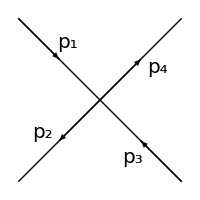

```mathematica
(* reproducting fig 5 of arXiv:0806.1240v2, rotated so time runs left to right*)
Graphics[{ Arrowheads[0.05],  (* --- *) Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}] ,Arrow[{{0,0},{0.5,0.5}}] ,Arrow[{{0,0},{-0.5,-0.5}}],Arrow[{{-1,1},{-0.5,0.5}}],Arrow[{{1,-1},{0.5,-0.5}}],
Text[Style[p4,20],{0.7,0.4}],Text[Style[p2,20],{-0.7,-0.4}],Text[Style[p1,20],{-0.4,0.7}],Text[Style[p3,20],{0.4,-0.7}](* --- *)    },ImageSize->200]
```

#### Graph 12

```mathematica
(* here we direct the loop momentum from 1 to 2 *)
```

```mathematica
amplitude12prefac=-I*g^2
amplitude12Denominator=(SPD[k,k]-M^2)(SPD[k+p1,k+p1])(SPD[k-p2,k-p2])
amplitude12DiracStructure=SpinorUBar[p4].GAD[tau].PhatL.SpinorV[p3]*SpinorVBar[p2].GAD[mu].GAD[rho].GAD[tau].PhatL.GAD[sigma].GAD[mu].SpinorU[p1]*FVD[k-p2,rhoo]*FVD[k+p1,sigmaa]
(* shifted momentum l equals *)kprime12=k+y*p1-z*p2;
amplitude12DiracStructureShifted=amplitude12DiracStructure/.FVD[k,a_]:> lambda*FVD[l,a]+FVD[(k-kprime12),a]
amplitude12DiracStructureZero=SeriesCoefficient[amplitude12DiracStructureShifted,{lambda,0,0}]
amplitude12DiracStructureTwo=SeriesCoefficient[amplitude12DiracStructureShifted,{lambda,0,2}]
```

-ⅈ g^2 1⊗1

(k^2-M^2) (2 k·p_1+k^2) (k^2-2 k·p_2)

(k^rhoo-p_2^rhoo) (k^sigmaa+p_1^sigmaa) ū(p_4).γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^μ.γ^ρ.γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(λ l^rhoo-y p_1^rhoo+z p_2^rhoo-p_2^rhoo) (λ l^sigmaa-y p_1^sigmaa+z p_2^sigmaa+p_1^sigmaa) ū(p_4).γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^μ.γ^ρ.γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(-y p_1^rhoo+z p_2^rhoo-p_2^rhoo) (-y p_1^sigmaa+z p_2^sigmaa+p_1^sigmaa) ū(p_4).γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^μ.γ^ρ.γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

l^rhoo l^sigmaa ū(p_4).γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^μ.γ^ρ.γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

```mathematica
amplitude12DiracStructureZero/.sigmaa->sigma/.rhoo->rho//PhatDef//Contract//FCE
%//DiracSimplify//FCE

%/.Spinor[a___].GAD[tau].Spinor[c___]:> Spinor[a].(2*GAD[tau].Inactive[GAD[AL]]+GAD[tau].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.Inactive[GAD[AL]]->PhatL
zeroth12Term=%/.Spinor[a___].GAD[tau].PhatL.Spinor[b___]*Spinor[c___].GAD[tau].PhatL.Spinor[d___]->M0//FullSimplify
%/(2SPD[p1,p2]*M0)//Expand
```

-1/4 φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_2).γ^τ.(1-γ^5).(γ·p_1).γ^μ.φ(p_1)+1/4 y^2 φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_1).γ^τ.(1-γ^5).(γ·p_1).γ^μ.φ(p_1)-1/4 y φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_1).γ^τ.(1-γ^5).(γ·p_1).γ^μ.φ(p_1)+1/4 y φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_2).γ^τ.(1-γ^5).(γ·p_1).γ^μ.φ(p_1)-1/4 y z φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_1).γ^τ.(1-γ^5).(γ·p_2).γ^μ.φ(p_1)-1/4 y z φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_2).γ^τ.(1-γ^5).(γ·p_1).γ^μ.φ(p_1)+1/4 z^2 φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_2).γ^τ.(1-γ^5).(γ·p_2).γ^μ.φ(p_1)+1/4 z φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_2).γ^τ.(1-γ^5).(γ·p_1).γ^μ.φ(p_1)-1/4 z φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.(γ·p_2).γ^τ.(1-γ^5).(γ·p_2).γ^μ.φ(p_1)

-1/2 D y z p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+1/2 D y z p_1·p_2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)+1/2 D y z p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-1/2 D y z p_1·p_2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+p_1·p_2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)+p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-p_1·p_2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+y p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)-y p_1·p_2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-y p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+y p_1·p_2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+y z p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)-y z p_1·p_2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-y z p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+y z p_1·p_2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+z p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)-z p_1·p_2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-z p_1·p_2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+z p_1·p_2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)

-2 D y z p_1·p_2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)-4 p_1·p_2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+4 y p_1·p_2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+4 y z p_1·p_2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+4 z p_1·p_2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)

-2 D y z p_1·p_2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)-4 p_1·p_2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+4 y p_1·p_2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+4 y z p_1·p_2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+4 z p_1·p_2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)

2 M0 p_1·p_2 (y (2-(D-2) z)+2 (z-1))

-D y z+2 y z+2 y+2 z-2

```mathematica
(amplitude12DiracStructureTwo/.rho->alpha/.sigma->alpha/.FVD[l,rhoo]*FVD[l,sigmaa]->SPD[l,l]/D)//PhatDef//Contract//FCE
%//DiracSimplify//FCE

%/.Spinor[a___].GAD[tau].Spinor[c___]:> Spinor[a].(2*GAD[tau].Inactive[GAD[AL]]+GAD[tau].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.Inactive[GAD[AL]]->PhatL
quadratic12Term=%/.Spinor[a___].GAD[tau].PhatL.Spinor[b___]*Spinor[c___].GAD[tau].PhatL.Spinor[d___]->M0//FullSimplify
```

(l^2 φ(p_4).γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^α.γ^τ.(1-γ^5).γ^α.γ^μ.φ(p_1))/(4 D)

1/4 D l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+(l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3))/D-1/4 D l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-(l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1))/D-1/4 D l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-(l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3))/D+1/4 D l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+(l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3))/D-l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)+l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)

D l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+(4 l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3))/D-4 l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)

D l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+(4 l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3))/D-4 l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)

((D-2)^2 l^2 M0)/D

```mathematica
(* integrating the zeroth order term *)

zeroth12Term;
%/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GSD[p1].PhatL->PhatR.GSD[p1]/.GSD[p2].PhatL->PhatR.GSD[p2]//Simplify;
rah12=(%//DiracSimplify//FCE)/.PhatR.GSD[p1]->GSD[p1].PhatL/.PhatR.GSD[p2]->GSD[p2].PhatL

L0QCDEuclidean[rah12,x*M^2+SPD[kprime12-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p1,p2]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerZero12=Activate[%/.integrateAndEpsSeriesTermByTerm->integrateAndEps0SeriesTermByTerm,integrateAndEps0SeriesTermByTerm];

Series[preAnswerZero12,{eps,0,0}]//Normal
Series[%//Simplify,{M,0,0}]//Normal
Quiet@Series[-I(* imaginary unit from Wick rotation, -1 from oddness of resulting integrand *)*%*amplitude12prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerZero12=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerZero12//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Ls/2+Log[muMS]/.Ls->Lis-I*Pi/.alphaMS->alphabar*2*Pi//Expand
simpZero12=%//Expand
```

2 M0 p_1·p_2 (y (2-(D-2) z)+2 (z-1))

2^(2 ϵ-4) π^(1/2 (2 ϵ-4)) 1/2 (2 ϵ+2) integrateAndEpsSeriesTermByTerm[M0 Q^2 (M^2 (-y-z+1)-Q^2 y z)^(1/2 (-2 ϵ-2)) (2 (z-1)+y (2-(D-2) z))z01-y,{y,0,1}]

(4 π)^(ϵ-2) ϵ+1 integrateAndEpsSeriesTermByTerm[-(M0 Q^2 (y-1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ) (Q^(2 ϵ) y^ϵ (M^2 (-D y+2 y+2 ϵ)+2 Q^2 y (ϵ-1))-y ⅇ^(-ⅈ π ϵ) M^(2 ϵ) ((D-2) M^2 (ϵ-1)+Q^2 ((D-2) y ϵ-2))))/((ϵ-1) ϵ (M^2+Q^2 y)^2),{y,0,1}]

Integrating (2 M^2 M0 Q^(2 ϵ+2) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(2 M^2 M0 Q^(2 ϵ+2) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))+(2 M0 Q^(2 ϵ+4) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(2 M0 Q^(2 ϵ+4) y^(ϵ+2) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))+(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y^3 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y^3 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))+(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))+(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))+(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(D M^2 M0 Q^(2 ϵ+2) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(2 M^2 M0 Q^(2 ϵ+2) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)-(2 M0 Q^(2 ϵ+4) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(D M^2 M0 Q^(2 ϵ+2) y^(ϵ+2) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)-(2 M^2 M0 Q^(2 ϵ+2) y^(ϵ+2) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(2 M0 Q^(2 ϵ+4) y^(ϵ+2) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)-(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)-(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)-(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

Integrating 24 terms.

Term 1 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

1 : (2^(2 ϵ-1) ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 √π Q^2 (M Q)^(-2 ϵ) 1-ϵ (((2 ϵ-1) M^2+Q^2 (ϵ-1)) 12-ϵ3-2 ϵ-Q^2/M^2-2 M^2 (ϵ-1)))/((M^2+Q^2) (ϵ-1) 3/2-ϵ)

1 : -(2 M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/(Q^2 (M^2+Q^2))

Term 2 : -(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

2 : -(4^(ϵ-1) D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 √π Q^2 (M Q)^(-2 ϵ) 1-ϵ (((2 ϵ-1) M^2+Q^2 (ϵ-1)) 12-ϵ3-2 ϵ-Q^2/M^2-2 M^2 (ϵ-1)))/((M^2+Q^2) (ϵ-1) 3/2-ϵ)

2 : (D M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/(Q^2 (M^2+Q^2))

Term 3 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

3 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) 4-2 ϵ)

3 : -(2 M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/(Q^4 (M^2+Q^2))

Term 4 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

4 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) 4-2 ϵ)

4 : (D M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/(Q^4 (M^2+Q^2))

Term 5 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

5 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 Q^4 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) 4-2 ϵ)

5 : -(2 M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/(Q^2 (M^2+Q^2))

Term 6 : -(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

6 : -(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 Q^4 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) 4-2 ϵ)

6 : (D M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/(Q^2 (M^2+Q^2))

Term 7 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y^3 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

7 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 Q^4 (M Q)^(-2 ϵ) 1-ϵ 4-ϵ (M^2/(4-2 ϵ)+((2 ϵ-3) M^2+Q^2 (ϵ-3)) 14-ϵ5-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1))

7 : (M0 (6 log(Q^2/M^2+1) M^6-6 Q^2 M^4+6 Q^2 log(Q^2/M^2+1) M^4-3 Q^4 M^2+Q^6))/(Q^4 (M^2+Q^2))

Term 8 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y^3 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

8 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 Q^4 (M Q)^(-2 ϵ) 1-ϵ 4-ϵ (M^2/(4-2 ϵ)+((2 ϵ-3) M^2+Q^2 (ϵ-3)) 14-ϵ5-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1))

8 : -(D M0 (6 log(Q^2/M^2+1) M^6-6 Q^2 M^4+6 Q^2 log(Q^2/M^2+1) M^4-3 Q^4 M^2+Q^6))/(2 Q^4 (M^2+Q^2))

Term 9 : (2 M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

9 : -(2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) (112-ϵ-Q^2/M^2 ϵ-ϵ+1))/((M^2+Q^2) (ϵ-1)^2)

9 : -(2 M0 Q^2)/(M^2+Q^2)

Term 10 : -(2 M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

10 : (2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) ((ϵ M^2)/(ϵ-1)^2+(Q^2-M^2 (ϵ-1)) 1-ϵ 113-ϵ-Q^2/M^2))/((M^2+Q^2)^2)

10 : (2 M0 (log(Q^2/M^2+1) M^4-Q^2 M^2+Q^2 log(Q^2/M^2+1) M^2))/(Q^2 (M^2+Q^2))

Term 11 : (2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

11 : -(2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) (ϵ/(ϵ-1)+((Q^2-M^2 (ϵ-1)) 113-ϵ-Q^2/M^2)/(M^2 (ϵ-2))))/((M^2+Q^2)^2 (ϵ-1))

11 : -(2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/(M^2+Q^2)

Term 12 : -(2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

12 : -(2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+(M^2 (ϵ-2)-2 Q^2) 3-ϵ 114-ϵ-Q^2/M^2+(M^2+Q^2)/(1-ϵ)))/((M^2+Q^2)^3 (ϵ-1))

12 : (2 M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/(Q^2 (M^2+Q^2))

Term 13 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

13 : -(2^(2 ϵ-1) ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 √π Q^2 (M Q)^(-2 ϵ) 1-ϵ (((2 ϵ-1) M^2+Q^2 (ϵ-1)) 12-ϵ3-2 ϵ-Q^2/M^2-2 M^2 (ϵ-1)))/((M^2+Q^2) (ϵ-1) ϵ 3/2-ϵ)

13 : (2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)) M^2)/(Q^2 (M^2+Q^2) ϵ)+(M0 √π Q^2 ((-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(M^2 √π Q^4)-((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/M^2+(log(M Q))/M^2-ℽ/(2 M^2)-1/(2 M^2)-(-(ⅈ π)/2+log(2))/M^2))/(√π)-(03/2)/(M^2 √π))))/(M^2+Q^2)

Term 14 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

14 : (4^(ϵ-1) D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 √π Q^2 (M Q)^(-2 ϵ) 1-ϵ (((2 ϵ-1) M^2+Q^2 (ϵ-1)) 12-ϵ3-2 ϵ-Q^2/M^2-2 M^2 (ϵ-1)))/((M^2+Q^2) (ϵ-1) ϵ 3/2-ϵ)

14 : (D M0 √π Q^2 (((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/(2 M^2)+(log(M Q))/(2 M^2)-ℽ/(4 M^2)-1/(4 M^2)-(-(ⅈ π)/4+(log(4))/4)/M^2))/(√π)-(03/2)/(2 M^2 √π))-(-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(2 M^2 √π Q^4)))/(M^2+Q^2)-(D M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/(Q^2 (M^2+Q^2) ϵ)

Term 15 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

15 : (2^(2 ϵ-1) ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 √π Q^4 (M Q)^(-2 ϵ) 1-ϵ (((2 ϵ-1) M^2+Q^2 (ϵ-1)) 12-ϵ3-2 ϵ-Q^2/M^2-2 M^2 (ϵ-1)))/((M^2+Q^2) (ϵ-1) ϵ 3/2-ϵ)

15 : (M0 √π Q^4 (((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/M^4+(log(M Q))/M^4-ℽ/(2 M^4)-1/(2 M^4)-(-(ⅈ π)/2+log(2))/M^4))/(√π)-(03/2)/(M^4 √π))-(-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(M^4 √π Q^4)))/(M^2+Q^2)-(2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/((M^2+Q^2) ϵ)

Term 16 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

16 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) ϵ 4-2 ϵ)

16 : (2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4) M^2)/(Q^4 (M^2+Q^2) ϵ)+(2 M0 Q^2 ((2 (1/6 (-(2 log(M))/M^2+(2 log(M Q))/M^2-1/M^2+(ⅈ π)/M^2)-ℽ/(6 M^2)-(11/18-ℽ/3)/M^2)+(3/2-ℽ)/(3 M^2)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)-(6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^2 Q^6)))/(M^2+Q^2)

Term 17 : -(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

17 : -(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) ϵ 4-2 ϵ)

17 : (D M0 Q^2 ((6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^2 Q^6)-(2 (1/6 (-(2 log(M))/M^2+(2 log(M Q))/M^2-1/M^2+(ⅈ π)/M^2)-ℽ/(6 M^2)-(11/18-ℽ/3)/M^2)+(3/2-ℽ)/(3 M^2)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)))/(M^2+Q^2)-(D M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/(Q^4 (M^2+Q^2) ϵ)

Term 18 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

18 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 Q^4 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) ϵ 4-2 ϵ)

18 : (2 M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/(Q^2 (M^2+Q^2) ϵ)-(2 M0 Q^4 ((2 (1/6 (-(2 log(M))/M^4+(2 log(M Q))/M^4-1/M^4+(ⅈ π)/M^4)-ℽ/(6 M^4)-(11/18-ℽ/3)/M^4)+(3/2-ℽ)/(3 M^4)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)-(6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^4 Q^6)))/(M^2+Q^2)

Term 19 : (2 M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

19 : (2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) ((Q^2-M^2 (ϵ-1)) -ϵ 113-ϵ-Q^2/M^2-M^2/(ϵ-1)^2))/((M^2+Q^2)^2)

19 : -(2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)) M^2)/(Q^2 (M^2+Q^2) ϵ)-(M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2))/(Q^2 (M^2+Q^2))

Term 20 : -(D M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

20 : (D M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) (M^2/(ϵ-1)^2+(M^2 (ϵ-1)-Q^2) -ϵ 113-ϵ-Q^2/M^2))/((M^2+Q^2)^2)

20 : (D M0 ((log(Q^2/M^2+1) M^2)/Q^2+log(Q^2/M^2+1)-1) M^2)/((M^2+Q^2) ϵ)+(D M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2))/(2 Q^2 (M^2+Q^2))

Term 21 : -(2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

21 : (2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) (((M^2 (ϵ-1)-Q^2) -ϵ 113-ϵ-Q^2/M^2)/M^2+1/(ϵ-1)^2))/((M^2+Q^2)^2)

21 : (2 M0 ((log(Q^2/M^2+1) M^2)/Q^2+log(Q^2/M^2+1)-1) Q^2)/((M^2+Q^2) ϵ)+(M0 (-log^2(Q^2/M^2+1) M^2+4 log(Q) log(Q^2/M^2+1) M^2-4 log(M Q) log(Q^2/M^2+1) M^2-2 2-Q^2/M^2 M^2-2 Q^2-Q^2 log^2(Q^2/M^2+1)-4 Q^2 log(Q)+4 Q^2 log(M Q)+2 Q^2 log(Q^2/M^2+1)+4 Q^2 log(Q) log(Q^2/M^2+1)-4 Q^2 log(M Q) log(Q^2/M^2+1)-2 Q^2 2-Q^2/M^2))/(M^2+Q^2)

Term 22 : -(2 M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

22 : -(2 M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+(M^2 (ϵ-2)-2 Q^2) 3-ϵ 114-ϵ-Q^2/M^2+(M^2+Q^2)/(1-ϵ)))/((M^2+Q^2)^3 (ϵ-1) ϵ)

22 : -(2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4) M^2)/(Q^4 (M^2+Q^2) ϵ)-(2 M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4+log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2-2 Q^4-2 Q^4 log(Q)+2 Q^4 log(M Q)) M^2)/(Q^4 (M^2+Q^2))

Term 23 : (D M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

23 : (D M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+(M^2 (ϵ-2)-2 Q^2) 3-ϵ 114-ϵ-Q^2/M^2+(M^2+Q^2)/(1-ϵ)))/((M^2+Q^2)^3 (ϵ-1) ϵ)

23 : (D M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4) M^2)/(Q^4 (M^2+Q^2) ϵ)+(D M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4+log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2-2 Q^4-2 Q^4 log(Q)+2 Q^4 log(M Q)) M^2)/(Q^4 (M^2+Q^2))

Term 24 : (2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

24 : (2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+(M^2 (ϵ-2)-2 Q^2) 3-ϵ 114-ϵ-Q^2/M^2+(M^2+Q^2)/(1-ϵ)))/((M^2+Q^2)^3 (ϵ-1) ϵ)

24 : -(2 M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/(Q^2 (M^2+Q^2) ϵ)-(2 M0 (log^2(Q^2/M^2+1) M^4-4 log(Q) log(Q^2/M^2+1) M^4+4 log(M Q) log(Q^2/M^2+1) M^4-log(Q^2/M^2+1) M^4+2 2-Q^2/M^2 M^4+3 Q^2 M^2+Q^2 log^2(Q^2/M^2+1) M^2+4 Q^2 log(Q) M^2-4 Q^2 log(M Q) M^2-2 Q^2 log(Q^2/M^2+1) M^2-4 Q^2 log(Q) log(Q^2/M^2+1) M^2+4 Q^2 log(M Q) log(Q^2/M^2+1) M^2+2 Q^2 2-Q^2/M^2 M^2+2 Q^4+2 Q^4 log(Q)-2 Q^4 log(M Q)))/(Q^2 (M^2+Q^2))

1/(16 π^2)((M0 √π (((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/M^4+(log(M Q))/M^4-ℽ/(2 M^4)-1/(2 M^4)-(-(ⅈ π)/2+log(2))/M^4))/(√π)-(03/2)/(M^4 √π))-(-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(M^4 √π Q^4)) Q^4)/(M^2+Q^2)-(2 M0 ((2 (1/6 (-(2 log(M))/M^4+(2 log(M Q))/M^4-1/M^4+(ⅈ π)/M^4)-ℽ/(6 M^4)-(11/18-ℽ/3)/M^4)+(3/2-ℽ)/(3 M^4)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)-(6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^4 Q^6)) Q^4)/(M^2+Q^2)+(D M0 √π (((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/(2 M^2)+(log(M Q))/(2 M^2)-ℽ/(4 M^2)-1/(4 M^2)-(-(ⅈ π)/4+(log(4))/4)/M^2))/(√π)-(03/2)/(2 M^2 √π))-(-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(2 M^2 √π Q^4)) Q^2)/(M^2+Q^2)+(M0 √π ((-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(M^2 √π Q^4)-((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/M^2+(log(M Q))/M^2-ℽ/(2 M^2)-1/(2 M^2)-(-(ⅈ π)/2+log(2))/M^2))/(√π)-(03/2)/(M^2 √π))) Q^2)/(M^2+Q^2)+(2 M0 ((2 (1/6 (-(2 log(M))/M^2+(2 log(M Q))/M^2-1/M^2+(ⅈ π)/M^2)-ℽ/(6 M^2)-(11/18-ℽ/3)/M^2)+(3/2-ℽ)/(3 M^2)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)-(6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^2 Q^6)) Q^2)/(M^2+Q^2)+(D M0 ((6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^2 Q^6)-(2 (1/6 (-(2 log(M))/M^2+(2 log(M Q))/M^2-1/M^2+(ⅈ π)/M^2)-ℽ/(6 M^2)-(11/18-ℽ/3)/M^2)+(3/2-ℽ)/(3 M^2)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)) Q^2)/(M^2+Q^2)-(2 M0 Q^2)/(M^2+Q^2)-(2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/(M^2+Q^2)+(M0 (-log^2(Q^2/M^2+1) M^2+4 log(Q) log(Q^2/M^2+1) M^2-4 log(M Q) log(Q^2/M^2+1) M^2-2 2-Q^2/M^2 M^2-2 Q^2-Q^2 log^2(Q^2/M^2+1)-4 Q^2 log(Q)+4 Q^2 log(M Q)+2 Q^2 log(Q^2/M^2+1)+4 Q^2 log(Q) log(Q^2/M^2+1)-4 Q^2 log(M Q) log(Q^2/M^2+1)-2 Q^2 2-Q^2/M^2))/(M^2+Q^2)+(D M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/((M^2+Q^2) Q^2)-(2 M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/((M^2+Q^2) Q^2)+(D M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/((M^2+Q^2) Q^2)+(2 M0 (log(Q^2/M^2+1) M^4-Q^2 M^2+Q^2 log(Q^2/M^2+1) M^2))/((M^2+Q^2) Q^2)+(D M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2))/(2 (M^2+Q^2) Q^2)-(M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2))/((M^2+Q^2) Q^2)-1/((M^2+Q^2) Q^2)2 M0 (log^2(Q^2/M^2+1) M^4-4 log(Q) log(Q^2/M^2+1) M^4+4 log(M Q) log(Q^2/M^2+1) M^4-log(Q^2/M^2+1) M^4+2 2-Q^2/M^2 M^4+3 Q^2 M^2+Q^2 log^2(Q^2/M^2+1) M^2+4 Q^2 log(Q) M^2-4 Q^2 log(M Q) M^2-2 Q^2 log(Q^2/M^2+1) M^2-4 Q^2 log(Q) log(Q^2/M^2+1) M^2+4 Q^2 log(M Q) log(Q^2/M^2+1) M^2+2 Q^2 2-Q^2/M^2 M^2+2 Q^4+2 Q^4 log(Q)-2 Q^4 log(M Q))+(D M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/((M^2+Q^2) Q^4)-(2 M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/((M^2+Q^2) Q^4)-(D M0 (6 log(Q^2/M^2+1) M^6-6 Q^2 M^4+6 Q^2 log(Q^2/M^2+1) M^4-3 Q^4 M^2+Q^6))/(2 (M^2+Q^2) Q^4)+(M0 (6 log(Q^2/M^2+1) M^6-6 Q^2 M^4+6 Q^2 log(Q^2/M^2+1) M^4-3 Q^4 M^2+Q^6))/((M^2+Q^2) Q^4)+1/((M^2+Q^2) Q^4)D M^2 M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4+log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2-2 Q^4-2 Q^4 log(Q)+2 Q^4 log(M Q))-1/((M^2+Q^2) Q^4)2 M^2 M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4+log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2-2 Q^4-2 Q^4 log(Q)+2 Q^4 log(M Q)))

1/(96 π^2)(3 D M0-24 M0 log(M) log(Q^2)+24 M0 log^2(M)+24 ℽ M0 log(M)+48 M0 log(2) log(M)-24 ⅈ π M0 log(M)+24 M0 03/2 log(M)-12 ℽ M0 log(Q^2)+24 M0 log(Q^2)+24 M0 log(Q) log(Q^2)-24 M0 log(2) log(Q^2)+12 ⅈ π M0 log(Q^2)-12 M0 03/2 log(Q^2)-24 M0 log^2(Q)-48 M0 log(Q)+12 ℽ M0-6 M0-2 π^2 M0-24 ⅈ π M0+24 M0 log(2)+12 M0 03/2)

1/(12 π)1⊗1 α_OverBar[MS] (12 M0 log(M) log(Q^2)-12 M0 log^2(M)-12 ℽ M0 log(M)-24 M0 log(2) log(M)+12 ⅈ π M0 log(M)-12 M0 03/2 log(M)+6 ℽ M0 log(Q^2)-12 M0 log(Q^2)-12 M0 log(Q) log(Q^2)+12 M0 log(2) log(Q^2)-6 ⅈ π M0 log(Q^2)+6 M0 03/2 log(Q^2)+12 M0 log^2(Q)+24 M0 log(Q)-6 ℽ M0-3 M0+π^2 M0+12 ⅈ π M0-12 M0 log(2)-6 M0 03/2)

-(M0 1⊗1 log^2(M) α_OverBar[MS])/π+ⅈ M0 1⊗1 log(M) α_OverBar[MS]-(2 M0 1⊗1 log(M) α_OverBar[MS])/π+(2 M0 1⊗1 log(M) α_OverBar[MS] log(Q))/π+ⅈ M0 1⊗1 α_OverBar[MS]+1/12 π M0 1⊗1 α_OverBar[MS]-(5 M0 1⊗1 α_OverBar[MS])/(4 π)-(M0 1⊗1 α_OverBar[MS] log^2(Q))/π-ⅈ M0 1⊗1 α_OverBar[MS] log(Q)+(2 M0 1⊗1 α_OverBar[MS] log(Q))/π

-1/2 Lis^2 M0 ᾱ 1⊗1+Lis LM M0 ᾱ 1⊗1+2 Lis M0 ᾱ 1⊗1-1/2 LM^2 M0 ᾱ 1⊗1-2 LM M0 ᾱ 1⊗1-5/2 M0 ᾱ 1⊗1-1/3 π^2 M0 ᾱ 1⊗1

-1/2 Lis^2 M0 ᾱ 1⊗1+Lis LM M0 ᾱ 1⊗1+2 Lis M0 ᾱ 1⊗1-1/2 LM^2 M0 ᾱ 1⊗1-2 LM M0 ᾱ 1⊗1-5/2 M0 ᾱ 1⊗1-1/3 π^2 M0 ᾱ 1⊗1

```mathematica
(* integrating the zeroth order term *)

quadratic12Term/.SPD[l,l]->1;
%/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GSD[p1].PhatL->PhatR.GSD[p1]/.GSD[p2].PhatL->PhatR.GSD[p2]//Simplify;
rahrah12=(%//DiracSimplify//FCE)/.PhatR.GSD[p1]->GSD[p1].PhatL/.PhatR.GSD[p2]->GSD[p2].PhatL

L2QCDEuclidean[rahrah12,x*M^2+SPD[kprime12-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p1,p2]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerQuad12=Activate[%,integrateAndEpsSeriesTermByTerm];

Series[preAnswerQuad12//Simplify,{M,0,0}]//Normal
Quiet@Series[I(* imaginary unit from Wick rotation *)*%*amplitude12prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerQuad12=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerQuad12//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Ls/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpQuad12=%/.Ls->Lis-I*Pi//Expand
```

((D-2)^2 M0)/D

D 2^(2 ϵ-5) π^(1/2 (2 ϵ-4)) ϵ integrateAndEpsSeriesTermByTerm[((D-2)^2 M0 (M^2 (-y-z+1)-Q^2 y z)^-ϵ)/Dz01-y,{y,0,1}]

D 2^(2 ϵ-5) π^(ϵ-2) ϵ integrateAndEpsSeriesTermByTerm[((D-2)^2 M0 (y-1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ) (M^2 Q^(2 ϵ) y^ϵ+Q^2 y ⅇ^(-ⅈ π ϵ) M^(2 ϵ)))/(D (ϵ-1) (M^2+Q^2 y)),{y,0,1}]

D 2^(2 ϵ-5) π^(ϵ-2) ϵ integrateAndEpsSeriesTermByTerm[((D-2)^2 M0 (y-1) ⅇ^(-ⅈ π ϵ) M^(2 ϵ) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (ϵ-1)),{y,0,1}]

(1⊗1 α_OverBar[MS] integrateAndEpsSeriesTermByTerm[-M0 (y-1),{y,0,1}])/(2 π ϵ)+(1⊗1 α_OverBar[MS] ((4 (log(μ_OverBar[MS]^2)+ℽ)-4 ℽ-2) integrateAndEpsSeriesTermByTerm[-M0 (y-1),{y,0,1}]+2 M0 (y-1) (4 log(M Q)-4 log(M)+2 log(-(y-1) y)+2 ⅈ π+1) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(-M0 (y-1),{y,0,1})))/(8 π)

(1⊗1 α_OverBar[MS] log(μ_OverBar[MS]) integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}])/π+(1⊗1 α_OverBar[MS] integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}])/(2 π ϵ)-(1⊗1 α_OverBar[MS] integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}])/(4 π)+(M0 y 1⊗1 α_OverBar[MS] log(Q) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1}))/π-(M0 1⊗1 α_OverBar[MS] log(Q) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1}))/π-ⅈ M0 1⊗1 α_OverBar[MS] integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+ⅈ M0 y 1⊗1 α_OverBar[MS] integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+(M0 y 1⊗1 α_OverBar[MS] integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1}))/(4 π)-(M0 1⊗1 α_OverBar[MS] integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1}))/(4 π)+(M0 y 1⊗1 α_OverBar[MS] log(y-1) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1}))/(2 π)-(M0 1⊗1 α_OverBar[MS] log(y-1) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1}))/(2 π)+(M0 y 1⊗1 α_OverBar[MS] log(y) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1}))/(2 π)-(M0 1⊗1 α_OverBar[MS] log(y) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1}))/(2 π)

2 ᾱ 1⊗1 log(μ_OverBar[MS]) integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}]+(ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}])/ϵ-1/2 ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}]-Ls M0 ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+Ls M0 y ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-2 M0 ᾱ 1⊗1 log(μ_OverBar[MS]) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+2 M0 y ᾱ 1⊗1 log(μ_OverBar[MS]) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-1/2 M0 ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+1/2 M0 y ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+2 ⅈ π M0 y ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-2 ⅈ π M0 ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-M0 ᾱ 1⊗1 log(y-1) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+M0 y ᾱ 1⊗1 log(y-1) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-M0 ᾱ 1⊗1 log(y) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+M0 y ᾱ 1⊗1 log(y) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})

2 ᾱ 1⊗1 log(μ_OverBar[MS]) integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}]+(ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}])/ϵ-1/2 ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}]-Lis M0 ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+Lis M0 y ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-2 M0 ᾱ 1⊗1 log(μ_OverBar[MS]) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+2 M0 y ᾱ 1⊗1 log(μ_OverBar[MS]) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-1/2 M0 ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+1/2 M0 y ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+ⅈ π M0 y ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-ⅈ π M0 ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-M0 ᾱ 1⊗1 log(y-1) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+M0 y ᾱ 1⊗1 log(y-1) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-M0 ᾱ 1⊗1 log(y) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+M0 y ᾱ 1⊗1 log(y) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})

#### Graph 13

```mathematica
(* here we direct the loop momentum from 3 to 1 *)
```

```mathematica
amplitude13prefac=-g^2
amplitude13Denominator=(SPD[k,k]-M^2)(SPD[k+p1,k+p1])(SPD[k+p3,k+p3])
amplitude13DiracStructure=SpinorUBar[p4].GAD[tau].PhatL.GAD[rho].GAD[mu].SpinorV[p3]*SpinorVBar[p2].GAD[tau].PhatL.GAD[sigma].GAD[mu].SpinorU[p1]*FVD[k+p3,rhoo]*FVD[k+p1,sigmaa]
(* shifted momentum l equals *)kprime13=k+y*p1+z*p3;
amplitude13DiracStructureShifted=amplitude13DiracStructure/.FVD[k,a_]:> lambda*FVD[l,a]+FVD[(k-kprime13),a]
amplitude13DiracStructureZero=SeriesCoefficient[amplitude13DiracStructureShifted,{lambda,0,0}]
amplitude13DiracStructureTwo=SeriesCoefficient[amplitude13DiracStructureShifted,{lambda,0,2}]
```

-g^2

(k^2-M^2) (2 k·p_1+k^2) (2 k·p_3+k^2)

(k^rhoo+p_3^rhoo) (k^sigmaa+p_1^sigmaa) ū(p_4).γ^τ.(P̂)_L.γ^ρ.γ^μ.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(λ l^rhoo-y p_1^rhoo-z p_3^rhoo+p_3^rhoo) (λ l^sigmaa-y p_1^sigmaa-z p_3^sigmaa+p_1^sigmaa) ū(p_4).γ^τ.(P̂)_L.γ^ρ.γ^μ.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(-y p_1^rhoo-z p_3^rhoo+p_3^rhoo) (-y p_1^sigmaa-z p_3^sigmaa+p_1^sigmaa) ū(p_4).γ^τ.(P̂)_L.γ^ρ.γ^μ.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

l^rhoo l^sigmaa ū(p_4).γ^τ.(P̂)_L.γ^ρ.γ^μ.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

```mathematica
amplitude13DiracStructureZero(*/.sigmaa->sigma/.rhoo->rho*)//PhatDef//Contract//FCE
%//DiracSimplify//FCE;
%/.GAD[tau].GAD[a_].GAD[mu]:> MTD[tau,a]GAD[mu]+GAD[tau] MTD[a,mu]- MTD[tau,mu]GAD[a]+I*levi5[tau,a,mu];  (* the 3-gamma identity, with gamma5 in D=4 *)
%//DiracSimplify//FCE;

%/.MT[a_,b_]:> MTD[a,b]/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE;
%/.MT[a_,b_]:> MTD[a,b]/.Inactive[GAD[AL]]->PhatL;
%/.MT[a_,b_]:> MTD[a,b]/.Spinor[a___].GAD[r_].PhatL.Spinor[b___]*Spinor[c___].GAD[r_].PhatL.Spinor[d___]->M0//Expand;
cleanIndices[%,xi1,xi2]/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//Simplify
%/.GSD[p1].PhatL->PhatR.GSD[p1]/.GSD[p3].PhatL->PhatR.GSD[p3]//DiracSimplify//FCE
(* use spinor helicity to derive fact that Ubar4.GSD[p1].V3 Vbar2.GSD[3].U1 = -SPD{p1,p4] M0 *)
zeroth13Term=%/.Spinor[Momentum[p2],___].PhatR.GSD[p3].Spinor[Momentum[p1],___]Spinor[Momentum[p4],___].PhatR.GSD[p1].Spinor[Momentum[p3],___]->-SPD[p1,p4]*M0
```

1/4 p_3^rhoo p_1^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y^2 p_1^rhoo p_1^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 y p_1^rhoo p_1^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 y p_3^rhoo p_1^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y z p_3^rhoo p_1^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y z p_1^rhoo p_3^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 z^2 p_3^rhoo p_3^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 z p_3^rhoo p_1^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 z p_3^rhoo p_3^sigmaa φ(p_4).γ^τ.(1-γ^5).γ^ρ.γ^μ.φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)

(D-4) (y-1) y φ(p_2).(γ·p_1).(P̂)_L.φ(p_1) φ(p_4).(γ·p_1).(P̂)_L.φ(p_3)+(D-4) y z φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) φ(p_4).(γ·p_1).(P̂)_L.φ(p_3)+(D-4) (y-1) (z-1) φ(p_2).(γ·p_1).(P̂)_L.φ(p_1) φ(p_4).(γ·p_3).(P̂)_L.φ(p_3)+(D-4) (z-1) z φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) φ(p_4).(γ·p_3).(P̂)_L.φ(p_3)+8 M0 y z p_1·p_3-4 M0 y p_1·p_3-4 M0 z p_1·p_3+4 M0 p_1·p_3

(D-4) y z φ(p_2).(P̂)_R.(γ·p_3).φ(p_1) φ(p_4).(P̂)_R.(γ·p_1).φ(p_3)+8 M0 y z p_1·p_3-4 M0 y p_1·p_3-4 M0 z p_1·p_3+4 M0 p_1·p_3

-(D-4) M0 y z p_1·p_4+8 M0 y z p_1·p_3-4 M0 y p_1·p_3-4 M0 z p_1·p_3+4 M0 p_1·p_3

```mathematica
(amplitude13DiracStructureTwo/.rho->alpha/.sigma->alpha/.FVD[l,rhoo]*FVD[l,sigmaa]->SPD[l,l]/D)//PhatDef//Contract//FCE
%//DiracSimplify//FCE
%/.GAD[tau].GAD[a_].GAD[mu]:> MTD[tau,a]GAD[mu]+GAD[tau] MTD[a,mu]- MTD[tau,mu]GAD[a]+I*levi5[tau,a,mu]  (* the 3-gamma identity, with gamma5 in D=4 *)
%//DiracSimplify//FCE

(* need to put feyncalc-simplified amplitude back in left-chiral basis *)
%/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.Inactive[GAD[AL]]->PhatL

quadratic13Term=%/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//Simplify

(* should be 16 L^2/D = D *)
```

(l^2 φ(p_2).γ^τ.(1-γ^5).γ^α.γ^μ.φ(p_1) φ(p_4).γ^τ.(1-γ^5).γ^α.γ^μ.φ(p_3))/(4 D)

(l^2 φ(p_2).γ^τ.γ^α.γ^μ.φ(p_1) φ(p_4).γ^τ.γ^α.γ^μ.φ(p_3))/(4 D)-(l^2 φ(p_4).γ^τ.γ^α.γ^μ.φ(p_3) φ(p_2).γ^τ.γ^α.γ^μ.γ^5.φ(p_1))/(4 D)-(l^2 φ(p_2).γ^τ.γ^α.γ^μ.φ(p_1) φ(p_4).γ^τ.γ^α.γ^μ.γ^5.φ(p_3))/(4 D)+(l^2 φ(p_2).γ^τ.γ^α.γ^μ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^α.γ^μ.γ^5.φ(p_3))/(4 D)

(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$222327.γ^5 ϵ^ταμind$222327).φ(p_1) φ(p_4).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$222328.γ^5 ϵ^ταμind$222328).φ(p_3))/(4 D)-(l^2 φ(p_4).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$222329.γ^5 ϵ^ταμind$222329).φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$222330.γ^5 ϵ^ταμind$222330).γ^5.φ(p_1))/(4 D)-(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$222331.γ^5 ϵ^ταμind$222331).φ(p_1) φ(p_4).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$222332.γ^5 ϵ^ταμind$222332).γ^5.φ(p_3))/(4 D)+(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$222333.γ^5 ϵ^ταμind$222333).γ^5.φ(p_1) φ(p_4).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$222334.γ^5 ϵ^ταμind$222334).γ^5.φ(p_3))/(4 D)

(3 l^2 φ(p_2).γ^ind$222328.γ^5.φ(p_1) φ(p_4).γ^ind$222328.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$222329.φ(p_1) φ(p_4).γ^ind$222329.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_4).γ^ind$222331.φ(p_3) φ(p_2).γ^ind$222331.γ^5.φ(p_1))/(2 D)+(3 l^2 φ(p_2).γ^ind$222334.φ(p_1) φ(p_4).γ^ind$222334.φ(p_3))/(2 D)-(l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.φ(p_3))/(2 D)+(l^2 φ(p_4).γ^α.φ(p_3) φ(p_2).γ^α.γ^5.φ(p_1))/(2 D)+(l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3))/(2 D)-(l^2 φ(p_2).γ^α.γ^5.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3))/(2 D)+1/4 l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.φ(p_3)-1/4 l^2 φ(p_4).γ^α.φ(p_3) φ(p_2).γ^α.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^α.γ^5.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+1/4 l^2 φ(p_2).γ^μ.φ(p_1) φ(p_4).γ^μ.φ(p_3)-1/4 l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-1/4 l^2 φ(p_4).γ^μ.φ(p_3) φ(p_2).γ^μ.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^μ.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3)

-(3 l^2 φ(p_4).γ^ind$222329.γ^5.φ(p_3) φ(p_2).γ^ind$222329.Inactive[γ^AL].φ(p_1))/D-(3 l^2 φ(p_2).γ^ind$222331.γ^5.φ(p_1) φ(p_4).γ^ind$222331.Inactive[γ^AL].φ(p_3))/D+(6 l^2 φ(p_2).γ^ind$222334.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ind$222334.Inactive[γ^AL].φ(p_3))/D+(3 l^2 φ(p_4).γ^ind$222334.γ^5.φ(p_3) φ(p_2).γ^ind$222334.Inactive[γ^AL].φ(p_1))/D+(3 l^2 φ(p_2).γ^ind$222334.γ^5.φ(p_1) φ(p_4).γ^ind$222334.Inactive[γ^AL].φ(p_3))/D-(2 l^2 φ(p_2).γ^α.Inactive[γ^AL].φ(p_1) φ(p_4).γ^α.Inactive[γ^AL].φ(p_3))/D+l^2 φ(p_2).γ^α.Inactive[γ^AL].φ(p_1) φ(p_4).γ^α.Inactive[γ^AL].φ(p_3)+l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+l^2 φ(p_2).γ^μ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^μ.Inactive[γ^AL].φ(p_3)+(3 l^2 φ(p_2).γ^ind$222328.γ^5.φ(p_1) φ(p_4).γ^ind$222328.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$222329.γ^5.φ(p_1) φ(p_4).γ^ind$222329.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$222331.γ^5.φ(p_1) φ(p_4).γ^ind$222331.γ^5.φ(p_3))/(2 D)+(3 l^2 φ(p_2).γ^ind$222334.γ^5.φ(p_1) φ(p_4).γ^ind$222334.γ^5.φ(p_3))/(2 D)

(3 l^2 φ(p_2).γ^ind$222328.γ^5.φ(p_1) φ(p_4).γ^ind$222328.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_4).γ^ind$222329.γ^5.φ(p_3) φ(p_2).γ^ind$222329.(P̂)_L.φ(p_1))/D-(3 l^2 φ(p_2).γ^ind$222329.γ^5.φ(p_1) φ(p_4).γ^ind$222329.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$222331.γ^5.φ(p_1) φ(p_4).γ^ind$222331.(P̂)_L.φ(p_3))/D-(3 l^2 φ(p_2).γ^ind$222331.γ^5.φ(p_1) φ(p_4).γ^ind$222331.γ^5.φ(p_3))/(2 D)+(6 l^2 φ(p_2).γ^ind$222334.(P̂)_L.φ(p_1) φ(p_4).γ^ind$222334.(P̂)_L.φ(p_3))/D+(3 l^2 φ(p_2).γ^ind$222334.γ^5.φ(p_1) φ(p_4).γ^ind$222334.(P̂)_L.φ(p_3))/D+(3 l^2 φ(p_4).γ^ind$222334.γ^5.φ(p_3) φ(p_2).γ^ind$222334.(P̂)_L.φ(p_1))/D+(3 l^2 φ(p_2).γ^ind$222334.γ^5.φ(p_1) φ(p_4).γ^ind$222334.γ^5.φ(p_3))/(2 D)-(2 l^2 φ(p_2).γ^α.(P̂)_L.φ(p_1) φ(p_4).γ^α.(P̂)_L.φ(p_3))/D+l^2 φ(p_2).γ^α.(P̂)_L.φ(p_1) φ(p_4).γ^α.(P̂)_L.φ(p_3)+l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+l^2 φ(p_2).γ^μ.(P̂)_L.φ(p_1) φ(p_4).γ^μ.(P̂)_L.φ(p_3)

((3 D+4) l^2 M0)/D

```mathematica
(* integrating the zeroth order term *)

cleanIndices[zeroth13Term,xi1,xi2]
%/.sigmaa->sigma/.rhoo->rho//Contract//DiracSimplify//FCE;

rah13=(%//DiracSimplify//FCE)/.PhatR.GSD[p1]->GSD[p1].PhatL/.PhatR.GSD[p3]->GSD[p3].PhatL

L0QCDEuclidean[rah13,x*M^2+SPD[kprime13-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p3,p3]->0/.SPD[p1,p3]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)

(* since the integral prefactor has no pole in epsilon, can expand the integrals up to zeroth order *)
preAnswerZero13=Activate[%/.integrateAndEpsSeriesTermByTerm:> integrateAndEps0SeriesTermByTerm,integrateAndEps0SeriesTermByTerm]
```

-(D-4) M0 y z p_1·p_4+8 M0 y z p_1·p_3-4 M0 y p_1·p_3-4 M0 z p_1·p_3+4 M0 p_1·p_3

-(D-4) M0 y z p_1·p_4+8 M0 y z p_1·p_3-4 M0 y p_1·p_3-4 M0 z p_1·p_3+4 M0 p_1·p_3

2^(2 ϵ-4) π^(1/2 (2 ϵ-4)) 1/2 (2 ϵ+2) integrateAndEpsSeriesTermByTerm[((-y-z+1) M^2+Q^2 y z)^(1/2 (-2 ϵ-2)) (2 M0 Q^2-2 M0 y Q^2-2 M0 z Q^2+4 M0 y z Q^2-(D-4) M0 y z p_1·p_4)z01-y,{y,0,1}]

(4 π)^(ϵ-2) ϵ+1 integrateAndEpsSeriesTermByTerm[(M0 (y-1) Q^(-2 ϵ) (-(y-1) y)^-ϵ ((D-4) y p_1·p_4 (M^2 (y^ϵ (M/Q)^(-2 ϵ)+ϵ-1)-Q^2 y ϵ)+2 Q^2 (y^ϵ (M/Q)^(-2 ϵ) (M^2 (ϵ-2 y)-Q^2 y (ϵ-1))+y (Q^2 (2 y ϵ-1)-2 M^2 (ϵ-1)))))/((ϵ-1) ϵ (M^2-Q^2 y)^2),{y,0,1}]

Integrating -(D M0 y^3 (-(y-1) y)^-ϵ p_1·p_4 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(4 M0 y^3 (-(y-1) y)^-ϵ p_1·p_4 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(D M0 y^2 (-(y-1) y)^-ϵ p_1·p_4 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(4 M0 y^2 (-(y-1) y)^-ϵ p_1·p_4 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(2 M^2 M0 (M/Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(2 M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(4 M^2 M0 y^2 (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(4 M^2 M0 y (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(4 M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)-(4 M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(4 M^2 M0 y^2 (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)-(4 M^2 M0 y (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(4 M0 y^3 (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(4 M0 y^2 (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)-(2 M0 y^2 (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(2 M0 y (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(D M^2 M0 y^2 (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(4 M^2 M0 y^2 (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(D M^2 M0 y (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(4 M^2 M0 y (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(D M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(4 M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(D M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)-(4 M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)-(D M^2 M0 y^2 (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(4 M^2 M0 y^2 (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(D M^2 M0 y (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)-(4 M^2 M0 y (-(y-1) y)^-ϵ p_1·p_4 Q^(-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

Integrating 32 terms.

Term 1 : (4 M^2 M0 Q^(2-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

1 : -(4 M0 Q^(2-2 ϵ) (1-ϵ)^2 22-ϵ3-2 ϵQ^2/M^2)/M^2

1 : -(4 (M0 log(1-Q^2/M^2) M^4+M0 Q^2 M^2-M0 Q^2 log(1-Q^2/M^2) M^2))/(Q^2 (M^2-Q^2))

Term 2 : -(4 M^2 M0 Q^(2-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

2 : -(4 M0 Q^(2-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^2 (ϵ-1))

2 : (4 M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/(Q^4 (M^2-Q^2))

Term 3 : -(4 M0 Q^(4-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

3 : -(4 M0 Q^(4-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^4 (ϵ-1))

3 : (4 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(Q^2 (Q^2-M^2))

Term 4 : (4 M0 Q^(4-2 ϵ) y^3 (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

4 : (4 M0 Q^(4-2 ϵ) 1-ϵ 4-ϵ 24-ϵ5-2 ϵQ^2/M^2)/(M^4 (ϵ-1))

4 : -(2 M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6))/(Q^4 (Q^2-M^2))

Term 5 : -(2 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

5 : (2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) (112-ϵQ^2/M^2 ϵ-ϵ+1))/((M^2-Q^2) (ϵ-1)^2)

5 : (2 M0 Q^2)/(M^2-Q^2)

Term 6 : (2 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

6 : (2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) (((ϵ-1) M^2+Q^2) 1-ϵ 113-ϵQ^2/M^2-(M^2 ϵ)/(ϵ-1)^2))/((M-Q)^2 (M+Q)^2)

6 : -(2 M0 (log(1-Q^2/M^2) M^4+Q^2 M^2-Q^2 log(1-Q^2/M^2) M^2))/((M-Q) Q^2 (M+Q))

Term 7 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

7 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) (((ϵ-1) M^2+Q^2) (ϵ-1) 113-ϵQ^2/M^2-M^2 (ϵ-2) ϵ))/((M^3-M Q^2)^2 (ϵ-2) (ϵ-1)^2)

7 : -(2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(M^2-Q^2)

Term 8 : -(2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

8 : -(2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)))/((M-Q)^3 (M+Q)^3 (ϵ-1))

8 : (2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^2 (M+Q))

Term 9 : -(4 M^2 M0 Q^(2-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

9 : -(4 M0 Q^(2-2 ϵ) 1-ϵ -ϵ 22-ϵ3-2 ϵQ^2/M^2)/M^2

9 : (4 (M0 log(1-Q^2/M^2) M^4+M0 Q^2 M^2-M0 Q^2 log(1-Q^2/M^2) M^2))/(Q^2 (M^2-Q^2) ϵ)-(2 (M0 log^2(1-Q^2/M^2) M^4+2 M0 log(1-Q^2/M^2) M^4+4 M0 log(Q) log(1-Q^2/M^2) M^4+4 M0 2Q^2/M^2 M^4-2 M0 Q^2 M^2-M0 Q^2 log^2(1-Q^2/M^2) M^2+4 M0 Q^2 log(Q) M^2-4 M0 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 M0 Q^2 2Q^2/M^2 M^2))/(Q^2 (M^2-Q^2))

Term 10 : (2 M0 Q^(4-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

10 : (2 M0 Q^(4-2 ϵ) 1-ϵ -ϵ 22-ϵ3-2 ϵQ^2/M^2)/M^4

10 : (-M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+2 M0 Q^2+M0 Q^2 log^2(1-Q^2/M^2)-4 M0 Q^2 log(Q)+4 M0 Q^2 log(Q) log(1-Q^2/M^2)+4 M0 Q^2 2Q^2/M^2)/(Q^2-M^2)-(2 (M0 log(1-Q^2/M^2) M^2+M0 Q^2-M0 Q^2 log(1-Q^2/M^2)))/((M^2-Q^2) ϵ)

Term 11 : (4 M^2 M0 Q^(2-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

11 : -(4 M0 Q^(2-2 ϵ) 3-ϵ -ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^2 (ϵ-1))

11 : (4 M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)))/(Q^4 (M^2-Q^2))-(4 M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/(Q^4 (M^2-Q^2) ϵ)

Term 12 : -(2 M0 Q^(4-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

12 : (2 M0 Q^(4-2 ϵ) 3-ϵ -ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^4 (ϵ-1))

12 : (2 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(Q^2 (Q^2-M^2) ϵ)-(2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)))/(Q^2 (M^2-Q^2))

Term 13 : (4 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

13 : -(4 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) (M^2/(ϵ-1)^2+((ϵ-1) M^2+Q^2) -ϵ 113-ϵQ^2/M^2))/((M-Q)^2 (M+Q)^2)

13 : (2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2))/((M-Q) Q^2 (M+Q))-(4 M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/((M-Q) Q^2 (M+Q) ϵ)

Term 14 : -(2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

14 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) (M^2/(ϵ-1)^2+(ϵ M^2-M^2+Q^2) -ϵ 113-ϵQ^2/M^2))/((M^3-M Q^2)^2)

14 : (2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/((M^2-Q^2) ϵ)-(M0 (log^2(1-Q^2/M^2) M^2+4 log(M/Q) log(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(M/Q)+4 Q^2 log(Q)+2 Q^2 log(1-Q^2/M^2)-4 Q^2 log(M/Q) log(1-Q^2/M^2)-4 Q^2 log(Q) log(1-Q^2/M^2)-2 Q^2 2Q^2/M^2))/(M^2-Q^2)

Term 15 : -(4 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

15 : -(4 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)))/((M-Q)^3 (M+Q)^3 (ϵ-1) ϵ)

15 : (4 M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^4 (M+Q) ϵ)-(4 M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)))/((M-Q) Q^4 (M+Q))

Term 16 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

16 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)))/((M-Q)^3 (M+Q)^3 (ϵ-1) ϵ)

16 : (2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)))/((M-Q) Q^2 (M+Q))-(2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^2 (M+Q) ϵ)

Term 17 : (4 M^2 M0 Q^(-2 ϵ) y (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1))

17 : -(4 M0 Q^(-2 ϵ) (1-ϵ)^2 22-ϵ3-2 ϵQ^2/M^2 p_1·p_4)/M^2

17 : -(4 M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4)/(Q^4 (M^2-Q^2))

Term 18 : -(D M^2 M0 Q^(-2 ϵ) y (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1))

18 : (D M0 Q^(-2 ϵ) (1-ϵ)^2 22-ϵ3-2 ϵQ^2/M^2 p_1·p_4)/M^2

18 : (D M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4)/(Q^4 (M^2-Q^2))

Term 19 : -(4 M0 Q^(2-2 ϵ) y^2 (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1))

19 : -(4 M0 Q^(2-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2 p_1·p_4)/(M^4 (ϵ-1))

19 : (4 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4) p_1·p_4)/(Q^4 (Q^2-M^2))

Term 20 : (D M0 Q^(2-2 ϵ) y^2 (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1))

20 : (D M0 Q^(2-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2 p_1·p_4)/(M^4 (ϵ-1))

20 : -(D M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4) p_1·p_4)/(Q^4 (Q^2-M^2))

Term 21 : -(4 M^2 M0 Q^(-2 ϵ) y^2 (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1))

21 : -(4 M0 Q^(-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2 p_1·p_4)/(M^2 (ϵ-1))

21 : (4 M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4)/(Q^6 (M^2-Q^2))

Term 22 : (D M^2 M0 Q^(-2 ϵ) y^2 (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1))

22 : (D M0 Q^(-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2 p_1·p_4)/(M^2 (ϵ-1))

22 : -(D M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4)/(Q^6 (M^2-Q^2))

Term 23 : (4 M0 Q^(2-2 ϵ) y^3 (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1))

23 : (4 M0 Q^(2-2 ϵ) 1-ϵ 4-ϵ 24-ϵ5-2 ϵQ^2/M^2 p_1·p_4)/(M^4 (ϵ-1))

23 : -(2 M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6) p_1·p_4)/(Q^6 (Q^2-M^2))

Term 24 : -(D M0 Q^(2-2 ϵ) y^3 (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1))

24 : -(D M0 Q^(2-2 ϵ) 1-ϵ 4-ϵ 24-ϵ5-2 ϵQ^2/M^2 p_1·p_4)/(M^4 (ϵ-1))

24 : (D M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6) p_1·p_4)/(2 Q^6 (Q^2-M^2))

Term 25 : -(4 M^2 M0 Q^(-2 ϵ) y (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

25 : -(4 M0 Q^(-2 ϵ) 1-ϵ -ϵ 22-ϵ3-2 ϵQ^2/M^2 p_1·p_4)/M^2

25 : (4 M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4)/(Q^4 (M^2-Q^2) ϵ)-(2 M^2 M0 (log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2+4 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(Q)-4 Q^2 log(Q) log(1-Q^2/M^2)-4 Q^2 2Q^2/M^2) p_1·p_4)/(Q^4 (M^2-Q^2))

Term 26 : (D M^2 M0 Q^(-2 ϵ) y (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

26 : (D M0 Q^(-2 ϵ) 1-ϵ -ϵ 22-ϵ3-2 ϵQ^2/M^2 p_1·p_4)/M^2

26 : (D M^2 M0 (log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2+4 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(Q)-4 Q^2 log(Q) log(1-Q^2/M^2)-4 Q^2 2Q^2/M^2) p_1·p_4)/(2 Q^4 (M^2-Q^2))-(D M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4)/(Q^4 (M^2-Q^2) ϵ)

Term 27 : (4 M^2 M0 Q^(-2 ϵ) y^2 (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

27 : -(4 M0 Q^(-2 ϵ) 3-ϵ -ϵ 23-ϵ4-2 ϵQ^2/M^2 p_1·p_4)/(M^2 (ϵ-1))

27 : (4 M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)) p_1·p_4)/(Q^6 (M^2-Q^2))-(4 M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4)/(Q^6 (M^2-Q^2) ϵ)

Term 28 : -(D M^2 M0 Q^(-2 ϵ) y^2 (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

28 : (D M0 Q^(-2 ϵ) 3-ϵ -ϵ 23-ϵ4-2 ϵQ^2/M^2 p_1·p_4)/(M^2 (ϵ-1))

28 : (D M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4)/(Q^6 (M^2-Q^2) ϵ)-(D M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)) p_1·p_4)/(Q^6 (M^2-Q^2))

Term 29 : (4 M^2 M0 (M/Q)^(-2 ϵ) Q^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

29 : (4 M0 (M/Q)^(-2 ϵ) Q^(-2 ϵ) (-M^2/(ϵ-1)^2-((ϵ-1) M^2+Q^2) -ϵ 113-ϵQ^2/M^2) p_1·p_4)/((M-Q)^2 (M+Q)^2)

29 : (2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2) p_1·p_4)/((M-Q) Q^4 (M+Q))-(4 M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4)/((M-Q) Q^4 (M+Q) ϵ)

Term 30 : -(D M^2 M0 (M/Q)^(-2 ϵ) Q^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

30 : (D M0 (M/Q)^(-2 ϵ) Q^(-2 ϵ) (M^2/(ϵ-1)^2+((ϵ-1) M^2+Q^2) -ϵ 113-ϵQ^2/M^2) p_1·p_4)/((M-Q)^2 (M+Q)^2)

30 : (D M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4)/((M-Q) Q^4 (M+Q) ϵ)-(D M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2) p_1·p_4)/(2 (M-Q) Q^4 (M+Q))

Term 31 : -(4 M^2 M0 (M/Q)^(-2 ϵ) Q^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

31 : -(4 M^2 M0 (M/Q)^(-2 ϵ) Q^(-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)) p_1·p_4)/((M-Q)^3 (M+Q)^3 (ϵ-1) ϵ)

31 : (4 M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4)/((M-Q) Q^6 (M+Q) ϵ)-(4 M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)) p_1·p_4)/((M-Q) Q^6 (M+Q))

Term 32 : (D M^2 M0 (M/Q)^(-2 ϵ) Q^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ p_1·p_4)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

32 : (D M^2 M0 (M/Q)^(-2 ϵ) Q^(-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)) p_1·p_4)/((M-Q)^3 (M+Q)^3 (ϵ-1) ϵ)

32 : (D M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)) p_1·p_4)/((M-Q) Q^6 (M+Q))-(D M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4)/((M-Q) Q^6 (M+Q) ϵ)

(4 π)^(ϵ-2) ϵ+1 (-(4 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) M^2)/((M-Q) Q^2 (M+Q) ϵ)+(4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) M^2)/(Q^4 (M^2-Q^2))+(4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) M^2)/((M-Q) Q^4 (M+Q) ϵ)-(4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) M^2)/(Q^4 (M^2-Q^2) ϵ)+(4 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)) M^2)/(Q^4 (M^2-Q^2))-1/((M-Q) Q^4 (M+Q))4 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)) M^2+(D M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4 M^2)/(Q^4 (M^2-Q^2))-(4 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4 M^2)/(Q^4 (M^2-Q^2))+(D M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4 M^2)/((M-Q) Q^4 (M+Q) ϵ)-(4 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4 M^2)/((M-Q) Q^4 (M+Q) ϵ)-(D M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4 M^2)/(Q^4 (M^2-Q^2) ϵ)+(4 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4 M^2)/(Q^4 (M^2-Q^2) ϵ)-(D M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4 M^2)/(Q^6 (M^2-Q^2))+(4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4 M^2)/(Q^6 (M^2-Q^2))-(D M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4 M^2)/((M-Q) Q^6 (M+Q) ϵ)+(4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4 M^2)/((M-Q) Q^6 (M+Q) ϵ)+(D M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4 M^2)/(Q^6 (M^2-Q^2) ϵ)-(4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4 M^2)/(Q^6 (M^2-Q^2) ϵ)+(D M0 (log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2+4 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(Q)-4 Q^2 log(Q) log(1-Q^2/M^2)-4 Q^2 2Q^2/M^2) p_1·p_4 M^2)/(2 Q^4 (M^2-Q^2))-(2 M0 (log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2+4 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(Q)-4 Q^2 log(Q) log(1-Q^2/M^2)-4 Q^2 2Q^2/M^2) p_1·p_4 M^2)/(Q^4 (M^2-Q^2))-(D M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)) p_1·p_4 M^2)/(Q^6 (M^2-Q^2))+(4 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)) p_1·p_4 M^2)/(Q^6 (M^2-Q^2))+1/((M-Q) Q^6 (M+Q))D M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)) p_1·p_4 M^2-1/((M-Q) Q^6 (M+Q))4 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)) p_1·p_4 M^2-(2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(M^2-Q^2)+(2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/((M^2-Q^2) ϵ)+(2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^2 (M+Q))-(2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^2 (M+Q) ϵ)-(2 M0 (log(1-Q^2/M^2) M^4+Q^2 M^2-Q^2 log(1-Q^2/M^2) M^2))/((M-Q) Q^2 (M+Q))+(4 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(Q^2 (Q^2-M^2))+(2 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(Q^2 (Q^2-M^2) ϵ)-(2 M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6))/(Q^4 (Q^2-M^2))-(2 (M0 log(1-Q^2/M^2) M^2+M0 Q^2-M0 Q^2 log(1-Q^2/M^2)))/((M^2-Q^2) ϵ)-(4 (M0 log(1-Q^2/M^2) M^4+M0 Q^2 M^2-M0 Q^2 log(1-Q^2/M^2) M^2))/(Q^2 (M^2-Q^2))+(4 (M0 log(1-Q^2/M^2) M^4+M0 Q^2 M^2-M0 Q^2 log(1-Q^2/M^2) M^2))/(Q^2 (M^2-Q^2) ϵ)-(M0 (log^2(1-Q^2/M^2) M^2+4 log(M/Q) log(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(M/Q)+4 Q^2 log(Q)+2 Q^2 log(1-Q^2/M^2)-4 Q^2 log(M/Q) log(1-Q^2/M^2)-4 Q^2 log(Q) log(1-Q^2/M^2)-2 Q^2 2Q^2/M^2))/(M^2-Q^2)-(2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)))/(Q^2 (M^2-Q^2))+(2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2))/((M-Q) Q^2 (M+Q))+1/((M-Q) Q^2 (M+Q))2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q))+(-M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+2 M0 Q^2+M0 Q^2 log^2(1-Q^2/M^2)-4 M0 Q^2 log(Q)+4 M0 Q^2 log(Q) log(1-Q^2/M^2)+4 M0 Q^2 2Q^2/M^2)/(Q^2-M^2)-(2 (M0 log^2(1-Q^2/M^2) M^4+2 M0 log(1-Q^2/M^2) M^4+4 M0 log(Q) log(1-Q^2/M^2) M^4+4 M0 2Q^2/M^2 M^4-2 M0 Q^2 M^2-M0 Q^2 log^2(1-Q^2/M^2) M^2+4 M0 Q^2 log(Q) M^2-4 M0 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 M0 Q^2 2Q^2/M^2 M^2))/(Q^2 (M^2-Q^2))-(D M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4) p_1·p_4)/(Q^4 (Q^2-M^2))+(4 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4) p_1·p_4)/(Q^4 (Q^2-M^2))+(D M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6) p_1·p_4)/(2 Q^6 (Q^2-M^2))-(2 M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6) p_1·p_4)/(Q^6 (Q^2-M^2))-(D M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2) p_1·p_4)/(2 (M-Q) Q^4 (M+Q))+(2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2) p_1·p_4)/((M-Q) Q^4 (M+Q))+(2 M0 Q^2)/(M^2-Q^2))

```mathematica
Series[preAnswerZero13,{eps,0,0}]//Normal
Series[%//Simplify,{M,0,0}]//Normal
Quiet@Series[-I(* imaginary unit from Wick rotation, -1 from oddness of resulting integrand *)*%*amplitude13prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerZero13=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerZero13//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Lu/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpZero13=%//Expand
```

1/(16 π^2)((4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) M^2)/(Q^4 (M^2-Q^2))+(4 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)) M^2)/(Q^4 (M^2-Q^2))-1/((M-Q) Q^4 (M+Q))4 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)) M^2+(D M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4 M^2)/(Q^4 (M^2-Q^2))-(4 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) p_1·p_4 M^2)/(Q^4 (M^2-Q^2))-(D M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4 M^2)/(Q^6 (M^2-Q^2))+(4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) p_1·p_4 M^2)/(Q^6 (M^2-Q^2))+(D M0 (log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2+4 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(Q)-4 Q^2 log(Q) log(1-Q^2/M^2)-4 Q^2 2Q^2/M^2) p_1·p_4 M^2)/(2 Q^4 (M^2-Q^2))-(2 M0 (log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2+4 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(Q)-4 Q^2 log(Q) log(1-Q^2/M^2)-4 Q^2 2Q^2/M^2) p_1·p_4 M^2)/(Q^4 (M^2-Q^2))-(D M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)) p_1·p_4 M^2)/(Q^6 (M^2-Q^2))+(4 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)) p_1·p_4 M^2)/(Q^6 (M^2-Q^2))+1/((M-Q) Q^6 (M+Q))D M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)) p_1·p_4 M^2-1/((M-Q) Q^6 (M+Q))4 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)) p_1·p_4 M^2-(2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(M^2-Q^2)+(2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^2 (M+Q))-(2 M0 (log(1-Q^2/M^2) M^4+Q^2 M^2-Q^2 log(1-Q^2/M^2) M^2))/((M-Q) Q^2 (M+Q))+(4 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(Q^2 (Q^2-M^2))-(2 M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6))/(Q^4 (Q^2-M^2))-(4 (M0 log(1-Q^2/M^2) M^4+M0 Q^2 M^2-M0 Q^2 log(1-Q^2/M^2) M^2))/(Q^2 (M^2-Q^2))-(M0 (log^2(1-Q^2/M^2) M^2+4 log(M/Q) log(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(M/Q)+4 Q^2 log(Q)+2 Q^2 log(1-Q^2/M^2)-4 Q^2 log(M/Q) log(1-Q^2/M^2)-4 Q^2 log(Q) log(1-Q^2/M^2)-2 Q^2 2Q^2/M^2))/(M^2-Q^2)-(2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)))/(Q^2 (M^2-Q^2))+(2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2))/((M-Q) Q^2 (M+Q))+1/((M-Q) Q^2 (M+Q))2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q))+(-M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+2 M0 Q^2+M0 Q^2 log^2(1-Q^2/M^2)-4 M0 Q^2 log(Q)+4 M0 Q^2 log(Q) log(1-Q^2/M^2)+4 M0 Q^2 2Q^2/M^2)/(Q^2-M^2)-(2 (M0 log^2(1-Q^2/M^2) M^4+2 M0 log(1-Q^2/M^2) M^4+4 M0 log(Q) log(1-Q^2/M^2) M^4+4 M0 2Q^2/M^2 M^4-2 M0 Q^2 M^2-M0 Q^2 log^2(1-Q^2/M^2) M^2+4 M0 Q^2 log(Q) M^2-4 M0 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 M0 Q^2 2Q^2/M^2 M^2))/(Q^2 (M^2-Q^2))-(D M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4) p_1·p_4)/(Q^4 (Q^2-M^2))+(4 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4) p_1·p_4)/(Q^4 (Q^2-M^2))+(D M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6) p_1·p_4)/(2 Q^6 (Q^2-M^2))-(2 M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6) p_1·p_4)/(Q^6 (Q^2-M^2))-(D M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2) p_1·p_4)/(2 (M-Q) Q^4 (M+Q))+(2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2) p_1·p_4)/((M-Q) Q^4 (M+Q))+(2 M0 Q^2)/(M^2-Q^2))

(-3 D M0 p_1·p_4+24 M0 Q^2 log^2(M)+48 M0 Q^2 log(M)+48 M0 Q^2 log(M) log(1/Q)+12 M0 p_1·p_4+36 M0 Q^2-2 π^2 M0 Q^2-6 M0 Q^2 log^2(-Q^2)+48 M0 Q^2 log(1/Q)-24 M0 Q^2 log(1/Q) log(-Q^2))/(96 π^2 Q^2)

-(ⅈ α_OverBar[MS] (-24 M0 log(M) log(1/Q)-12 M0 log^2(M)-24 M0 log(M)+3 M0 log^2(-Q^2)+12 M0 log(1/Q) log(-Q^2)-24 M0 log(1/Q)-18 M0+π^2 M0))/(12 π)

(ⅈ M0 log^2(M) α_OverBar[MS])/π+(2 ⅈ M0 log(M) α_OverBar[MS])/π-(2 ⅈ M0 log(M) α_OverBar[MS] log(Q))/π+1/6 ⅈ π M0 α_OverBar[MS]+(3 ⅈ M0 α_OverBar[MS])/(2 π)+(ⅈ M0 α_OverBar[MS] log^2(Q))/π-(2 ⅈ M0 α_OverBar[MS] log(Q))/π

1/2 ⅈ LM^2 M0 ᾱ-ⅈ LM Lu M0 ᾱ+2 ⅈ LM M0 ᾱ+1/2 ⅈ Lu^2 M0 ᾱ-2 ⅈ Lu M0 ᾱ+3 ⅈ M0 ᾱ+1/3 ⅈ π^2 M0 ᾱ

1/2 ⅈ LM^2 M0 ᾱ-ⅈ LM Lu M0 ᾱ+2 ⅈ LM M0 ᾱ+1/2 ⅈ Lu^2 M0 ᾱ-2 ⅈ Lu M0 ᾱ+3 ⅈ M0 ᾱ+1/3 ⅈ π^2 M0 ᾱ

```mathematica
(* integrating the quadratic term *)

quadratic13Term/.SPD[l,l]->1;
%/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GSD[p1].PhatL->PhatR.GSD[p1]/.GSD[p3].PhatL->PhatR.GSD[p3]//Simplify;
rahrah13=(%//DiracSimplify//FCE)/.PhatR.GSD[p1]->GSD[p1].PhatL/.PhatR.GSD[p3]->GSD[p3].PhatL

L2QCDEuclidean[rahrah13,x*M^2+SPD[kprime13-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p3,p3]->0/.SPD[p1,p3]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerQuad13=Activate[%,integrateAndEpsSeriesTermByTerm];

Series[preAnswerQuad13//Simplify,{M,0,0}]//Normal
Quiet@Series[I(* imaginary unit from Wick rotation *)*%*amplitude13prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerQuad13=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerQuad13//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Lu/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpQuad13=%//Expand
```

((3 D+4) M0)/D

D 2^(2 ϵ-5) π^(1/2 (2 ϵ-4)) ϵ integrateAndEpsSeriesTermByTerm[((3 D+4) M0 ((-y-z+1) M^2+Q^2 y z)^-ϵ)/Dz01-y,{y,0,1}]

D 2^(2 ϵ-5) π^(ϵ-2) ϵ integrateAndEpsSeriesTermByTerm[((3 D+4) M0 (y-1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ) (M^2 Q^(2 ϵ) y^ϵ-Q^2 y M^(2 ϵ)))/(D (ϵ-1) (M^2-Q^2 y)),{y,0,1}]

Integrating -(4 M^2 M0 Q^(2 ϵ) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))-(3 M^2 M0 Q^(2 ϵ) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))+(4 M^2 M0 Q^(2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))+(3 M^2 M0 Q^(2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))-(4 M^(2 ϵ) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))-(3 M^(2 ϵ) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))+(4 M^(2 ϵ) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))+(3 M^(2 ϵ) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))

Integrating 8 terms.

Term 1 : (3 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

1 : -3 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) (1-ϵ)^2 12-ϵ3-2 ϵQ^2/M^2

1 : (3 M0 log(1-Q^2/M^2) M^2)/Q^2+3 M0+(3 ϵ (-M0 log^2(1-Q^2/M^2) M^2+2 M0 log(1-Q^2/M^2) M^2+4 M0 log(M) log(1-Q^2/M^2) M^2-4 M0 log(M Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+6 M0 Q^2+4 M0 Q^2 log(M)-4 M0 Q^2 log(M Q)))/(2 Q^2)

Term 2 : (4 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

2 : -(4 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) (1-ϵ)^2 12-ϵ3-2 ϵQ^2/M^2)/D

2 : (4 M0 (log(1-Q^2/M^2) M^2+Q^2))/(D Q^2)+(2 ϵ (-M0 log^2(1-Q^2/M^2) M^2+2 M0 log(1-Q^2/M^2) M^2+4 M0 log(M) log(1-Q^2/M^2) M^2-4 M0 log(M Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+6 M0 Q^2+4 M0 Q^2 log(M)-4 M0 Q^2 log(M Q)))/(D Q^2)

Term 3 : -(3 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

3 : (3 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) ϵ 3-ϵ -ϵ 13-ϵ4-2 ϵQ^2/M^2)/(ϵ-1)

3 : -(3 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2+Q^4))/(2 Q^4)-(3 M0 ϵ (-log^2(1-Q^2/M^2) M^4+4 log(M) log(1-Q^2/M^2) M^4-4 log(M Q) log(1-Q^2/M^2) M^4+2 log(1-Q^2/M^2) M^4-4 2Q^2/M^2 M^4+6 Q^2 M^2+4 Q^2 log(M) M^2-4 Q^2 log(M Q) M^2+3 Q^4+2 Q^4 log(M)-2 Q^4 log(M Q)))/(2 Q^4)

Term 4 : -(4 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

4 : (4 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) ϵ 3-ϵ -ϵ 13-ϵ4-2 ϵQ^2/M^2)/(D (ϵ-1))

4 : -(2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2+Q^4))/(D Q^4)-(2 M0 ϵ (-log^2(1-Q^2/M^2) M^4+4 log(M) log(1-Q^2/M^2) M^4-4 log(M Q) log(1-Q^2/M^2) M^4+2 log(1-Q^2/M^2) M^4-4 2Q^2/M^2 M^4+6 Q^2 M^2+4 Q^2 log(M) M^2-4 Q^2 log(M Q) M^2+3 Q^4+2 Q^4 log(M)-2 Q^4 log(M Q)))/(D Q^4)

Term 5 : -(3 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

5 : (3 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) 112-ϵQ^2/M^2)/(ϵ-1)^2

5 : (3 ϵ (M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2+4 M0 log(M Q) log(1-Q^2/M^2) M^2+2 M0 2Q^2/M^2 M^2))/(2 Q^2)-(3 M^2 M0 log(1-Q^2/M^2))/Q^2

Term 6 : -(4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

6 : (4 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) 112-ϵQ^2/M^2)/(D (ϵ-1)^2)

6 : (2 ϵ (M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2+4 M0 log(M Q) log(1-Q^2/M^2) M^2+2 M0 2Q^2/M^2 M^2))/(D Q^2)-(4 M^2 M0 log(1-Q^2/M^2))/(D Q^2)

Term 7 : (3 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

7 : (3 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) (-ϵ+(ϵ-1) 113-ϵQ^2/M^2+2))/((M^2-Q^2) (ϵ-2) (ϵ-1)^2)

7 : (3 M0 (log(1-Q^2/M^2) M^2+Q^2) M^2)/Q^4+(3 M0 ϵ (-log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2-4 log(M Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2-2 2Q^2/M^2 M^2+4 Q^2+4 Q^2 log(Q)-4 Q^2 log(M Q)) M^2)/(2 Q^4)

Term 8 : (4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

8 : (4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) (-ϵ+(ϵ-1) 113-ϵQ^2/M^2+2))/(D (M^2-Q^2) (ϵ-2) (ϵ-1)^2)

8 : (4 M0 (log(1-Q^2/M^2) M^2+Q^2) M^2)/(D Q^4)+(2 M0 ϵ (-log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2-4 log(M Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2-2 2Q^2/M^2 M^2+4 Q^2+4 Q^2 log(Q)-4 Q^2 log(M Q)) M^2)/(D Q^4)

(3 D+4) M0 (-4^(ϵ-3)) π^(ϵ-2) ϵ (2 ϵ log(Q)-3 ϵ-1)

-(ⅈ M0 α_OverBar[MS])/(π ϵ)-(ⅈ (21 M0 α_OverBar[MS]-16 M0 α_OverBar[MS] log(Q)+8 M0 α_OverBar[MS] log(μ_OverBar[MS]^2)))/(8 π)

-(ⅈ M0 α_OverBar[MS])/(π ϵ)-(21 ⅈ M0 α_OverBar[MS])/(8 π)+(2 ⅈ M0 α_OverBar[MS] log(Q))/π-(2 ⅈ M0 α_OverBar[MS] log(μ_OverBar[MS]))/π

2 ⅈ Lu M0 ᾱ-(2 ⅈ M0 ᾱ)/ϵ-21/4 ⅈ M0 ᾱ

2 ⅈ Lu M0 ᾱ-(2 ⅈ M0 ᾱ)/ϵ-21/4 ⅈ M0 ᾱ

```mathematica
simpQuad13
simpZero13
simpQuad13+simpZero13
Collect2[%/I/M0/.Pi^2->6zeta2,{eps,LM}]/.alphabar->2a
```

2 ⅈ Lu M0 ᾱ-(2 ⅈ M0 ᾱ)/ϵ-21/4 ⅈ M0 ᾱ

1/2 ⅈ LM^2 M0 ᾱ-ⅈ LM Lu M0 ᾱ+2 ⅈ LM M0 ᾱ+1/2 ⅈ Lu^2 M0 ᾱ-2 ⅈ Lu M0 ᾱ+3 ⅈ M0 ᾱ+1/3 ⅈ π^2 M0 ᾱ

1/2 ⅈ LM^2 M0 ᾱ-ⅈ LM Lu M0 ᾱ+2 ⅈ LM M0 ᾱ+1/2 ⅈ Lu^2 M0 ᾱ-(2 ⅈ M0 ᾱ)/ϵ-9/4 ⅈ M0 ᾱ+1/3 ⅈ π^2 M0 ᾱ

a LM^2-2 a LM (Lu-2)+1/2 a (8 ζ_2+2 Lu^2-9)-(4 a)/ϵ

#### Graph 14

```mathematica
(* here we direct the loop momentum from 4 to 1 *)
```

```mathematica
amplitude14prefac=-I g^2
amplitude14Denominator=(SPD[k,k]-M^2)(SPD[k+p1,k+p1])(SPD[k+p4,k+p4])
amplitude14DiracStructure=SpinorUBar[p4].GAD[mu].GAD[rho].GAD[tau].PhatL.SpinorV[p3]*SpinorVBar[p2].GAD[tau].PhatL.GAD[sigma].GAD[mu].SpinorU[p1]*FVD[k+p4,rhoo]*FVD[k+p1,sigmaa]
(* shifted momentum l equals *)kprime14=k+y*p1+z*p4;
amplitude14DiracStructureShifted=amplitude14DiracStructure/.FVD[k,a_]:> lambda*FVD[l,a]+FVD[(k-kprime14),a]
amplitude14DiracStructureZero=SeriesCoefficient[amplitude14DiracStructureShifted,{lambda,0,0}]
amplitude14DiracStructureTwo=SeriesCoefficient[amplitude14DiracStructureShifted,{lambda,0,2}]
```

-ⅈ g^2 N⊗N

(k^2-M^2) (2 k·p_1+k^2) (2 k·p_4+k^2)

(k^rhoo+p_4^rhoo) (k^sigmaa+p_1^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(λ l^rhoo-y p_1^rhoo-z p_4^rhoo+p_4^rhoo) (λ l^sigmaa-y p_1^sigmaa-z p_4^sigmaa+p_1^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(-y p_1^rhoo-z p_4^rhoo+p_4^rhoo) (-y p_1^sigmaa-z p_4^sigmaa+p_1^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

l^rhoo l^sigmaa ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

```mathematica
amplitude14DiracStructureZero(*/.sigmaa->sigma/.rhoo->rho*)//PhatDef//Contract//FCE
%//DiracSimplify//FCE
(*%/.GAD[tau,a_,mu]:>DiracMatrix[tau,a,mu]/.GAD[mu,a_,tau]:>DiracMatrix[mu,a,tau]//DiracReduce//FCE*)

%/.GAD[tau].GAD[a_].GAD[mu]:> MTD[tau,a]GAD[mu]+GAD[tau] MTD[a,mu]- MTD[tau,mu]GAD[a]+I*levi5[tau,a,mu]  (* the 3-gamma identity, with gamma5 in D=4 *)
%/.GAD[mu].GAD[a_].GAD[tau]:>MTD[mu,a]GAD[tau]+GAD[mu] MTD[a,tau]- MTD[mu,tau]GAD[a]+I*levi5[mu,a,tau]  (* the 3-gamma identity, with gamma5 in D=4 *)


%//DiracSimplify//FCE

%/.MT[a_,b_]:> MTD[a,b]/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.MT[a_,b_]:> MTD[a,b]/.Inactive[GAD[AL]]->PhatL
hello=cleanIndices[%,xi1,xi2]/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE
zeroth14Term=%/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//Simplify
```

1/4 p_4^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y^2 p_1^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 y p_1^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 y p_4^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y z p_4^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y z p_1^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 z^2 p_4^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 z p_4^rhoo p_1^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 z p_4^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)

1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y+1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^sigmaa p_4^rhoo y+1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^sigmaa p_4^rhoo-1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_1^sigmaa p_4^rhoo+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 z^2 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_4^rhoo p_4^sigmaa+1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa

1/4 φ(p_2).(ⅈ γ^ind$842285.γ^5 ϵ^τσμind$842285+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$842287.γ^5 ϵ^τσμind$842287+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$842289.γ^5 ϵ^τσμind$842289+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2+1/4 φ(p_2).(ⅈ γ^ind$842291.γ^5 ϵ^τσμind$842291+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$842284.γ^5 ϵ^τσμind$842284+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$842286.γ^5 ϵ^τσμind$842286+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_1^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$842288.γ^5 ϵ^τσμind$842288+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$842290.γ^5 ϵ^τσμind$842290+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$842293.γ^5 ϵ^τσμind$842293+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$842295.γ^5 ϵ^τσμind$842295+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 φ(p_2).(ⅈ γ^ind$842297.γ^5 ϵ^τσμind$842297+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_2).(ⅈ γ^ind$842299.γ^5 ϵ^τσμind$842299+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 φ(p_2).(ⅈ γ^ind$842301.γ^5 ϵ^τσμind$842301+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_2).(ⅈ γ^ind$842303.γ^5 ϵ^τσμind$842303+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 φ(p_2).(ⅈ γ^ind$842305.γ^5 ϵ^τσμind$842305+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$842307.γ^5 ϵ^τσμind$842307+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$842308.γ^5 ϵ^τσμind$842308+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_2).(ⅈ γ^ind$842309.γ^5 ϵ^τσμind$842309+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_2).(ⅈ γ^ind$842310.γ^5 ϵ^τσμind$842310+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y+1/4 z φ(p_2).(ⅈ γ^ind$842311.γ^5 ϵ^τσμind$842311+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$842292.γ^5 ϵ^τσμind$842292+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$842294.γ^5 ϵ^τσμind$842294+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 φ(p_2).(ⅈ γ^ind$842296.γ^5 ϵ^τσμind$842296+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 z φ(p_2).(ⅈ γ^ind$842298.γ^5 ϵ^τσμind$842298+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 φ(p_2).(ⅈ γ^ind$842300.γ^5 ϵ^τσμind$842300+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 z φ(p_2).(ⅈ γ^ind$842302.γ^5 ϵ^τσμind$842302+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 φ(p_2).(ⅈ γ^ind$842304.γ^5 ϵ^τσμind$842304+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$842306.γ^5 ϵ^τσμind$842306+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$842312.γ^5 ϵ^τσμind$842312+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$842313.γ^5 ϵ^τσμind$842313+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z φ(p_2).(ⅈ γ^ind$842314.γ^5 ϵ^τσμind$842314+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_2).(ⅈ γ^ind$842315.γ^5 ϵ^τσμind$842315+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z φ(p_2).(ⅈ γ^ind$842316.γ^5 ϵ^τσμind$842316+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_2).(ⅈ γ^ind$842317.γ^5 ϵ^τσμind$842317+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).(ⅈ γ^ind$842318.γ^5 ϵ^τσμind$842318+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$842319.γ^5 ϵ^τσμind$842319+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa

1/4 φ(p_2).(ⅈ γ^ind$842285.γ^5 ϵ^τσμind$842285+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842322.γ^5 ϵ^μρτind$842322+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_4).(ⅈ γ^ind$842324.γ^5 ϵ^μρτind$842324+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$842287.γ^5 ϵ^τσμind$842287+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$842289.γ^5 ϵ^τσμind$842289+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842326.γ^5 ϵ^μρτind$842326+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2+1/4 φ(p_2).(ⅈ γ^ind$842291.γ^5 ϵ^τσμind$842291+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$842328.γ^5 ϵ^μρτind$842328+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$842284.γ^5 ϵ^τσμind$842284+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842321.γ^5 ϵ^μρτind$842321+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^rhoo p_1^sigmaa y+1/4 φ(p_4).(ⅈ γ^ind$842323.γ^5 ϵ^μρτind$842323+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$842286.γ^5 ϵ^τσμind$842286+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$842288.γ^5 ϵ^τσμind$842288+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842325.γ^5 ϵ^μρτind$842325+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$842290.γ^5 ϵ^τσμind$842290+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$842327.γ^5 ϵ^μρτind$842327+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$842293.γ^5 ϵ^τσμind$842293+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842330.γ^5 ϵ^μρτind$842330+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$842295.γ^5 ϵ^τσμind$842295+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842332.γ^5 ϵ^μρτind$842332+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 φ(p_4).(ⅈ γ^ind$842334.γ^5 ϵ^μρτind$842334+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$842297.γ^5 ϵ^τσμind$842297+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_4).(ⅈ γ^ind$842336.γ^5 ϵ^μρτind$842336+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$842299.γ^5 ϵ^τσμind$842299+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^sigmaa p_4^rhoo y+1/4 φ(p_2).(ⅈ γ^ind$842301.γ^5 ϵ^τσμind$842301+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842338.γ^5 ϵ^μρτind$842338+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 z φ(p_2).(ⅈ γ^ind$842303.γ^5 ϵ^τσμind$842303+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842340.γ^5 ϵ^μρτind$842340+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y-1/4 φ(p_2).(ⅈ γ^ind$842305.γ^5 ϵ^τσμind$842305+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$842342.γ^5 ϵ^μρτind$842342+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$842307.γ^5 ϵ^τσμind$842307+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$842344.γ^5 ϵ^μρτind$842344+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$842308.γ^5 ϵ^τσμind$842308+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842345.γ^5 ϵ^μρτind$842345+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_4).(ⅈ γ^ind$842346.γ^5 ϵ^μρτind$842346+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$842309.γ^5 ϵ^τσμind$842309+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^rhoo p_4^sigmaa y-1/4 z φ(p_2).(ⅈ γ^ind$842310.γ^5 ϵ^τσμind$842310+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842347.γ^5 ϵ^μρτind$842347+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y+1/4 z φ(p_2).(ⅈ γ^ind$842311.γ^5 ϵ^τσμind$842311+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$842348.γ^5 ϵ^μρτind$842348+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^rhoo p_4^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$842292.γ^5 ϵ^τσμind$842292+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842329.γ^5 ϵ^μρτind$842329+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$842294.γ^5 ϵ^τσμind$842294+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842331.γ^5 ϵ^μρτind$842331+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_1^sigmaa p_4^rhoo-1/4 φ(p_4).(ⅈ γ^ind$842333.γ^5 ϵ^μρτind$842333+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$842296.γ^5 ϵ^τσμind$842296+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^sigmaa p_4^rhoo+1/4 z φ(p_4).(ⅈ γ^ind$842335.γ^5 ϵ^μρτind$842335+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$842298.γ^5 ϵ^τσμind$842298+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_1^sigmaa p_4^rhoo-1/4 φ(p_2).(ⅈ γ^ind$842300.γ^5 ϵ^τσμind$842300+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842337.γ^5 ϵ^μρτind$842337+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 z φ(p_2).(ⅈ γ^ind$842302.γ^5 ϵ^τσμind$842302+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842339.γ^5 ϵ^μρτind$842339+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo+1/4 φ(p_2).(ⅈ γ^ind$842304.γ^5 ϵ^τσμind$842304+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$842341.γ^5 ϵ^μρτind$842341+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$842306.γ^5 ϵ^τσμind$842306+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$842343.γ^5 ϵ^μρτind$842343+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_1^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$842312.γ^5 ϵ^τσμind$842312+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842349.γ^5 ϵ^μρτind$842349+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$842313.γ^5 ϵ^τσμind$842313+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842350.γ^5 ϵ^μρτind$842350+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z φ(p_4).(ⅈ γ^ind$842351.γ^5 ϵ^μρτind$842351+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$842314.γ^5 ϵ^τσμind$842314+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_4).(ⅈ γ^ind$842352.γ^5 ϵ^μρτind$842352+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$842315.γ^5 ϵ^τσμind$842315+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_4^rhoo p_4^sigmaa+1/4 z φ(p_2).(ⅈ γ^ind$842316.γ^5 ϵ^τσμind$842316+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842353.γ^5 ϵ^μρτind$842353+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_2).(ⅈ γ^ind$842317.γ^5 ϵ^τσμind$842317+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$842354.γ^5 ϵ^μρτind$842354+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).(ⅈ γ^ind$842318.γ^5 ϵ^τσμind$842318+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$842355.γ^5 ϵ^μρτind$842355+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$842319.γ^5 ϵ^τσμind$842319+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$842356.γ^5 ϵ^μρτind$842356+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa

1/4 D φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.φ(p_3) p_1^rhoo p_1^sigmaa y^2-φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.φ(p_3) p_1^rhoo p_1^sigmaa y^2+φ(p_2).γ^ρ.φ(p_1) φ(p_4).γ^σ.φ(p_3) p_1^rhoo p_1^sigmaa y^2-φ(p_4).γ^σ.φ(p_3) φ(p_2).γ^ρ.γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y^2-1/4 D φ(p_4).γ^ρ.φ(p_3) φ(p_2).γ^σ.γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y^2+φ(p_4).γ^ρ.φ(p_3) φ(p_2).γ^σ.γ^5.φ(p_1) p_1^rhoo p_1^sigmaa y^2-1/4 D φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa y^2+468+1/2 z φ(p_4).γ^($MU(1)).φ(p_3) φ(p_2).γ^($MU(1)).γ^5.φ(p_1) p_4^rhoo p_4^sigmaa g^ρσ-1/2 z^2 φ(p_2).γ^($MU(1)).φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+1/2 z φ(p_2).γ^($MU(1)).φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+1/2 z^2 φ(p_2).γ^($MU(1)).γ^5.φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ-1/2 z φ(p_2).γ^($MU(1)).γ^5.φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ
 |  |  |  |

D φ(p_2).γ^σ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ρ.Inactive[γ^AL].φ(p_3) p_1^rhoo p_1^sigmaa y^2-4 φ(p_2).γ^σ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ρ.Inactive[γ^AL].φ(p_3) p_1^rhoo p_1^sigmaa y^2+4 φ(p_2).γ^ρ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^σ.Inactive[γ^AL].φ(p_3) p_1^rhoo p_1^sigmaa y^2-1/4 ⅈ φ(p_2).γ^ind$842285.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3) p_1^rhoo p_1^sigmaa ϵ^ind$842285μρσ y^2-1/2 ⅈ φ(p_2).γ^ind$842285.γ^5.φ(p_1) φ(p_4).γ^μ.Inactive[γ^AL].φ(p_3) p_1^rhoo p_1^sigmaa ϵ^ind$842285μρσ y^2+650+2 z^2 φ(p_2).γ^($MU(1)).Inactive[γ^AL].φ(p_1) φ(p_4).γ^($MU(1)).Inactive[γ^AL].φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ-2 z φ(p_2).γ^($MU(1)).Inactive[γ^AL].φ(p_1) φ(p_4).γ^($MU(1)).Inactive[γ^AL].φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ
 |  |  |  |

D φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_1^rhoo p_1^sigmaa y^2-4 φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_1^rhoo p_1^sigmaa y^2+655+2 z^2 φ(p_2).γ^($MU(1)).(P̂)_L.φ(p_1) φ(p_4).γ^($MU(1)).(P̂)_L.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ-2 z φ(p_2).γ^($MU(1)).(P̂)_L.φ(p_1) φ(p_4).γ^($MU(1)).(P̂)_L.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ
 |  |  |  |

(D y^2-D y) φ(p_2).(γ·p_1).(P̂)_L.φ(p_1) φ(p_4).(γ·p_1).(P̂)_L.φ(p_3)+(D z y-4 y-4 z+4) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(γ·p_1).(P̂)_L.φ(p_3)+φ(p_2).γ^ind$842300.γ^5.φ(p_1) φ(p_4).γ^ind$842300.(P̂)_L.φ(p_3) p_1·p_4+1/2 φ(p_2).γ^ind$842300.γ^5.φ(p_1) φ(p_4).γ^ind$842300.γ^5.φ(p_3) p_1·p_4-y φ(p_2).γ^ind$842301.γ^5.φ(p_1) φ(p_4).γ^ind$842301.(P̂)_L.φ(p_3) p_1·p_4-1/2 y φ(p_2).γ^ind$842301.γ^5.φ(p_1) φ(p_4).γ^ind$842301.γ^5.φ(p_3) p_1·p_4-z φ(p_2).γ^ind$842302.γ^5.φ(p_1) φ(p_4).γ^ind$842302.(P̂)_L.φ(p_3) p_1·p_4-1/2 z φ(p_2).γ^ind$842302.γ^5.φ(p_1) φ(p_4).γ^ind$842302.γ^5.φ(p_3) p_1·p_4+y z φ(p_2).γ^ind$842303.γ^5.φ(p_1) φ(p_4).γ^ind$842303.(P̂)_L.φ(p_3) p_1·p_4+1/2 y z φ(p_2).γ^ind$842303.γ^5.φ(p_1) φ(p_4).γ^ind$842303.γ^5.φ(p_3) p_1·p_4+y z φ(p_2).γ^ind$842310.γ^5.φ(p_1) φ(p_4).γ^ind$842310.(P̂)_L.φ(p_3) p_1·p_4+1/2 y z φ(p_2).γ^ind$842310.γ^5.φ(p_1) φ(p_4).γ^ind$842310.γ^5.φ(p_3) p_1·p_4-1/2 φ(p_2).γ^ind$842329.γ^5.φ(p_1) φ(p_4).γ^ind$842329.γ^5.φ(p_3) p_1·p_4+1/2 y φ(p_2).γ^ind$842330.γ^5.φ(p_1) φ(p_4).γ^ind$842330.γ^5.φ(p_3) p_1·p_4+1/2 z φ(p_2).γ^ind$842331.γ^5.φ(p_1) φ(p_4).γ^ind$842331.γ^5.φ(p_3) p_1·p_4-1/2 y z φ(p_2).γ^ind$842332.γ^5.φ(p_1) φ(p_4).γ^ind$842332.γ^5.φ(p_3) p_1·p_4+φ(p_2).γ^ind$842333.(P̂)_L.φ(p_1) φ(p_4).γ^ind$842333.γ^5.φ(p_3) p_1·p_4+1/2 φ(p_2).γ^ind$842333.γ^5.φ(p_1) φ(p_4).γ^ind$842333.γ^5.φ(p_3) p_1·p_4-y φ(p_2).γ^ind$842334.(P̂)_L.φ(p_1) φ(p_4).γ^ind$842334.γ^5.φ(p_3) p_1·p_4-1/2 y φ(p_2).γ^ind$842334.γ^5.φ(p_1) φ(p_4).γ^ind$842334.γ^5.φ(p_3) p_1·p_4-z φ(p_2).γ^ind$842335.(P̂)_L.φ(p_1) φ(p_4).γ^ind$842335.γ^5.φ(p_3) p_1·p_4-1/2 z φ(p_2).γ^ind$842335.γ^5.φ(p_1) φ(p_4).γ^ind$842335.γ^5.φ(p_3) p_1·p_4+y z φ(p_2).γ^ind$842336.(P̂)_L.φ(p_1) φ(p_4).γ^ind$842336.γ^5.φ(p_3) p_1·p_4+1/2 y z φ(p_2).γ^ind$842336.γ^5.φ(p_1) φ(p_4).γ^ind$842336.γ^5.φ(p_3) p_1·p_4-φ(p_2).γ^ind$842341.γ^5.φ(p_1) φ(p_4).γ^ind$842341.(P̂)_L.φ(p_3) p_1·p_4-φ(p_2).γ^ind$842341.(P̂)_L.φ(p_1) φ(p_4).γ^ind$842341.γ^5.φ(p_3) p_1·p_4-1/2 φ(p_2).γ^ind$842341.γ^5.φ(p_1) φ(p_4).γ^ind$842341.γ^5.φ(p_3) p_1·p_4+y φ(p_2).γ^ind$842342.γ^5.φ(p_1) φ(p_4).γ^ind$842342.(P̂)_L.φ(p_3) p_1·p_4+y φ(p_2).γ^ind$842342.(P̂)_L.φ(p_1) φ(p_4).γ^ind$842342.γ^5.φ(p_3) p_1·p_4+1/2 y φ(p_2).γ^ind$842342.γ^5.φ(p_1) φ(p_4).γ^ind$842342.γ^5.φ(p_3) p_1·p_4+z φ(p_2).γ^ind$842343.γ^5.φ(p_1) φ(p_4).γ^ind$842343.(P̂)_L.φ(p_3) p_1·p_4+z φ(p_2).γ^ind$842343.(P̂)_L.φ(p_1) φ(p_4).γ^ind$842343.γ^5.φ(p_3) p_1·p_4+1/2 z φ(p_2).γ^ind$842343.γ^5.φ(p_1) φ(p_4).γ^ind$842343.γ^5.φ(p_3) p_1·p_4-y z φ(p_2).γ^ind$842344.γ^5.φ(p_1) φ(p_4).γ^ind$842344.(P̂)_L.φ(p_3) p_1·p_4-y z φ(p_2).γ^ind$842344.(P̂)_L.φ(p_1) φ(p_4).γ^ind$842344.γ^5.φ(p_3) p_1·p_4-1/2 y z φ(p_2).γ^ind$842344.γ^5.φ(p_1) φ(p_4).γ^ind$842344.γ^5.φ(p_3) p_1·p_4-1/2 y z φ(p_2).γ^ind$842345.γ^5.φ(p_1) φ(p_4).γ^ind$842345.γ^5.φ(p_3) p_1·p_4+y z φ(p_2).γ^ind$842346.(P̂)_L.φ(p_1) φ(p_4).γ^ind$842346.γ^5.φ(p_3) p_1·p_4+1/2 y z φ(p_2).γ^ind$842346.γ^5.φ(p_1) φ(p_4).γ^ind$842346.γ^5.φ(p_3) p_1·p_4-y z φ(p_2).γ^ind$842348.γ^5.φ(p_1) φ(p_4).γ^ind$842348.(P̂)_L.φ(p_3) p_1·p_4-y z φ(p_2).γ^ind$842348.(P̂)_L.φ(p_1) φ(p_4).γ^ind$842348.γ^5.φ(p_3) p_1·p_4-1/2 y z φ(p_2).γ^ind$842348.γ^5.φ(p_1) φ(p_4).γ^ind$842348.γ^5.φ(p_3) p_1·p_4

φ(p_4).(γ·p_1).(P̂)_L.φ(p_3) (D (y-1) y φ(p_2).(γ·p_1).(P̂)_L.φ(p_1)+(y (D z-4)-4 z+4) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1))

```mathematica
(amplitude14DiracStructureTwo/.rho->alpha/.sigma->alpha/.FVD[l,rhoo]*FVD[l,sigmaa]->SPD[l,l]/D)//PhatDef//Contract//FCE
%//DiracSimplify//FCE
%/.GAD[tau].GAD[a_].GAD[mu]:> MTD[tau,a]GAD[mu]+GAD[tau] MTD[a,mu]- MTD[tau,mu]GAD[a]+I*levi5[tau,a,mu]  (* the 3-gamma identity, with gamma5 in D=4 *)
%/.GAD[mu].GAD[a_].GAD[tau]:> MTD[mu,a]GAD[tau]+GAD[mu] MTD[a,tau]- MTD[mu,tau]GAD[a]+I*levi5[mu,a,tau]  (* the 3-gamma identity, with gamma5 in D=4 *)
%//DiracSimplify//FCE

%/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.Inactive[GAD[AL]]->PhatL
quadratic14Term=%/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//Simplify

(* should be 16 L^2/D = D *)
```

(l^2 φ(p_2).γ^τ.(1-γ^5).γ^α.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.(1-γ^5).φ(p_3))/(4 D)

(l^2 φ(p_2).γ^τ.γ^α.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3))/(4 D)-(l^2 φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^α.γ^μ.γ^5.φ(p_1))/(4 D)-(l^2 φ(p_2).γ^τ.γ^α.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3))/(4 D)+(l^2 φ(p_2).γ^τ.γ^α.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3))/(4 D)

(l^2 φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$851326.γ^5 ϵ^ταμind$851326).φ(p_1))/(4 D)-(l^2 φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$851327.γ^5 ϵ^ταμind$851327).γ^5.φ(p_1))/(4 D)-(l^2 φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$851328.γ^5 ϵ^ταμind$851328).φ(p_1))/(4 D)+(l^2 φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$851329.γ^5 ϵ^ταμind$851329).γ^5.φ(p_1))/(4 D)

(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$851326.γ^5 ϵ^ταμind$851326).φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^μτ+ⅈ γ^ind$851389.γ^5 ϵ^ματind$851389).φ(p_3))/(4 D)-(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$851327.γ^5 ϵ^ταμind$851327).γ^5.φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^μτ+ⅈ γ^ind$851390.γ^5 ϵ^ματind$851390).φ(p_3))/(4 D)-(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$851328.γ^5 ϵ^ταμind$851328).φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^μτ+ⅈ γ^ind$851391.γ^5 ϵ^ματind$851391).γ^5.φ(p_3))/(4 D)+(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$851329.γ^5 ϵ^ταμind$851329).γ^5.φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^μτ+ⅈ γ^ind$851392.γ^5 ϵ^ματind$851392).γ^5.φ(p_3))/(4 D)

(3 l^2 φ(p_4).γ^ind$851328.φ(p_3) φ(p_2).γ^ind$851328.γ^5.φ(p_1))/(2 D)-(3 l^2 φ(p_2).γ^ind$851389.γ^5.φ(p_1) φ(p_4).γ^ind$851389.γ^5.φ(p_3))/(2 D)+(3 l^2 φ(p_2).γ^ind$851390.φ(p_1) φ(p_4).γ^ind$851390.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$851392.φ(p_1) φ(p_4).γ^ind$851392.φ(p_3))/(2 D)-(l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.φ(p_3))/(2 D)+(l^2 φ(p_4).γ^α.φ(p_3) φ(p_2).γ^α.γ^5.φ(p_1))/(2 D)+(l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3))/(2 D)-(l^2 φ(p_2).γ^α.γ^5.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3))/(2 D)+1/4 l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.φ(p_3)-1/4 l^2 φ(p_4).γ^α.φ(p_3) φ(p_2).γ^α.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^α.γ^5.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+1/4 l^2 φ(p_2).γ^μ.φ(p_1) φ(p_4).γ^μ.φ(p_3)-1/4 l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-1/4 l^2 φ(p_4).γ^μ.φ(p_3) φ(p_2).γ^μ.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^μ.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3)

(3 l^2 φ(p_2).γ^ind$851328.γ^5.φ(p_1) φ(p_4).γ^ind$851328.Inactive[γ^AL].φ(p_3))/D+(3 l^2 φ(p_4).γ^ind$851390.γ^5.φ(p_3) φ(p_2).γ^ind$851390.Inactive[γ^AL].φ(p_1))/D-(6 l^2 φ(p_2).γ^ind$851392.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ind$851392.Inactive[γ^AL].φ(p_3))/D-(3 l^2 φ(p_4).γ^ind$851392.γ^5.φ(p_3) φ(p_2).γ^ind$851392.Inactive[γ^AL].φ(p_1))/D-(3 l^2 φ(p_2).γ^ind$851392.γ^5.φ(p_1) φ(p_4).γ^ind$851392.Inactive[γ^AL].φ(p_3))/D-(2 l^2 φ(p_2).γ^α.Inactive[γ^AL].φ(p_1) φ(p_4).γ^α.Inactive[γ^AL].φ(p_3))/D+l^2 φ(p_2).γ^α.Inactive[γ^AL].φ(p_1) φ(p_4).γ^α.Inactive[γ^AL].φ(p_3)+l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+l^2 φ(p_2).γ^μ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^μ.Inactive[γ^AL].φ(p_3)+(3 l^2 φ(p_2).γ^ind$851328.γ^5.φ(p_1) φ(p_4).γ^ind$851328.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$851389.γ^5.φ(p_1) φ(p_4).γ^ind$851389.γ^5.φ(p_3))/(2 D)+(3 l^2 φ(p_2).γ^ind$851390.γ^5.φ(p_1) φ(p_4).γ^ind$851390.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$851392.γ^5.φ(p_1) φ(p_4).γ^ind$851392.γ^5.φ(p_3))/(2 D)

(3 l^2 φ(p_2).γ^ind$851328.γ^5.φ(p_1) φ(p_4).γ^ind$851328.(P̂)_L.φ(p_3))/D+(3 l^2 φ(p_2).γ^ind$851328.γ^5.φ(p_1) φ(p_4).γ^ind$851328.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$851389.γ^5.φ(p_1) φ(p_4).γ^ind$851389.γ^5.φ(p_3))/(2 D)+(3 l^2 φ(p_4).γ^ind$851390.γ^5.φ(p_3) φ(p_2).γ^ind$851390.(P̂)_L.φ(p_1))/D+(3 l^2 φ(p_2).γ^ind$851390.γ^5.φ(p_1) φ(p_4).γ^ind$851390.γ^5.φ(p_3))/(2 D)-(6 l^2 φ(p_2).γ^ind$851392.(P̂)_L.φ(p_1) φ(p_4).γ^ind$851392.(P̂)_L.φ(p_3))/D-(3 l^2 φ(p_2).γ^ind$851392.γ^5.φ(p_1) φ(p_4).γ^ind$851392.(P̂)_L.φ(p_3))/D-(3 l^2 φ(p_4).γ^ind$851392.γ^5.φ(p_3) φ(p_2).γ^ind$851392.(P̂)_L.φ(p_1))/D-(3 l^2 φ(p_2).γ^ind$851392.γ^5.φ(p_1) φ(p_4).γ^ind$851392.γ^5.φ(p_3))/(2 D)-(2 l^2 φ(p_2).γ^α.(P̂)_L.φ(p_1) φ(p_4).γ^α.(P̂)_L.φ(p_3))/D+l^2 φ(p_2).γ^α.(P̂)_L.φ(p_1) φ(p_4).γ^α.(P̂)_L.φ(p_3)+l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+l^2 φ(p_2).γ^μ.(P̂)_L.φ(p_1) φ(p_4).γ^μ.(P̂)_L.φ(p_3)

((3 D-8) l^2 M0)/D

```mathematica
(* rah14 =  4 M1 (y-1) (z-1)  *)
```

```mathematica
(* integrating the zeroth order term *)

cleanIndices[zeroth14Term,xi1,xi2]
%/.sigmaa->sigma/.rhoo->rho//Contract//DiracSimplify//FCE;
%/.GSD[p1].PhatL->PhatR.GSD[p1]/.GSD[p4].PhatL->PhatR.GSD[p4]//Simplify;
(%//DiracSimplify//FCE)/.PhatR.GSD[p1]->GSD[p1].PhatL/.PhatR.GSD[p4]->GSD[p4].PhatL
%/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL/.GSD[p2]->-GSD[p1]/.GSD[p3]->-GSD[p4]/.Spinor[___].a_ .Spinor[___]->Sqrt[M1]//Simplify
rah14=%/.M1->M0*SPD[p1,p4] (* see Feige and Kolodrubetz 1703.03411 A.12 and A.13. ==> M0 = -2[13]<24> = SpinorU[p4].GSD[p1].PhatL.SpinorV[p3]*SpinorU[p2].GSD[p4].PhatL.SpinorV[p1]/SPD[p1,p4] = M1/SPD[p1,p4] *)

L0QCDEuclidean[rah14,x*M^2+SPD[kprime14-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p4,p4]->0/.SPD[p1,p4]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerZero14=Activate[%/.integrateAndEpsSeriesTermByTerm->integrateAndEps0SeriesTermByTerm,integrateAndEps0SeriesTermByTerm]
```

φ(p_4).(γ·p_1).(P̂)_L.φ(p_3) (D (y-1) y φ(p_2).(γ·p_1).(P̂)_L.φ(p_1)+(y (D z-4)-4 z+4) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1))

(y (D z-4)-4 z+4) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(γ·p_1).(P̂)_L.φ(p_3)

M1 (y (D z-4)-4 z+4)

M0 p_1·p_4 (y (D z-4)-4 z+4)

2^(2 ϵ-4) π^(1/2 (2 ϵ-4)) 1/2 (2 ϵ+2) integrateAndEpsSeriesTermByTerm[1/2 M0 Q^2 ((-y-z+1) M^2+Q^2 y z)^(1/2 (-2 ϵ-2)) (-4 z+y (D z-4)+4)z01-y,{y,0,1}]

(4 π)^(ϵ-2) ϵ+1 integrateAndEpsSeriesTermByTerm[(M0 (y-1) Q^(2-2 ϵ) (-(y-1) y)^-ϵ (y^ϵ (M/Q)^(-2 ϵ) (4 (M^2 ϵ+Q^2 (y-y ϵ))-D M^2 y)+y (D (Q^2 y ϵ-M^2 (ϵ-1))-4 Q^2)))/(2 (ϵ-1) ϵ (M^2-Q^2 y)^2),{y,0,1}]

Integrating -(2 M^2 M0 (M/Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(2 M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(D M^2 M0 y^2 (-(y-1) y)^-ϵ Q^(2-2 ϵ))/(2 (M^2-Q^2 y)^2 (ϵ-1))+(D M^2 M0 y (-(y-1) y)^-ϵ Q^(2-2 ϵ))/(2 (M^2-Q^2 y)^2 (ϵ-1))+(D M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ Q^(2-2 ϵ))/(2 (M^2-Q^2 y)^2 (ϵ-1) ϵ)-(D M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ Q^(2-2 ϵ))/(2 (M^2-Q^2 y)^2 (ϵ-1) ϵ)+(D M^2 M0 y^2 (-(y-1) y)^-ϵ Q^(2-2 ϵ))/(2 (M^2-Q^2 y)^2 (ϵ-1) ϵ)-(D M^2 M0 y (-(y-1) y)^-ϵ Q^(2-2 ϵ))/(2 (M^2-Q^2 y)^2 (ϵ-1) ϵ)+(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(D M0 y^3 (-(y-1) y)^-ϵ Q^(4-2 ϵ))/(2 (M^2-Q^2 y)^2 (ϵ-1))-(D M0 y^2 (-(y-1) y)^-ϵ Q^(4-2 ϵ))/(2 (M^2-Q^2 y)^2 (ϵ-1))-(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)-(2 M0 y^2 (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(2 M0 y (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

Integrating 16 terms.

Term 1 : (D M^2 M0 Q^(2-2 ϵ) y (-(y-1) y)^-ϵ)/(2 (M^2-Q^2 y)^2 (ϵ-1))

1 : -(D M0 Q^(2-2 ϵ) (1-ϵ)^2 22-ϵ3-2 ϵQ^2/M^2)/(2 M^2)

1 : (D M0 log(1-Q^2/M^2) M^4+D M0 Q^2 M^2-D M0 Q^2 log(1-Q^2/M^2) M^2)/(2 Q^2 (Q^2-M^2))

Term 2 : -(D M^2 M0 Q^(2-2 ϵ) y^2 (-(y-1) y)^-ϵ)/(2 (M^2-Q^2 y)^2 (ϵ-1))

2 : -(D M0 Q^(2-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2)/(2 M^2 (ϵ-1))

2 : (D M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/(2 Q^4 (M^2-Q^2))

Term 3 : -(D M0 Q^(4-2 ϵ) y^2 (-(y-1) y)^-ϵ)/(2 (M^2-Q^2 y)^2 (ϵ-1))

3 : -(D M0 Q^(4-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2)/(2 M^4 (ϵ-1))

3 : (D M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(2 Q^2 (Q^2-M^2))

Term 4 : (D M0 Q^(4-2 ϵ) y^3 (-(y-1) y)^-ϵ)/(2 (M^2-Q^2 y)^2 (ϵ-1))

4 : (D M0 Q^(4-2 ϵ) 1-ϵ 4-ϵ 24-ϵ5-2 ϵQ^2/M^2)/(2 M^4 (ϵ-1))

4 : -(D M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6))/(4 Q^4 (Q^2-M^2))

Term 5 : -(2 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

5 : (2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) (112-ϵQ^2/M^2 ϵ-ϵ+1))/((M^2-Q^2) (ϵ-1)^2)

5 : (2 M0 Q^2)/(M^2-Q^2)

Term 6 : (2 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

6 : (2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) (((ϵ-1) M^2+Q^2) 1-ϵ 113-ϵQ^2/M^2-(M^2 ϵ)/(ϵ-1)^2))/((M-Q)^2 (M+Q)^2)

6 : -(2 M0 (log(1-Q^2/M^2) M^4+Q^2 M^2-Q^2 log(1-Q^2/M^2) M^2))/((M-Q) Q^2 (M+Q))

Term 7 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

7 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) (((ϵ-1) M^2+Q^2) (ϵ-1) 113-ϵQ^2/M^2-M^2 (ϵ-2) ϵ))/((M^3-M Q^2)^2 (ϵ-2) (ϵ-1)^2)

7 : -(2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(M^2-Q^2)

Term 8 : -(2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

8 : -(2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)))/((M-Q)^3 (M+Q)^3 (ϵ-1))

8 : (2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^2 (M+Q))

Term 9 : -(D M^2 M0 Q^(2-2 ϵ) y (-(y-1) y)^-ϵ)/(2 (M^2-Q^2 y)^2 (ϵ-1) ϵ)

9 : -(D M0 Q^(2-2 ϵ) 1-ϵ -ϵ 22-ϵ3-2 ϵQ^2/M^2)/(2 M^2)

9 : (D M0 log(1-Q^2/M^2) M^4+D M0 Q^2 M^2-D M0 Q^2 log(1-Q^2/M^2) M^2)/(2 Q^2 (M^2-Q^2) ϵ)+(-D M0 log^2(1-Q^2/M^2) M^4-2 D M0 log(1-Q^2/M^2) M^4-4 D M0 log(Q) log(1-Q^2/M^2) M^4-4 D M0 2Q^2/M^2 M^4+2 D M0 Q^2 M^2+D M0 Q^2 log^2(1-Q^2/M^2) M^2-4 D M0 Q^2 log(Q) M^2+4 D M0 Q^2 log(Q) log(1-Q^2/M^2) M^2+4 D M0 Q^2 2Q^2/M^2 M^2)/(4 Q^2 (M^2-Q^2))

Term 10 : (2 M0 Q^(4-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

10 : (2 M0 Q^(4-2 ϵ) 1-ϵ -ϵ 22-ϵ3-2 ϵQ^2/M^2)/M^4

10 : (-M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+2 M0 Q^2+M0 Q^2 log^2(1-Q^2/M^2)-4 M0 Q^2 log(Q)+4 M0 Q^2 log(Q) log(1-Q^2/M^2)+4 M0 Q^2 2Q^2/M^2)/(Q^2-M^2)-(2 (M0 log(1-Q^2/M^2) M^2+M0 Q^2-M0 Q^2 log(1-Q^2/M^2)))/((M^2-Q^2) ϵ)

Term 11 : (D M^2 M0 Q^(2-2 ϵ) y^2 (-(y-1) y)^-ϵ)/(2 (M^2-Q^2 y)^2 (ϵ-1) ϵ)

11 : -(D M0 Q^(2-2 ϵ) 3-ϵ -ϵ 23-ϵ4-2 ϵQ^2/M^2)/(2 M^2 (ϵ-1))

11 : (D M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)))/(2 Q^4 (M^2-Q^2))-(D M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/(2 Q^4 (M^2-Q^2) ϵ)

Term 12 : -(2 M0 Q^(4-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

12 : (2 M0 Q^(4-2 ϵ) 3-ϵ -ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^4 (ϵ-1))

12 : (2 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(Q^2 (Q^2-M^2) ϵ)-(2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)))/(Q^2 (M^2-Q^2))

Term 13 : (D M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/(2 (M^2-Q^2 y)^2 (ϵ-1) ϵ)

13 : -(D M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) (M^2/(ϵ-1)^2+((ϵ-1) M^2+Q^2) -ϵ 113-ϵQ^2/M^2))/(2 (M-Q)^2 (M+Q)^2)

13 : (D M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2))/(4 (M-Q) Q^2 (M+Q))-(D M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(2 (M-Q) Q^2 (M+Q) ϵ)

Term 14 : -(2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

14 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) (M^2/(ϵ-1)^2+(ϵ M^2-M^2+Q^2) -ϵ 113-ϵQ^2/M^2))/((M^3-M Q^2)^2)

14 : (2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/((M^2-Q^2) ϵ)-(M0 (log^2(1-Q^2/M^2) M^2+4 log(M/Q) log(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(M/Q)+4 Q^2 log(Q)+2 Q^2 log(1-Q^2/M^2)-4 Q^2 log(M/Q) log(1-Q^2/M^2)-4 Q^2 log(Q) log(1-Q^2/M^2)-2 Q^2 2Q^2/M^2))/(M^2-Q^2)

Term 15 : -(D M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/(2 (M^2-Q^2 y)^2 (ϵ-1) ϵ)

15 : -(D M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)))/(2 (M-Q)^3 (M+Q)^3 (ϵ-1) ϵ)

15 : (D M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/(2 (M-Q) Q^4 (M+Q) ϵ)-(D M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)))/(2 (M-Q) Q^4 (M+Q))

Term 16 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

16 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)))/((M-Q)^3 (M+Q)^3 (ϵ-1) ϵ)

16 : (2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)))/((M-Q) Q^2 (M+Q))-(2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^2 (M+Q) ϵ)

(4 π)^(ϵ-2) ϵ+1 (-(D M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)) M^2)/(2 (M-Q) Q^2 (M+Q) ϵ)+(D M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) M^2)/(2 Q^4 (M^2-Q^2))+(D M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) M^2)/(2 (M-Q) Q^4 (M+Q) ϵ)-(D M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4) M^2)/(2 Q^4 (M^2-Q^2) ϵ)+(D M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)) M^2)/(2 Q^4 (M^2-Q^2))-1/(2 (M-Q) Q^4 (M+Q))D M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)) M^2-(2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(M^2-Q^2)+(2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/((M^2-Q^2) ϵ)+(2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^2 (M+Q))-(2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^2 (M+Q) ϵ)-(2 M0 (log(1-Q^2/M^2) M^4+Q^2 M^2-Q^2 log(1-Q^2/M^2) M^2))/((M-Q) Q^2 (M+Q))+(D M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(2 Q^2 (Q^2-M^2))+(2 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(Q^2 (Q^2-M^2) ϵ)-(D M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6))/(4 Q^4 (Q^2-M^2))-(2 (M0 log(1-Q^2/M^2) M^2+M0 Q^2-M0 Q^2 log(1-Q^2/M^2)))/((M^2-Q^2) ϵ)+(D M0 log(1-Q^2/M^2) M^4+D M0 Q^2 M^2-D M0 Q^2 log(1-Q^2/M^2) M^2)/(2 Q^2 (Q^2-M^2))+(D M0 log(1-Q^2/M^2) M^4+D M0 Q^2 M^2-D M0 Q^2 log(1-Q^2/M^2) M^2)/(2 Q^2 (M^2-Q^2) ϵ)-(M0 (log^2(1-Q^2/M^2) M^2+4 log(M/Q) log(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(M/Q)+4 Q^2 log(Q)+2 Q^2 log(1-Q^2/M^2)-4 Q^2 log(M/Q) log(1-Q^2/M^2)-4 Q^2 log(Q) log(1-Q^2/M^2)-2 Q^2 2Q^2/M^2))/(M^2-Q^2)-(2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)))/(Q^2 (M^2-Q^2))+(D M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2))/(4 (M-Q) Q^2 (M+Q))+1/((M-Q) Q^2 (M+Q))2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q))+(-M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+2 M0 Q^2+M0 Q^2 log^2(1-Q^2/M^2)-4 M0 Q^2 log(Q)+4 M0 Q^2 log(Q) log(1-Q^2/M^2)+4 M0 Q^2 2Q^2/M^2)/(Q^2-M^2)+(-D M0 log^2(1-Q^2/M^2) M^4-2 D M0 log(1-Q^2/M^2) M^4-4 D M0 log(Q) log(1-Q^2/M^2) M^4-4 D M0 2Q^2/M^2 M^4+2 D M0 Q^2 M^2+D M0 Q^2 log^2(1-Q^2/M^2) M^2-4 D M0 Q^2 log(Q) M^2+4 D M0 Q^2 log(Q) log(1-Q^2/M^2) M^2+4 D M0 Q^2 2Q^2/M^2 M^2)/(4 Q^2 (M^2-Q^2))+(2 M0 Q^2)/(M^2-Q^2))

```mathematica
Series[preAnswerZero14//Simplify,{M,0,2}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%//Simplify,{M,0,0}]//Normal
Quiet@Series[-I(* imaginary unit from Wick rotation, -1 from oddness of resulting integrand *)*%*amplitude14prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerZero14=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerZero14//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->L14/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpZero14=%//Expand
```

(M^2 M0 4^(ϵ-3) π^(ϵ-2) ϵ+1 (-24 D log(M) log(1/Q)-12 D log^2(M)-24 D log(M)+3 D log^2(-Q^2)+12 D log(1/Q) log(-Q^2)-24 D log(1/Q)-12 D+π^2 D-192 log(M) log(1/Q)-96 log^2(M)+48 log(M)+24 log^2(-Q^2)+96 log(1/Q) log(-Q^2)+48 log(1/Q)+8 π^2-24))/(3 Q^2)-1/3 M0 4^(ϵ-3) π^(ϵ-2) ϵ+1 (-3 D-96 log(M) log(1/Q)-48 log^2(M)-96 log(M)+12 log^2(-Q^2)+48 log(1/Q) log(-Q^2)-96 log(1/Q)+4 π^2-48)

(M^2 M0 (-24 D log(M) log(1/Q)-12 D log^2(M)-24 D log(M)+3 D log^2(-Q^2)+12 D log(1/Q) log(-Q^2)-24 D log(1/Q)-12 D+π^2 D-192 log(M) log(1/Q)-96 log^2(M)+48 log(M)+24 log^2(-Q^2)+96 log(1/Q) log(-Q^2)+48 log(1/Q)+8 π^2-24))/(192 π^2 Q^2)-(M0 (-3 D-96 log(M) log(1/Q)-48 log^2(M)-96 log(M)+12 log^2(-Q^2)+48 log(1/Q) log(-Q^2)-96 log(1/Q)+4 π^2-48))/(192 π^2)

(3 D M0-96 M0 log(M) log(Q)+48 M0 log^2(M)+96 M0 log(M)-12 M0 log^2(-Q^2)+48 M0 log(Q) log(-Q^2)-96 M0 log(Q)+48 M0-4 π^2 M0)/(192 π^2)

(N⊗N α_OverBar[MS] (24 M0 log(M) log(Q)-12 M0 log^2(M)-24 M0 log(M)+3 M0 log^2(-Q^2)-12 M0 log(Q) log(-Q^2)+24 M0 log(Q)-15 M0+π^2 M0))/(12 π)

-(M0 log^2(M) N⊗N α_OverBar[MS])/π-(2 M0 log(M) N⊗N α_OverBar[MS])/π+(2 M0 log(M) N⊗N α_OverBar[MS] log(Q))/π-1/6 π M0 N⊗N α_OverBar[MS]-(5 M0 N⊗N α_OverBar[MS])/(4 π)-(M0 N⊗N α_OverBar[MS] log^2(Q))/π+(2 M0 N⊗N α_OverBar[MS] log(Q))/π

-1/2 L14^2 M0 ᾱ N⊗N+L14 LM M0 ᾱ N⊗N+2 L14 M0 ᾱ N⊗N-1/2 LM^2 M0 ᾱ N⊗N-2 LM M0 ᾱ N⊗N-5/2 M0 ᾱ N⊗N-1/3 π^2 M0 ᾱ N⊗N

-1/2 L14^2 M0 ᾱ N⊗N+L14 LM M0 ᾱ N⊗N+2 L14 M0 ᾱ N⊗N-1/2 LM^2 M0 ᾱ N⊗N-2 LM M0 ᾱ N⊗N-5/2 M0 ᾱ N⊗N-1/3 π^2 M0 ᾱ N⊗N

```mathematica
(* integrating the quadratic term *)

quadratic14Term/.SPD[l,l]->1;
%/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GSD[p1].PhatL->PhatR.GSD[p1]/.GSD[p4].PhatL->PhatR.GSD[p4]//Simplify;
rahrah14=(%//DiracSimplify//FCE)/.PhatR.GSD[p1]->GSD[p1].PhatL/.PhatR.GSD[p4]->GSD[p4].PhatL

L2QCDEuclidean[rahrah14,x*M^2+SPD[kprime14-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p4,p4]->0/.SPD[p1,p4]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerQuad14=Activate[%,integrateAndEpsSeriesTermByTerm];
```

((3 D-8) M0)/D

D 2^(2 ϵ-5) π^(1/2 (2 ϵ-4)) ϵ integrateAndEpsSeriesTermByTerm[((3 D-8) M0 ((-y-z+1) M^2+Q^2 y z)^-ϵ)/Dz01-y,{y,0,1}]

D 2^(2 ϵ-5) π^(ϵ-2) ϵ integrateAndEpsSeriesTermByTerm[((3 D-8) M0 (y-1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ) (M^2 Q^(2 ϵ) y^ϵ-Q^2 y M^(2 ϵ)))/(D (ϵ-1) (M^2-Q^2 y)),{y,0,1}]

Integrating (8 M^2 M0 Q^(2 ϵ) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))-(3 M^2 M0 Q^(2 ϵ) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))-(8 M^2 M0 Q^(2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))+(3 M^2 M0 Q^(2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))+(8 M^(2 ϵ) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))-(3 M^(2 ϵ) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))-(8 M^(2 ϵ) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))+(3 M^(2 ϵ) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))

Integrating 8 terms.

Term 1 : (3 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

1 : -3 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) (1-ϵ)^2 12-ϵ3-2 ϵQ^2/M^2

1 : (3 M0 log(1-Q^2/M^2) M^2)/Q^2+3 M0+(3 ϵ (-M0 log^2(1-Q^2/M^2) M^2+2 M0 log(1-Q^2/M^2) M^2+4 M0 log(M) log(1-Q^2/M^2) M^2-4 M0 log(M Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+6 M0 Q^2+4 M0 Q^2 log(M)-4 M0 Q^2 log(M Q)))/(2 Q^2)

Term 2 : -(8 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

2 : (8 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) (1-ϵ)^2 12-ϵ3-2 ϵQ^2/M^2)/D

2 : -(8 M0 (log(1-Q^2/M^2) M^2+Q^2))/(D Q^2)-(4 ϵ (-M0 log^2(1-Q^2/M^2) M^2+2 M0 log(1-Q^2/M^2) M^2+4 M0 log(M) log(1-Q^2/M^2) M^2-4 M0 log(M Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+6 M0 Q^2+4 M0 Q^2 log(M)-4 M0 Q^2 log(M Q)))/(D Q^2)

Term 3 : -(3 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

3 : (3 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) ϵ 3-ϵ -ϵ 13-ϵ4-2 ϵQ^2/M^2)/(ϵ-1)

3 : -(3 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2+Q^4))/(2 Q^4)-(3 M0 ϵ (-log^2(1-Q^2/M^2) M^4+4 log(M) log(1-Q^2/M^2) M^4-4 log(M Q) log(1-Q^2/M^2) M^4+2 log(1-Q^2/M^2) M^4-4 2Q^2/M^2 M^4+6 Q^2 M^2+4 Q^2 log(M) M^2-4 Q^2 log(M Q) M^2+3 Q^4+2 Q^4 log(M)-2 Q^4 log(M Q)))/(2 Q^4)

Term 4 : (8 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

4 : (8 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ 13-ϵ4-2 ϵQ^2/M^2)/(D (ϵ-1))

4 : (4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2+Q^4))/(D Q^4)+(4 ϵ (-M0 log^2(1-Q^2/M^2) M^4+2 M0 log(1-Q^2/M^2) M^4+4 M0 log(M) log(1-Q^2/M^2) M^4-4 M0 log(M Q) log(1-Q^2/M^2) M^4-4 M0 2Q^2/M^2 M^4+6 M0 Q^2 M^2+4 M0 Q^2 log(M) M^2-4 M0 Q^2 log(M Q) M^2+3 M0 Q^4+2 M0 Q^4 log(M)-2 M0 Q^4 log(M Q)))/(D Q^4)

Term 5 : -(3 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

5 : (3 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) 112-ϵQ^2/M^2)/(ϵ-1)^2

5 : (3 ϵ (M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2+4 M0 log(M Q) log(1-Q^2/M^2) M^2+2 M0 2Q^2/M^2 M^2))/(2 Q^2)-(3 M^2 M0 log(1-Q^2/M^2))/Q^2

Term 6 : (8 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

6 : -(8 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) 112-ϵQ^2/M^2)/(D (ϵ-1)^2)

6 : (8 M^2 M0 log(1-Q^2/M^2))/(D Q^2)-(4 ϵ (M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2+4 M0 log(M Q) log(1-Q^2/M^2) M^2+2 M0 2Q^2/M^2 M^2))/(D Q^2)

Term 7 : (3 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

7 : (3 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) (-ϵ+(ϵ-1) 113-ϵQ^2/M^2+2))/((M^2-Q^2) (ϵ-2) (ϵ-1)^2)

7 : (3 M0 (log(1-Q^2/M^2) M^2+Q^2) M^2)/Q^4+(3 M0 ϵ (-log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2-4 log(M Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2-2 2Q^2/M^2 M^2+4 Q^2+4 Q^2 log(Q)-4 Q^2 log(M Q)) M^2)/(2 Q^4)

Term 8 : -(8 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

8 : (8 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) (ϵ-(ϵ-1) 113-ϵQ^2/M^2-2))/(D (M^2-Q^2) (ϵ-2) (ϵ-1)^2)

8 : -(8 M0 (log(1-Q^2/M^2) M^2+Q^2) M^2)/(D Q^4)-(4 M0 ϵ (-log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2-4 log(M Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2-2 2Q^2/M^2 M^2+4 Q^2+4 Q^2 log(Q)-4 Q^2 log(M Q)) M^2)/(D Q^4)

```mathematica
Series[preAnswerQuad14//Simplify,{M,0,2}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%//Simplify,{M,0,0}]//Normal
Quiet@Series[I(* imaginary unit from Wick rotation *)*%*amplitude14prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerQuad14=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerQuad14//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->L14/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpQuad14=%//Expand
```

((3 D-8) M^2 M0 4^(ϵ-3) π^(ϵ-2) ϵ ϵ (24 log(M) log(Q)-12 log^2(M)-12 log(M)+3 log^2(-Q^2)-12 log(Q) log(-Q^2)+12 log(Q)+π^2-6))/(3 Q^2)-(3 D-8) M0 4^(ϵ-3) π^(ϵ-2) ϵ (2 ϵ log(Q)-3 ϵ-1)

((3 D-8) M^2 M0 (24 log(M) log(Q)-12 log^2(M)-12 log(M)+3 log^2(-Q^2)-12 log(Q) log(-Q^2)+12 log(Q)+π^2-6))/(192 π^2 Q^2)-((3 D-8) M0 (2 log(Q)+ℽ-3-log(π)-log(4)))/(64 π^2)+((3 D-8) M0)/(64 π^2 ϵ)

((3 D-8) M0 (-6 log(Q)+3/ϵ-3 ℽ+9+3 log(4 π)))/(192 π^2)

(M0 N⊗N α_OverBar[MS])/(4 π ϵ)+(3 M0 N⊗N α_OverBar[MS]+2 M0 log(4 π) N⊗N α_OverBar[MS]-2 M0 log(π) N⊗N α_OverBar[MS]-4 M0 log(2) N⊗N α_OverBar[MS]-4 M0 N⊗N α_OverBar[MS] log(Q)+2 M0 N⊗N α_OverBar[MS] log(μ_OverBar[MS]^2))/(8 π)

(M0 N⊗N α_OverBar[MS])/(4 π ϵ)+(3 M0 N⊗N α_OverBar[MS])/(8 π)-(M0 N⊗N α_OverBar[MS] log(Q))/(2 π)+(M0 N⊗N α_OverBar[MS] log(μ_OverBar[MS]))/(2 π)

-1/2 L14 M0 ᾱ N⊗N+(M0 ᾱ N⊗N)/(2 ϵ)+3/4 M0 ᾱ N⊗N

-1/2 L14 M0 ᾱ N⊗N+(M0 ᾱ N⊗N)/(2 ϵ)+3/4 M0 ᾱ N⊗N

#### Graph 23

```mathematica
(* here we direct the loop momentum from 3 to 2 *)
```

```mathematica
amplitude23prefac=-I*g^2
amplitude23Denominator=(SPD[k,k]-M^2)(SPD[k+p2,k+p2])(SPD[k+p3,k+p3])
amplitude23DiracStructure=SpinorUBar[p4].GAD[mu].GAD[rho].GAD[tau].PhatL.SpinorV[p3]*SpinorVBar[p2].GAD[tau].PhatL.GAD[sigma].GAD[mu].SpinorU[p1]*FVD[k+p3,rhoo]*FVD[k+p2,sigmaa]
(* shifted momentum l equals *)kprime23=k+y*p2+z*p3;
amplitude23DiracStructureShifted=amplitude23DiracStructure/.FVD[k,a_]:> lambda*FVD[l,a]+FVD[(k-kprime23),a]
amplitude23DiracStructureZero=SeriesCoefficient[amplitude23DiracStructureShifted,{lambda,0,0}]
amplitude23DiracStructureTwo=SeriesCoefficient[amplitude23DiracStructureShifted,{lambda,0,2}]
```

-ⅈ g^2 N⊗N

(k^2-M^2) (2 k·p_2+k^2) (2 k·p_3+k^2)

(k^rhoo+p_3^rhoo) (k^sigmaa+p_2^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(λ l^rhoo-y p_2^rhoo-z p_3^rhoo+p_3^rhoo) (λ l^sigmaa-y p_2^sigmaa-z p_3^sigmaa+p_2^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

(-y p_2^rhoo-z p_3^rhoo+p_3^rhoo) (-y p_2^sigmaa-z p_3^sigmaa+p_2^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

l^rhoo l^sigmaa ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^τ.(P̂)_L.γ^σ.γ^μ.u(p_1)

```mathematica
amplitude23DiracStructureZero(*/.sigmaa->sigma/.rhoo->rho*)//PhatDef//Contract//FCE
%//DiracSimplify//FCE
(*%/.GAD[tau,a_,mu]:>DiracMatrix[tau,a,mu]/.GAD[mu,a_,tau]:>DiracMatrix[mu,a,tau]//DiracReduce//FCE*)

%/.GAD[tau].GAD[a_].GAD[mu]:> MTD[tau,a]GAD[mu]+GAD[tau] MTD[a,mu]- MTD[tau,mu]GAD[a]+I*levi5[tau,a,mu]  (* the 3-gamma identity, with gamma5 in D=4 *)
%/.GAD[mu].GAD[a_].GAD[tau]:> MTD[mu,a]GAD[tau]+GAD[mu] MTD[a,tau]- MTD[mu,tau]GAD[a]+I*levi5[mu,a,tau]  (* the 3-gamma identity, with gamma5 in D=4 *)


%//DiracSimplify//FCE

%/.MT[a_,b_]:> MTD[a,b]/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.MT[a_,b_]:> MTD[a,b]/.Inactive[GAD[AL]]->PhatL
%/.MT[a_,b_]:> MTD[a,b]/.Spinor[a___].GAD[r_].PhatL.Spinor[b___]*Spinor[c___].GAD[r_].PhatL.Spinor[d___]->M0//Expand
cleanIndices[%,xi1,xi2]/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE
zeroth23Term=%/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//Simplify
```

1/4 p_3^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y^2 p_2^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 y p_2^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 y p_3^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y z p_3^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 y z p_2^rhoo p_3^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)+1/4 z^2 p_3^rhoo p_3^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 z p_3^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)-1/4 z p_3^rhoo p_3^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^τ.(1-γ^5).γ^σ.γ^μ.φ(p_1)

1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_2^sigmaa y+1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo y-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo y-1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_2^sigmaa p_3^rhoo y+1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_2^sigmaa p_3^rhoo y-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_3^sigmaa y-1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_2^rhoo p_3^sigmaa y-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_3^sigmaa y+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_3^sigmaa y-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_2^sigmaa p_3^rhoo-1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_2^sigmaa p_3^rhoo+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 z^2 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_3^rhoo p_3^sigmaa-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_3^rhoo p_3^sigmaa-1/4 z^2 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_3^rhoo p_3^sigmaa+1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) p_3^rhoo p_3^sigmaa-1/4 z^2 φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z^2 φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa-1/4 z φ(p_2).γ^τ.γ^σ.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa

1/4 φ(p_2).(ⅈ γ^ind$1084636.γ^5 ϵ^τσμind$1084636+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$1084638.γ^5 ϵ^τσμind$1084638+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$1084640.γ^5 ϵ^τσμind$1084640+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2+1/4 φ(p_2).(ⅈ γ^ind$1084642.γ^5 ϵ^τσμind$1084642+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$1084635.γ^5 ϵ^τσμind$1084635+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_2^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$1084637.γ^5 ϵ^τσμind$1084637+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_2^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$1084639.γ^5 ϵ^τσμind$1084639+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$1084641.γ^5 ϵ^τσμind$1084641+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$1084644.γ^5 ϵ^τσμind$1084644+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1084646.γ^5 ϵ^τσμind$1084646+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 φ(p_2).(ⅈ γ^ind$1084648.γ^5 ϵ^τσμind$1084648+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo y-1/4 z φ(p_2).(ⅈ γ^ind$1084650.γ^5 ϵ^τσμind$1084650+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 φ(p_2).(ⅈ γ^ind$1084652.γ^5 ϵ^τσμind$1084652+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y-1/4 z φ(p_2).(ⅈ γ^ind$1084654.γ^5 ϵ^τσμind$1084654+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y-1/4 φ(p_2).(ⅈ γ^ind$1084656.γ^5 ϵ^τσμind$1084656+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1084658.γ^5 ϵ^τσμind$1084658+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1084659.γ^5 ϵ^τσμind$1084659+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_3^sigmaa y-1/4 z φ(p_2).(ⅈ γ^ind$1084660.γ^5 ϵ^τσμind$1084660+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_3^sigmaa y-1/4 z φ(p_2).(ⅈ γ^ind$1084661.γ^5 ϵ^τσμind$1084661+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_3^sigmaa y+1/4 z φ(p_2).(ⅈ γ^ind$1084662.γ^5 ϵ^τσμind$1084662+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_3^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$1084643.γ^5 ϵ^τσμind$1084643+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1084645.γ^5 ϵ^τσμind$1084645+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 φ(p_2).(ⅈ γ^ind$1084647.γ^5 ϵ^τσμind$1084647+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 z φ(p_2).(ⅈ γ^ind$1084649.γ^5 ϵ^τσμind$1084649+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 φ(p_2).(ⅈ γ^ind$1084651.γ^5 ϵ^τσμind$1084651+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 z φ(p_2).(ⅈ γ^ind$1084653.γ^5 ϵ^τσμind$1084653+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 φ(p_2).(ⅈ γ^ind$1084655.γ^5 ϵ^τσμind$1084655+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1084657.γ^5 ϵ^τσμind$1084657+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1084663.γ^5 ϵ^τσμind$1084663+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$1084664.γ^5 ϵ^τσμind$1084664+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z φ(p_2).(ⅈ γ^ind$1084665.γ^5 ϵ^τσμind$1084665+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_3^rhoo p_3^sigmaa-1/4 z^2 φ(p_2).(ⅈ γ^ind$1084666.γ^5 ϵ^τσμind$1084666+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z φ(p_2).(ⅈ γ^ind$1084667.γ^5 ϵ^τσμind$1084667+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa-1/4 z^2 φ(p_2).(ⅈ γ^ind$1084668.γ^5 ϵ^τσμind$1084668+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa-1/4 z φ(p_2).(ⅈ γ^ind$1084669.γ^5 ϵ^τσμind$1084669+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$1084670.γ^5 ϵ^τσμind$1084670+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa

1/4 φ(p_2).(ⅈ γ^ind$1084636.γ^5 ϵ^τσμind$1084636+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084673.γ^5 ϵ^μρτind$1084673+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_4).(ⅈ γ^ind$1084675.γ^5 ϵ^μρτind$1084675+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1084638.γ^5 ϵ^τσμind$1084638+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$1084640.γ^5 ϵ^τσμind$1084640+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084677.γ^5 ϵ^μρτind$1084677+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2+1/4 φ(p_2).(ⅈ γ^ind$1084642.γ^5 ϵ^τσμind$1084642+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1084679.γ^5 ϵ^μρτind$1084679+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$1084635.γ^5 ϵ^τσμind$1084635+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084672.γ^5 ϵ^μρτind$1084672+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_2^rhoo p_2^sigmaa y+1/4 φ(p_4).(ⅈ γ^ind$1084674.γ^5 ϵ^μρτind$1084674+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1084637.γ^5 ϵ^τσμind$1084637+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$1084639.γ^5 ϵ^τσμind$1084639+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084676.γ^5 ϵ^μρτind$1084676+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$1084641.γ^5 ϵ^τσμind$1084641+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1084678.γ^5 ϵ^μρτind$1084678+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$1084644.γ^5 ϵ^τσμind$1084644+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084681.γ^5 ϵ^μρτind$1084681+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1084646.γ^5 ϵ^τσμind$1084646+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084683.γ^5 ϵ^μρτind$1084683+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 φ(p_4).(ⅈ γ^ind$1084685.γ^5 ϵ^μρτind$1084685+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1084648.γ^5 ϵ^τσμind$1084648+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^sigmaa p_3^rhoo y-1/4 z φ(p_4).(ⅈ γ^ind$1084687.γ^5 ϵ^μρτind$1084687+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1084650.γ^5 ϵ^τσμind$1084650+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^sigmaa p_3^rhoo y+1/4 φ(p_2).(ⅈ γ^ind$1084652.γ^5 ϵ^τσμind$1084652+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084689.γ^5 ϵ^μρτind$1084689+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y-1/4 z φ(p_2).(ⅈ γ^ind$1084654.γ^5 ϵ^τσμind$1084654+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084691.γ^5 ϵ^μρτind$1084691+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y-1/4 φ(p_2).(ⅈ γ^ind$1084656.γ^5 ϵ^τσμind$1084656+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1084693.γ^5 ϵ^μρτind$1084693+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1084658.γ^5 ϵ^τσμind$1084658+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1084695.γ^5 ϵ^μρτind$1084695+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^sigmaa p_3^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1084659.γ^5 ϵ^τσμind$1084659+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084696.γ^5 ϵ^μρτind$1084696+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_2^rhoo p_3^sigmaa y-1/4 z φ(p_4).(ⅈ γ^ind$1084697.γ^5 ϵ^μρτind$1084697+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1084660.γ^5 ϵ^τσμind$1084660+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^rhoo p_3^sigmaa y-1/4 z φ(p_2).(ⅈ γ^ind$1084661.γ^5 ϵ^τσμind$1084661+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084698.γ^5 ϵ^μρτind$1084698+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^rhoo p_3^sigmaa y+1/4 z φ(p_2).(ⅈ γ^ind$1084662.γ^5 ϵ^τσμind$1084662+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1084699.γ^5 ϵ^μρτind$1084699+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^rhoo p_3^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$1084643.γ^5 ϵ^τσμind$1084643+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084680.γ^5 ϵ^μρτind$1084680+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_2^sigmaa p_3^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1084645.γ^5 ϵ^τσμind$1084645+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084682.γ^5 ϵ^μρτind$1084682+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_2^sigmaa p_3^rhoo-1/4 φ(p_4).(ⅈ γ^ind$1084684.γ^5 ϵ^μρτind$1084684+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1084647.γ^5 ϵ^τσμind$1084647+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^sigmaa p_3^rhoo+1/4 z φ(p_4).(ⅈ γ^ind$1084686.γ^5 ϵ^μρτind$1084686+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1084649.γ^5 ϵ^τσμind$1084649+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^sigmaa p_3^rhoo-1/4 φ(p_2).(ⅈ γ^ind$1084651.γ^5 ϵ^τσμind$1084651+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084688.γ^5 ϵ^μρτind$1084688+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 z φ(p_2).(ⅈ γ^ind$1084653.γ^5 ϵ^τσμind$1084653+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084690.γ^5 ϵ^μρτind$1084690+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^sigmaa p_3^rhoo+1/4 φ(p_2).(ⅈ γ^ind$1084655.γ^5 ϵ^τσμind$1084655+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1084692.γ^5 ϵ^μρτind$1084692+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1084657.γ^5 ϵ^τσμind$1084657+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1084694.γ^5 ϵ^μρτind$1084694+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_2^sigmaa p_3^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1084663.γ^5 ϵ^τσμind$1084663+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084700.γ^5 ϵ^μρτind$1084700+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$1084664.γ^5 ϵ^τσμind$1084664+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084701.γ^5 ϵ^μρτind$1084701+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z φ(p_4).(ⅈ γ^ind$1084702.γ^5 ϵ^μρτind$1084702+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1084665.γ^5 ϵ^τσμind$1084665+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_3^rhoo p_3^sigmaa-1/4 z^2 φ(p_4).(ⅈ γ^ind$1084703.γ^5 ϵ^μρτind$1084703+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).φ(p_3) φ(p_2).(ⅈ γ^ind$1084666.γ^5 ϵ^τσμind$1084666+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_3^rhoo p_3^sigmaa+1/4 z φ(p_2).(ⅈ γ^ind$1084667.γ^5 ϵ^τσμind$1084667+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084704.γ^5 ϵ^μρτind$1084704+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_3^rhoo p_3^sigmaa-1/4 z^2 φ(p_2).(ⅈ γ^ind$1084668.γ^5 ϵ^τσμind$1084668+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1084705.γ^5 ϵ^μρτind$1084705+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_3^rhoo p_3^sigmaa-1/4 z φ(p_2).(ⅈ γ^ind$1084669.γ^5 ϵ^τσμind$1084669+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1084706.γ^5 ϵ^μρτind$1084706+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_3^rhoo p_3^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$1084670.γ^5 ϵ^τσμind$1084670+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1084707.γ^5 ϵ^μρτind$1084707+γ^τ g^μρ-γ^ρ g^μτ+γ^μ g^ρτ).γ^5.φ(p_3) p_3^rhoo p_3^sigmaa

1/4 D φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.φ(p_3) p_2^rhoo p_2^sigmaa y^2-φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.φ(p_3) p_2^rhoo p_2^sigmaa y^2+φ(p_2).γ^ρ.φ(p_1) φ(p_4).γ^σ.φ(p_3) p_2^rhoo p_2^sigmaa y^2-φ(p_4).γ^σ.φ(p_3) φ(p_2).γ^ρ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2-1/4 D φ(p_4).γ^ρ.φ(p_3) φ(p_2).γ^σ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2+φ(p_4).γ^ρ.φ(p_3) φ(p_2).γ^σ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2-1/4 D φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2+468+1/2 z φ(p_4).γ^($MU(1)).φ(p_3) φ(p_2).γ^($MU(1)).γ^5.φ(p_1) p_3^rhoo p_3^sigmaa g^ρσ-1/2 z^2 φ(p_2).γ^($MU(1)).φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ+1/2 z φ(p_2).γ^($MU(1)).φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ+1/2 z^2 φ(p_2).γ^($MU(1)).γ^5.φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ-1/2 z φ(p_2).γ^($MU(1)).γ^5.φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ
 |  |  |  |

D φ(p_2).γ^σ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ρ.Inactive[γ^AL].φ(p_3) p_2^rhoo p_2^sigmaa y^2-4 φ(p_2).γ^σ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ρ.Inactive[γ^AL].φ(p_3) p_2^rhoo p_2^sigmaa y^2+4 φ(p_2).γ^ρ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^σ.Inactive[γ^AL].φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 ⅈ φ(p_2).γ^ind$1084636.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$1084636μρσ y^2-1/2 ⅈ φ(p_2).γ^ind$1084636.γ^5.φ(p_1) φ(p_4).γ^μ.Inactive[γ^AL].φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$1084636μρσ y^2+650+2 z^2 φ(p_2).γ^($MU(1)).Inactive[γ^AL].φ(p_1) φ(p_4).γ^($MU(1)).Inactive[γ^AL].φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ-2 z φ(p_2).γ^($MU(1)).Inactive[γ^AL].φ(p_1) φ(p_4).γ^($MU(1)).Inactive[γ^AL].φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ
 |  |  |  |

D φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa y^2-4 φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa y^2+655+2 z^2 φ(p_2).γ^($MU(1)).(P̂)_L.φ(p_1) φ(p_4).γ^($MU(1)).(P̂)_L.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ-2 z φ(p_2).γ^($MU(1)).(P̂)_L.φ(p_1) φ(p_4).γ^($MU(1)).(P̂)_L.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ
 |  |  |  |

D φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa y^2-4 φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa y^2+624+1/2 z φ(p_2).γ^ind$1084706.γ^5.φ(p_1) φ(p_4).γ^ind$1084706.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ-z^2 φ(p_2).γ^ind$1084707.γ^5.φ(p_1) φ(p_4).γ^ind$1084707.(P̂)_L.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ-z^2 φ(p_2).γ^ind$1084707.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1084707.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ-1/2 z^2 φ(p_2).γ^ind$1084707.γ^5.φ(p_1) φ(p_4).γ^ind$1084707.γ^5.φ(p_3) p_3^rhoo p_3^sigmaa g^ρσ
 |  |  |  |

(D z y-4 y-4 z+4) φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)+(D z^2-D z) φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) φ(p_4).(γ·p_3).(P̂)_L.φ(p_3)+φ(p_2).γ^ind$1084651.γ^5.φ(p_1) φ(p_4).γ^ind$1084651.(P̂)_L.φ(p_3) p_2·p_3+1/2 φ(p_2).γ^ind$1084651.γ^5.φ(p_1) φ(p_4).γ^ind$1084651.γ^5.φ(p_3) p_2·p_3-y φ(p_2).γ^ind$1084652.γ^5.φ(p_1) φ(p_4).γ^ind$1084652.(P̂)_L.φ(p_3) p_2·p_3-1/2 y φ(p_2).γ^ind$1084652.γ^5.φ(p_1) φ(p_4).γ^ind$1084652.γ^5.φ(p_3) p_2·p_3-z φ(p_2).γ^ind$1084653.γ^5.φ(p_1) φ(p_4).γ^ind$1084653.(P̂)_L.φ(p_3) p_2·p_3-1/2 z φ(p_2).γ^ind$1084653.γ^5.φ(p_1) φ(p_4).γ^ind$1084653.γ^5.φ(p_3) p_2·p_3+y z φ(p_2).γ^ind$1084654.γ^5.φ(p_1) φ(p_4).γ^ind$1084654.(P̂)_L.φ(p_3) p_2·p_3+1/2 y z φ(p_2).γ^ind$1084654.γ^5.φ(p_1) φ(p_4).γ^ind$1084654.γ^5.φ(p_3) p_2·p_3+y z φ(p_2).γ^ind$1084661.γ^5.φ(p_1) φ(p_4).γ^ind$1084661.(P̂)_L.φ(p_3) p_2·p_3+1/2 y z φ(p_2).γ^ind$1084661.γ^5.φ(p_1) φ(p_4).γ^ind$1084661.γ^5.φ(p_3) p_2·p_3-1/2 φ(p_2).γ^ind$1084680.γ^5.φ(p_1) φ(p_4).γ^ind$1084680.γ^5.φ(p_3) p_2·p_3+1/2 y φ(p_2).γ^ind$1084681.γ^5.φ(p_1) φ(p_4).γ^ind$1084681.γ^5.φ(p_3) p_2·p_3+1/2 z φ(p_2).γ^ind$1084682.γ^5.φ(p_1) φ(p_4).γ^ind$1084682.γ^5.φ(p_3) p_2·p_3-1/2 y z φ(p_2).γ^ind$1084683.γ^5.φ(p_1) φ(p_4).γ^ind$1084683.γ^5.φ(p_3) p_2·p_3+φ(p_2).γ^ind$1084684.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1084684.γ^5.φ(p_3) p_2·p_3+1/2 φ(p_2).γ^ind$1084684.γ^5.φ(p_1) φ(p_4).γ^ind$1084684.γ^5.φ(p_3) p_2·p_3-y φ(p_2).γ^ind$1084685.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1084685.γ^5.φ(p_3) p_2·p_3-1/2 y φ(p_2).γ^ind$1084685.γ^5.φ(p_1) φ(p_4).γ^ind$1084685.γ^5.φ(p_3) p_2·p_3-z φ(p_2).γ^ind$1084686.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1084686.γ^5.φ(p_3) p_2·p_3-1/2 z φ(p_2).γ^ind$1084686.γ^5.φ(p_1) φ(p_4).γ^ind$1084686.γ^5.φ(p_3) p_2·p_3+y z φ(p_2).γ^ind$1084687.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1084687.γ^5.φ(p_3) p_2·p_3+1/2 y z φ(p_2).γ^ind$1084687.γ^5.φ(p_1) φ(p_4).γ^ind$1084687.γ^5.φ(p_3) p_2·p_3-φ(p_2).γ^ind$1084692.γ^5.φ(p_1) φ(p_4).γ^ind$1084692.(P̂)_L.φ(p_3) p_2·p_3-φ(p_2).γ^ind$1084692.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1084692.γ^5.φ(p_3) p_2·p_3-1/2 φ(p_2).γ^ind$1084692.γ^5.φ(p_1) φ(p_4).γ^ind$1084692.γ^5.φ(p_3) p_2·p_3+y φ(p_2).γ^ind$1084693.γ^5.φ(p_1) φ(p_4).γ^ind$1084693.(P̂)_L.φ(p_3) p_2·p_3+y φ(p_2).γ^ind$1084693.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1084693.γ^5.φ(p_3) p_2·p_3+1/2 y φ(p_2).γ^ind$1084693.γ^5.φ(p_1) φ(p_4).γ^ind$1084693.γ^5.φ(p_3) p_2·p_3+z φ(p_2).γ^ind$1084694.γ^5.φ(p_1) φ(p_4).γ^ind$1084694.(P̂)_L.φ(p_3) p_2·p_3+z φ(p_2).γ^ind$1084694.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1084694.γ^5.φ(p_3) p_2·p_3+1/2 z φ(p_2).γ^ind$1084694.γ^5.φ(p_1) φ(p_4).γ^ind$1084694.γ^5.φ(p_3) p_2·p_3-y z φ(p_2).γ^ind$1084695.γ^5.φ(p_1) φ(p_4).γ^ind$1084695.(P̂)_L.φ(p_3) p_2·p_3-y z φ(p_2).γ^ind$1084695.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1084695.γ^5.φ(p_3) p_2·p_3-1/2 y z φ(p_2).γ^ind$1084695.γ^5.φ(p_1) φ(p_4).γ^ind$1084695.γ^5.φ(p_3) p_2·p_3-1/2 y z φ(p_2).γ^ind$1084696.γ^5.φ(p_1) φ(p_4).γ^ind$1084696.γ^5.φ(p_3) p_2·p_3+y z φ(p_2).γ^ind$1084697.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1084697.γ^5.φ(p_3) p_2·p_3+1/2 y z φ(p_2).γ^ind$1084697.γ^5.φ(p_1) φ(p_4).γ^ind$1084697.γ^5.φ(p_3) p_2·p_3-y z φ(p_2).γ^ind$1084699.γ^5.φ(p_1) φ(p_4).γ^ind$1084699.(P̂)_L.φ(p_3) p_2·p_3-y z φ(p_2).γ^ind$1084699.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1084699.γ^5.φ(p_3) p_2·p_3-1/2 y z φ(p_2).γ^ind$1084699.γ^5.φ(p_1) φ(p_4).γ^ind$1084699.γ^5.φ(p_3) p_2·p_3

φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) ((y (D z-4)-4 z+4) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)+D (z-1) z φ(p_4).(γ·p_3).(P̂)_L.φ(p_3))

```mathematica
(amplitude23DiracStructureTwo/.rho->alpha/.sigma->alpha/.FVD[l,rhoo]*FVD[l,sigmaa]->SPD[l,l]/D)//PhatDef//Contract//FCE
%//DiracSimplify//FCE
%/.GAD[tau].GAD[a_].GAD[mu]:> MTD[tau,a]GAD[mu]+GAD[tau] MTD[a,mu]- MTD[tau,mu]GAD[a]+I*levi5[tau,a,mu]  (* the 3-gamma identity, with gamma5 in D=4 *)
%/.GAD[mu].GAD[a_].GAD[tau]:> MTD[mu,a]GAD[tau]+GAD[mu] MTD[a,tau]- MTD[mu,tau]GAD[a]+I*levi5[mu,a,tau]  (* the 3-gamma identity, with gamma5 in D=4 *)
%//DiracSimplify//FCE

%/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.Inactive[GAD[AL]]->PhatL
quadratic23Term=%/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//Simplify

(* should be 16 L^2/D = D *)
```

(l^2 φ(p_2).γ^τ.(1-γ^5).γ^α.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.(1-γ^5).φ(p_3))/(4 D)

(l^2 φ(p_2).γ^τ.γ^α.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3))/(4 D)-(l^2 φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3) φ(p_2).γ^τ.γ^α.γ^μ.γ^5.φ(p_1))/(4 D)-(l^2 φ(p_2).γ^τ.γ^α.γ^μ.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3))/(4 D)+(l^2 φ(p_2).γ^τ.γ^α.γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3))/(4 D)

(l^2 φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$1093669.γ^5 ϵ^ταμind$1093669).φ(p_1))/(4 D)-(l^2 φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$1093670.γ^5 ϵ^ταμind$1093670).γ^5.φ(p_1))/(4 D)-(l^2 φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$1093671.γ^5 ϵ^ταμind$1093671).φ(p_1))/(4 D)+(l^2 φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3) φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$1093672.γ^5 ϵ^ταμind$1093672).γ^5.φ(p_1))/(4 D)

(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$1093669.γ^5 ϵ^ταμind$1093669).φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^μτ+ⅈ γ^ind$1093732.γ^5 ϵ^ματind$1093732).φ(p_3))/(4 D)-(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$1093670.γ^5 ϵ^ταμind$1093670).γ^5.φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^μτ+ⅈ γ^ind$1093733.γ^5 ϵ^ματind$1093733).φ(p_3))/(4 D)-(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$1093671.γ^5 ϵ^ταμind$1093671).φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^μτ+ⅈ γ^ind$1093734.γ^5 ϵ^ματind$1093734).γ^5.φ(p_3))/(4 D)+(l^2 φ(p_2).(γ^τ g^αμ+γ^μ g^τα-γ^α g^τμ+ⅈ γ^ind$1093672.γ^5 ϵ^ταμind$1093672).γ^5.φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^μτ+ⅈ γ^ind$1093735.γ^5 ϵ^ματind$1093735).γ^5.φ(p_3))/(4 D)

(3 l^2 φ(p_4).γ^ind$1093671.φ(p_3) φ(p_2).γ^ind$1093671.γ^5.φ(p_1))/(2 D)-(3 l^2 φ(p_2).γ^ind$1093732.γ^5.φ(p_1) φ(p_4).γ^ind$1093732.γ^5.φ(p_3))/(2 D)+(3 l^2 φ(p_2).γ^ind$1093733.φ(p_1) φ(p_4).γ^ind$1093733.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$1093735.φ(p_1) φ(p_4).γ^ind$1093735.φ(p_3))/(2 D)-(l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.φ(p_3))/(2 D)+(l^2 φ(p_4).γ^α.φ(p_3) φ(p_2).γ^α.γ^5.φ(p_1))/(2 D)+(l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3))/(2 D)-(l^2 φ(p_2).γ^α.γ^5.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3))/(2 D)+1/4 l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.φ(p_3)-1/4 l^2 φ(p_4).γ^α.φ(p_3) φ(p_2).γ^α.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^α.γ^5.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+1/4 l^2 φ(p_2).γ^μ.φ(p_1) φ(p_4).γ^μ.φ(p_3)-1/4 l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-1/4 l^2 φ(p_4).γ^μ.φ(p_3) φ(p_2).γ^μ.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^μ.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3)

(3 l^2 φ(p_2).γ^ind$1093671.γ^5.φ(p_1) φ(p_4).γ^ind$1093671.Inactive[γ^AL].φ(p_3))/D+(3 l^2 φ(p_4).γ^ind$1093733.γ^5.φ(p_3) φ(p_2).γ^ind$1093733.Inactive[γ^AL].φ(p_1))/D-(6 l^2 φ(p_2).γ^ind$1093735.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ind$1093735.Inactive[γ^AL].φ(p_3))/D-(3 l^2 φ(p_4).γ^ind$1093735.γ^5.φ(p_3) φ(p_2).γ^ind$1093735.Inactive[γ^AL].φ(p_1))/D-(3 l^2 φ(p_2).γ^ind$1093735.γ^5.φ(p_1) φ(p_4).γ^ind$1093735.Inactive[γ^AL].φ(p_3))/D-(2 l^2 φ(p_2).γ^α.Inactive[γ^AL].φ(p_1) φ(p_4).γ^α.Inactive[γ^AL].φ(p_3))/D+l^2 φ(p_2).γ^α.Inactive[γ^AL].φ(p_1) φ(p_4).γ^α.Inactive[γ^AL].φ(p_3)+l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+l^2 φ(p_2).γ^μ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^μ.Inactive[γ^AL].φ(p_3)+(3 l^2 φ(p_2).γ^ind$1093671.γ^5.φ(p_1) φ(p_4).γ^ind$1093671.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$1093732.γ^5.φ(p_1) φ(p_4).γ^ind$1093732.γ^5.φ(p_3))/(2 D)+(3 l^2 φ(p_2).γ^ind$1093733.γ^5.φ(p_1) φ(p_4).γ^ind$1093733.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$1093735.γ^5.φ(p_1) φ(p_4).γ^ind$1093735.γ^5.φ(p_3))/(2 D)

(3 l^2 φ(p_2).γ^ind$1093671.γ^5.φ(p_1) φ(p_4).γ^ind$1093671.(P̂)_L.φ(p_3))/D+(3 l^2 φ(p_2).γ^ind$1093671.γ^5.φ(p_1) φ(p_4).γ^ind$1093671.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$1093732.γ^5.φ(p_1) φ(p_4).γ^ind$1093732.γ^5.φ(p_3))/(2 D)+(3 l^2 φ(p_4).γ^ind$1093733.γ^5.φ(p_3) φ(p_2).γ^ind$1093733.(P̂)_L.φ(p_1))/D+(3 l^2 φ(p_2).γ^ind$1093733.γ^5.φ(p_1) φ(p_4).γ^ind$1093733.γ^5.φ(p_3))/(2 D)-(6 l^2 φ(p_2).γ^ind$1093735.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1093735.(P̂)_L.φ(p_3))/D-(3 l^2 φ(p_2).γ^ind$1093735.γ^5.φ(p_1) φ(p_4).γ^ind$1093735.(P̂)_L.φ(p_3))/D-(3 l^2 φ(p_4).γ^ind$1093735.γ^5.φ(p_3) φ(p_2).γ^ind$1093735.(P̂)_L.φ(p_1))/D-(3 l^2 φ(p_2).γ^ind$1093735.γ^5.φ(p_1) φ(p_4).γ^ind$1093735.γ^5.φ(p_3))/(2 D)-(2 l^2 φ(p_2).γ^α.(P̂)_L.φ(p_1) φ(p_4).γ^α.(P̂)_L.φ(p_3))/D+l^2 φ(p_2).γ^α.(P̂)_L.φ(p_1) φ(p_4).γ^α.(P̂)_L.φ(p_3)+l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+l^2 φ(p_2).γ^μ.(P̂)_L.φ(p_1) φ(p_4).γ^μ.(P̂)_L.φ(p_3)

((3 D-8) l^2 M0)/D

```mathematica
(* rah23 = 4 M1 (y-1) (z-1) *)
```

```mathematica
(* integrating the zeroth order term *)

cleanIndices[zeroth23Term,xi1,xi2]
%/.sigmaa->sigma/.rhoo->rho//Contract//DiracSimplify//FCE;
%/.GSD[p2].PhatL->PhatR.GSD[p2]/.GSD[p3].PhatL->PhatR.GSD[p3]//Simplify;
(%//DiracSimplify//FCE)/.PhatR.GSD[p2]->GSD[p2].PhatL/.PhatR.GSD[p3]->GSD[p3].PhatL
%/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL/.GSD[p2]->-GSD[p1]/.GSD[p3]->-GSD[p4]/.Spinor[___].a_ .Spinor[___]->Sqrt[M1]//Simplify
rah23=%/.M1->M0*SPD[p2,p3] (* see Feige and Kolodrubetz 1703.03411 A.12 and A.13. ==> M0 = -2[13]<24> = SpinorU[p4].GSD[p1].PhatL.SpinorV[p3]*SpinorU[p2].GSD[p4].PhatL.SpinorV[p1]/SPD[p1,p4] = M1/SPD[p1,p4] *)

L0QCDEuclidean[rah23,x*M^2+SPD[kprime23-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p3,p3]->0/.SPD[p2,p3]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerZero23=Activate[%/.integrateAndEpsSeriesTermByTerm->integrateAndEps0SeriesTermByTerm,integrateAndEps0SeriesTermByTerm];

Series[preAnswerZero23,{M,0,2}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%//Simplify,{M,0,0}]//Normal
Quiet@Series[-I(* imaginary unit from Wick rotation, -1 from oddness of resulting integrand *)*%*amplitude23prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerZero23=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerZero23//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Lt/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpZero23=%//Expand
```

φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) ((y (D z-4)-4 z+4) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)+D (z-1) z φ(p_4).(γ·p_3).(P̂)_L.φ(p_3))

D y z φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)+4 φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)-4 y φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)-4 z φ(p_2).(γ·p_3).(P̂)_L.φ(p_1) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)

M1 (y (D z-4)-4 z+4)

M0 p_2·p_3 (y (D z-4)-4 z+4)

2^(2 ϵ-4) π^(1/2 (2 ϵ-4)) 1/2 (2 ϵ+2) integrateAndEpsSeriesTermByTerm[1/2 M0 Q^2 ((-y-z+1) M^2+Q^2 y z)^(1/2 (-2 ϵ-2)) (-4 z+y (D z-4)+4)z01-y,{y,0,1}]

(4 π)^(ϵ-2) ϵ+1 integrateAndEpsSeriesTermByTerm[(M0 (y-1) Q^(2-2 ϵ) (-(y-1) y)^-ϵ (y^ϵ (M/Q)^(-2 ϵ) (4 (M^2 ϵ+Q^2 (y-y ϵ))-D M^2 y)+y (D (Q^2 y ϵ-M^2 (ϵ-1))-4 Q^2)))/(2 (ϵ-1) ϵ (M^2-Q^2 y)^2),{y,0,1}]

Integrating -(2 M^2 M0 (M/Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(2 M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(D M^2 M0 y^2 (-(y-1) y)^-ϵ Q^(2-2 ϵ))/(2 (M^2-Q^2 y)^2 (ϵ-1))+(D M^2 M0 y (-(y-1) y)^-ϵ Q^(2-2 ϵ))/(2 (M^2-Q^2 y)^2 (ϵ-1))+(D M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ Q^(2-2 ϵ))/(2 (M^2-Q^2 y)^2 (ϵ-1) ϵ)-(D M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ Q^(2-2 ϵ))/(2 (M^2-Q^2 y)^2 (ϵ-1) ϵ)+(D M^2 M0 y^2 (-(y-1) y)^-ϵ Q^(2-2 ϵ))/(2 (M^2-Q^2 y)^2 (ϵ-1) ϵ)-(D M^2 M0 y (-(y-1) y)^-ϵ Q^(2-2 ϵ))/(2 (M^2-Q^2 y)^2 (ϵ-1) ϵ)+(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))-(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1))+(D M0 y^3 (-(y-1) y)^-ϵ Q^(4-2 ϵ))/(2 (M^2-Q^2 y)^2 (ϵ-1))-(D M0 y^2 (-(y-1) y)^-ϵ Q^(4-2 ϵ))/(2 (M^2-Q^2 y)^2 (ϵ-1))-(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)-(2 M0 y^2 (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)+(2 M0 y (-(y-1) y)^-ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

Integrating 16 terms.

Term 1 : (D M^2 M0 Q^(2-2 ϵ) y (-(y-1) y)^-ϵ)/(2 (M^2-Q^2 y)^2 (ϵ-1))

1 : -(D M0 Q^(2-2 ϵ) (1-ϵ)^2 22-ϵ3-2 ϵQ^2/M^2)/(2 M^2)

1 : (D M0 log(1-Q^2/M^2) M^4+D M0 Q^2 M^2-D M0 Q^2 log(1-Q^2/M^2) M^2)/(2 Q^2 (Q^2-M^2))

Term 2 : -(D M^2 M0 Q^(2-2 ϵ) y^2 (-(y-1) y)^-ϵ)/(2 (M^2-Q^2 y)^2 (ϵ-1))

2 : -(D M0 Q^(2-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2)/(2 M^2 (ϵ-1))

2 : (D M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/(2 Q^4 (M^2-Q^2))

Term 3 : -(D M0 Q^(4-2 ϵ) y^2 (-(y-1) y)^-ϵ)/(2 (M^2-Q^2 y)^2 (ϵ-1))

3 : -(D M0 Q^(4-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2)/(2 M^4 (ϵ-1))

3 : (D M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(2 Q^2 (Q^2-M^2))

Term 4 : (D M0 Q^(4-2 ϵ) y^3 (-(y-1) y)^-ϵ)/(2 (M^2-Q^2 y)^2 (ϵ-1))

4 : (D M0 Q^(4-2 ϵ) 1-ϵ 4-ϵ 24-ϵ5-2 ϵQ^2/M^2)/(2 M^4 (ϵ-1))

4 : -(D M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6))/(4 Q^4 (Q^2-M^2))

Term 5 : -(2 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

5 : (2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) (112-ϵQ^2/M^2 ϵ-ϵ+1))/((M^2-Q^2) (ϵ-1)^2)

5 : (2 M0 Q^2)/(M^2-Q^2)

Term 6 : (2 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

6 : (2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) (((ϵ-1) M^2+Q^2) 1-ϵ 113-ϵQ^2/M^2-(M^2 ϵ)/(ϵ-1)^2))/((M-Q)^2 (M+Q)^2)

6 : -(2 M0 (log(1-Q^2/M^2) M^4+Q^2 M^2-Q^2 log(1-Q^2/M^2) M^2))/((M-Q) Q^2 (M+Q))

Term 7 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

7 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) (((ϵ-1) M^2+Q^2) (ϵ-1) 113-ϵQ^2/M^2-M^2 (ϵ-2) ϵ))/((M^3-M Q^2)^2 (ϵ-2) (ϵ-1)^2)

7 : -(2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(M^2-Q^2)

Term 8 : -(2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1))

8 : -(2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)))/((M-Q)^3 (M+Q)^3 (ϵ-1))

8 : (2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^2 (M+Q))

Term 9 : -(D M^2 M0 Q^(2-2 ϵ) y (-(y-1) y)^-ϵ)/(2 (M^2-Q^2 y)^2 (ϵ-1) ϵ)

9 : -(D M0 Q^(2-2 ϵ) 1-ϵ -ϵ 22-ϵ3-2 ϵQ^2/M^2)/(2 M^2)

9 : (D M0 log(1-Q^2/M^2) M^4+D M0 Q^2 M^2-D M0 Q^2 log(1-Q^2/M^2) M^2)/(2 Q^2 (M^2-Q^2) ϵ)+(-D M0 log^2(1-Q^2/M^2) M^4-2 D M0 log(1-Q^2/M^2) M^4-4 D M0 log(Q) log(1-Q^2/M^2) M^4-4 D M0 2Q^2/M^2 M^4+2 D M0 Q^2 M^2+D M0 Q^2 log^2(1-Q^2/M^2) M^2-4 D M0 Q^2 log(Q) M^2+4 D M0 Q^2 log(Q) log(1-Q^2/M^2) M^2+4 D M0 Q^2 2Q^2/M^2 M^2)/(4 Q^2 (M^2-Q^2))

Term 10 : (2 M0 Q^(4-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

10 : (2 M0 Q^(4-2 ϵ) 1-ϵ -ϵ 22-ϵ3-2 ϵQ^2/M^2)/M^4

10 : (-M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+2 M0 Q^2+M0 Q^2 log^2(1-Q^2/M^2)-4 M0 Q^2 log(Q)+4 M0 Q^2 log(Q) log(1-Q^2/M^2)+4 M0 Q^2 2Q^2/M^2)/(Q^2-M^2)-(2 (M0 log(1-Q^2/M^2) M^2+M0 Q^2-M0 Q^2 log(1-Q^2/M^2)))/((M^2-Q^2) ϵ)

Term 11 : (D M^2 M0 Q^(2-2 ϵ) y^2 (-(y-1) y)^-ϵ)/(2 (M^2-Q^2 y)^2 (ϵ-1) ϵ)

11 : -(D M0 Q^(2-2 ϵ) 3-ϵ -ϵ 23-ϵ4-2 ϵQ^2/M^2)/(2 M^2 (ϵ-1))

11 : (D M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)))/(2 Q^4 (M^2-Q^2))-(D M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/(2 Q^4 (M^2-Q^2) ϵ)

Term 12 : -(2 M0 Q^(4-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

12 : (2 M0 Q^(4-2 ϵ) 3-ϵ -ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^4 (ϵ-1))

12 : (2 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(Q^2 (Q^2-M^2) ϵ)-(2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)))/(Q^2 (M^2-Q^2))

Term 13 : (D M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/(2 (M^2-Q^2 y)^2 (ϵ-1) ϵ)

13 : -(D M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) (M^2/(ϵ-1)^2+((ϵ-1) M^2+Q^2) -ϵ 113-ϵQ^2/M^2))/(2 (M-Q)^2 (M+Q)^2)

13 : (D M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2))/(4 (M-Q) Q^2 (M+Q))-(D M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(2 (M-Q) Q^2 (M+Q) ϵ)

Term 14 : -(2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

14 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) (M^2/(ϵ-1)^2+(ϵ M^2-M^2+Q^2) -ϵ 113-ϵQ^2/M^2))/((M^3-M Q^2)^2)

14 : (2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/((M^2-Q^2) ϵ)-(M0 (log^2(1-Q^2/M^2) M^2+4 log(M/Q) log(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(M/Q)+4 Q^2 log(Q)+2 Q^2 log(1-Q^2/M^2)-4 Q^2 log(M/Q) log(1-Q^2/M^2)-4 Q^2 log(Q) log(1-Q^2/M^2)-2 Q^2 2Q^2/M^2))/(M^2-Q^2)

Term 15 : -(D M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/(2 (M^2-Q^2 y)^2 (ϵ-1) ϵ)

15 : -(D M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)))/(2 (M-Q)^3 (M+Q)^3 (ϵ-1) ϵ)

15 : (D M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/(2 (M-Q) Q^4 (M+Q) ϵ)-(D M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)))/(2 (M-Q) Q^4 (M+Q))

Term 16 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2-Q^2 y)^2 (ϵ-1) ϵ)

16 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)))/((M-Q)^3 (M+Q)^3 (ϵ-1) ϵ)

16 : (2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)))/((M-Q) Q^2 (M+Q))-(2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^2 (M+Q) ϵ)

(M^2 M0 4^(ϵ-3) π^(ϵ-2) ϵ+1 (-24 D log(M) log(1/Q)-12 D log^2(M)-24 D log(M)+3 D log^2(-Q^2)+12 D log(1/Q) log(-Q^2)-24 D log(1/Q)-12 D+π^2 D-192 log(M) log(1/Q)-96 log^2(M)+48 log(M)+24 log^2(-Q^2)+96 log(1/Q) log(-Q^2)+48 log(1/Q)+8 π^2-24))/(3 Q^2)-1/3 M0 4^(ϵ-3) π^(ϵ-2) ϵ+1 (-3 D-96 log(M) log(1/Q)-48 log^2(M)-96 log(M)+12 log^2(-Q^2)+48 log(1/Q) log(-Q^2)-96 log(1/Q)+4 π^2-48)

(M^2 M0 (-24 D log(M) log(1/Q)-12 D log^2(M)-24 D log(M)+3 D log^2(-Q^2)+12 D log(1/Q) log(-Q^2)-24 D log(1/Q)-12 D+π^2 D-192 log(M) log(1/Q)-96 log^2(M)+48 log(M)+24 log^2(-Q^2)+96 log(1/Q) log(-Q^2)+48 log(1/Q)+8 π^2-24))/(192 π^2 Q^2)-(M0 (-3 D-96 log(M) log(1/Q)-48 log^2(M)-96 log(M)+12 log^2(-Q^2)+48 log(1/Q) log(-Q^2)-96 log(1/Q)+4 π^2-48))/(192 π^2)

(3 D M0-96 M0 log(M) log(Q)+48 M0 log^2(M)+96 M0 log(M)-12 M0 log^2(-Q^2)+48 M0 log(Q) log(-Q^2)-96 M0 log(Q)+48 M0-4 π^2 M0)/(192 π^2)

(N⊗N α_OverBar[MS] (24 M0 log(M) log(Q)-12 M0 log^2(M)-24 M0 log(M)+3 M0 log^2(-Q^2)-12 M0 log(Q) log(-Q^2)+24 M0 log(Q)-15 M0+π^2 M0))/(12 π)

-(M0 log^2(M) N⊗N α_OverBar[MS])/π-(2 M0 log(M) N⊗N α_OverBar[MS])/π+(2 M0 log(M) N⊗N α_OverBar[MS] log(Q))/π-1/6 π M0 N⊗N α_OverBar[MS]-(5 M0 N⊗N α_OverBar[MS])/(4 π)-(M0 N⊗N α_OverBar[MS] log^2(Q))/π+(2 M0 N⊗N α_OverBar[MS] log(Q))/π

-1/2 LM^2 M0 ᾱ N⊗N+LM Lt M0 ᾱ N⊗N-2 LM M0 ᾱ N⊗N-1/2 Lt^2 M0 ᾱ N⊗N+2 Lt M0 ᾱ N⊗N-5/2 M0 ᾱ N⊗N-1/3 π^2 M0 ᾱ N⊗N

-1/2 LM^2 M0 ᾱ N⊗N+LM Lt M0 ᾱ N⊗N-2 LM M0 ᾱ N⊗N-1/2 Lt^2 M0 ᾱ N⊗N+2 Lt M0 ᾱ N⊗N-5/2 M0 ᾱ N⊗N-1/3 π^2 M0 ᾱ N⊗N

```mathematica
(* integrating the quadratic term *)

quadratic23Term/.SPD[l,l]->1;
%/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GSD[p2].PhatL->PhatR.GSD[p2]/.GSD[p3].PhatL->PhatR.GSD[p3]//Simplify;
rahrah23=(%//DiracSimplify//FCE)/.PhatR.GSD[p2]->GSD[p2].PhatL/.PhatR.GSD[p3]->GSD[p3].PhatL

L2QCDEuclidean[rahrah23,x*M^2+SPD[kprime23-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p3,p3]->0/.SPD[p2,p3]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerQuad23=Activate[%,integrateAndEpsSeriesTermByTerm];

Series[preAnswerQuad23,{M,0,2}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%//Simplify,{M,0,0}]//Normal
Quiet@Series[I(* imaginary unit from Wick rotation *)*%*amplitude23prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerQuad23=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerQuad23//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Lt/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpQuad23=%//Expand
```

((3 D-8) M0)/D

D 2^(2 ϵ-5) π^(1/2 (2 ϵ-4)) ϵ integrateAndEpsSeriesTermByTerm[((3 D-8) M0 ((-y-z+1) M^2+Q^2 y z)^-ϵ)/Dz01-y,{y,0,1}]

D 2^(2 ϵ-5) π^(ϵ-2) ϵ integrateAndEpsSeriesTermByTerm[((3 D-8) M0 (y-1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ) (M^2 Q^(2 ϵ) y^ϵ-Q^2 y M^(2 ϵ)))/(D (ϵ-1) (M^2-Q^2 y)),{y,0,1}]

Integrating (8 M^2 M0 Q^(2 ϵ) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))-(3 M^2 M0 Q^(2 ϵ) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))-(8 M^2 M0 Q^(2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))+(3 M^2 M0 Q^(2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))+(8 M^(2 ϵ) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))-(3 M^(2 ϵ) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))-(8 M^(2 ϵ) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))+(3 M^(2 ϵ) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))

Integrating 8 terms.

Term 1 : (3 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

1 : -3 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) (1-ϵ)^2 12-ϵ3-2 ϵQ^2/M^2

1 : (3 M0 log(1-Q^2/M^2) M^2)/Q^2+3 M0+(3 ϵ (-M0 log^2(1-Q^2/M^2) M^2+2 M0 log(1-Q^2/M^2) M^2+4 M0 log(M) log(1-Q^2/M^2) M^2-4 M0 log(M Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+6 M0 Q^2+4 M0 Q^2 log(M)-4 M0 Q^2 log(M Q)))/(2 Q^2)

Term 2 : -(8 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

2 : (8 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) (1-ϵ)^2 12-ϵ3-2 ϵQ^2/M^2)/D

2 : -(8 M0 (log(1-Q^2/M^2) M^2+Q^2))/(D Q^2)-(4 ϵ (-M0 log^2(1-Q^2/M^2) M^2+2 M0 log(1-Q^2/M^2) M^2+4 M0 log(M) log(1-Q^2/M^2) M^2-4 M0 log(M Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+6 M0 Q^2+4 M0 Q^2 log(M)-4 M0 Q^2 log(M Q)))/(D Q^2)

Term 3 : -(3 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

3 : (3 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) ϵ 3-ϵ -ϵ 13-ϵ4-2 ϵQ^2/M^2)/(ϵ-1)

3 : -(3 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2+Q^4))/(2 Q^4)-(3 M0 ϵ (-log^2(1-Q^2/M^2) M^4+4 log(M) log(1-Q^2/M^2) M^4-4 log(M Q) log(1-Q^2/M^2) M^4+2 log(1-Q^2/M^2) M^4-4 2Q^2/M^2 M^4+6 Q^2 M^2+4 Q^2 log(M) M^2-4 Q^2 log(M Q) M^2+3 Q^4+2 Q^4 log(M)-2 Q^4 log(M Q)))/(2 Q^4)

Term 4 : (8 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

4 : (8 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ 13-ϵ4-2 ϵQ^2/M^2)/(D (ϵ-1))

4 : (4 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2+Q^4))/(D Q^4)+(4 ϵ (-M0 log^2(1-Q^2/M^2) M^4+2 M0 log(1-Q^2/M^2) M^4+4 M0 log(M) log(1-Q^2/M^2) M^4-4 M0 log(M Q) log(1-Q^2/M^2) M^4-4 M0 2Q^2/M^2 M^4+6 M0 Q^2 M^2+4 M0 Q^2 log(M) M^2-4 M0 Q^2 log(M Q) M^2+3 M0 Q^4+2 M0 Q^4 log(M)-2 M0 Q^4 log(M Q)))/(D Q^4)

Term 5 : -(3 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

5 : (3 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) 112-ϵQ^2/M^2)/(ϵ-1)^2

5 : (3 ϵ (M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2+4 M0 log(M Q) log(1-Q^2/M^2) M^2+2 M0 2Q^2/M^2 M^2))/(2 Q^2)-(3 M^2 M0 log(1-Q^2/M^2))/Q^2

Term 6 : (8 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

6 : -(8 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) 112-ϵQ^2/M^2)/(D (ϵ-1)^2)

6 : (8 M^2 M0 log(1-Q^2/M^2))/(D Q^2)-(4 ϵ (M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2+4 M0 log(M Q) log(1-Q^2/M^2) M^2+2 M0 2Q^2/M^2 M^2))/(D Q^2)

Term 7 : (3 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

7 : (3 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) (-ϵ+(ϵ-1) 113-ϵQ^2/M^2+2))/((M^2-Q^2) (ϵ-2) (ϵ-1)^2)

7 : (3 M0 (log(1-Q^2/M^2) M^2+Q^2) M^2)/Q^4+(3 M0 ϵ (-log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2-4 log(M Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2-2 2Q^2/M^2 M^2+4 Q^2+4 Q^2 log(Q)-4 Q^2 log(M Q)) M^2)/(2 Q^4)

Term 8 : -(8 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

8 : (8 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) (ϵ-(ϵ-1) 113-ϵQ^2/M^2-2))/(D (M^2-Q^2) (ϵ-2) (ϵ-1)^2)

8 : -(8 M0 (log(1-Q^2/M^2) M^2+Q^2) M^2)/(D Q^4)-(4 M0 ϵ (-log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2-4 log(M Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2-2 2Q^2/M^2 M^2+4 Q^2+4 Q^2 log(Q)-4 Q^2 log(M Q)) M^2)/(D Q^4)

((3 D-8) M^2 M0 2^(2 ϵ-6) π^(ϵ-2) ϵ ϵ (24 log(M) log(Q)-12 log^2(M)-12 log(M)+3 log^2(-Q^2)-12 log(Q) log(-Q^2)+12 log(Q)+π^2-6))/(3 Q^2)-(3 D-8) M0 2^(2 ϵ-6) π^(ϵ-2) ϵ (2 ϵ log(Q)-3 ϵ-1)

((3 D-8) M^2 M0 (24 log(M) log(Q)-12 log^2(M)-12 log(M)+3 log^2(-Q^2)-12 log(Q) log(-Q^2)+12 log(Q)+π^2-6))/(192 π^2 Q^2)-((3 D-8) M0 (2 log(Q)+ℽ-3-log(π)-2 log(2)))/(64 π^2)+((3 D-8) M0)/(64 π^2 ϵ)

((3 D-8) M0 (-6 log(Q)+3/ϵ-3 ℽ+9+3 log(π)+log(64)))/(192 π^2)

(M0 N⊗N α_OverBar[MS])/(4 π ϵ)+(9 M0 N⊗N α_OverBar[MS]+2 M0 log(64) N⊗N α_OverBar[MS]-12 M0 log(2) N⊗N α_OverBar[MS]-12 M0 N⊗N α_OverBar[MS] log(Q)+6 M0 N⊗N α_OverBar[MS] log(μ_OverBar[MS]^2))/(24 π)

(M0 N⊗N α_OverBar[MS])/(4 π ϵ)+(3 M0 N⊗N α_OverBar[MS])/(8 π)-(M0 N⊗N α_OverBar[MS] log(Q))/(2 π)+(M0 N⊗N α_OverBar[MS] log(μ_OverBar[MS]))/(2 π)

-1/2 Lt M0 ᾱ N⊗N+(M0 ᾱ N⊗N)/(2 ϵ)+3/4 M0 ᾱ N⊗N

-1/2 Lt M0 ᾱ N⊗N+(M0 ᾱ N⊗N)/(2 ϵ)+3/4 M0 ᾱ N⊗N

#### Graph 24

```mathematica
(* here we direct the loop momentum from 3 to 1 *)
```

```mathematica
amplitude24prefac=I*g^2
amplitude24Denominator=(SPD[k,k]-M^2)(SPD[k+p2,k+p2])(SPD[k+p4,k+p4])
amplitude24DiracStructure=SpinorUBar[p4].GAD[mu].GAD[rho].GAD[tau].PhatL.SpinorV[p3]*SpinorVBar[p2].GAD[mu].GAD[sigma].GAD[tau].PhatL.SpinorU[p1]*FVD[k+p4,rhoo]*FVD[k+p2,sigmaa]
(* shifted momentum l equals *)kprime24=k+y*p2+z*p4;
amplitude24DiracStructureShifted=amplitude24DiracStructure/.FVD[k,a_]:> lambda*FVD[l,a]+FVD[(k-kprime24),a]
amplitude24DiracStructureZero=SeriesCoefficient[amplitude24DiracStructureShifted,{lambda,0,0}]
amplitude24DiracStructureTwo=SeriesCoefficient[amplitude24DiracStructureShifted,{lambda,0,2}]
```

ⅈ g^2 N⊗N

(k^2-M^2) (2 k·p_2+k^2) (2 k·p_4+k^2)

(k^rhoo+p_4^rhoo) (k^sigmaa+p_2^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^μ.γ^σ.γ^τ.(P̂)_L.u(p_1)

(λ l^rhoo-y p_2^rhoo-z p_4^rhoo+p_4^rhoo) (λ l^sigmaa-y p_2^sigmaa-z p_4^sigmaa+p_2^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^μ.γ^σ.γ^τ.(P̂)_L.u(p_1)

(-y p_2^rhoo-z p_4^rhoo+p_4^rhoo) (-y p_2^sigmaa-z p_4^sigmaa+p_2^sigmaa) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^μ.γ^σ.γ^τ.(P̂)_L.u(p_1)

l^rhoo l^sigmaa ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.v(p_3) v̄(p_2).γ^μ.γ^σ.γ^τ.(P̂)_L.u(p_1)

```mathematica
amplitude24DiracStructureZero(*/.sigmaa->sigma/.rhoo->rho*)//PhatDef//Contract//FCE
%//DiracSimplify//FCE
%/.GAD[mu].GAD[a_].GAD[tau]:> MTD[tau,a]GAD[mu]+GAD[tau] MTD[a,mu]- MTD[tau,mu]GAD[a]+I*levi5[tau,a,mu]  (* the 3-gamma identity, with gamma5 in D=4 *)
%//DiracSimplify//FCE

%/.MT[a_,b_]:> MTD[a,b]/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.MT[a_,b_]:> MTD[a,b]/.Inactive[GAD[AL]]->PhatL
%/.MT[a_,b_]:> MTD[a,b]/.Spinor[a___].GAD[r_].PhatL.Spinor[b___]*Spinor[c___].GAD[r_].PhatL.Spinor[d___]->M0//Expand
cleanIndices[%,xi1,xi2]/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE
zeroth24Term=%/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//Simplify
```

1/4 p_4^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)+1/4 y^2 p_2^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)-1/4 y p_2^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)-1/4 y p_4^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)+1/4 y z p_4^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)+1/4 y z p_2^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)+1/4 z^2 p_4^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)-1/4 z p_4^rhoo p_2^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)-1/4 z p_4^rhoo p_4^sigmaa φ(p_4).γ^μ.γ^ρ.γ^τ.(1-γ^5).φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.(1-γ^5).φ(p_1)

1/4 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2+1/4 φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_2^sigmaa y+1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y+1/4 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y-1/4 φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y+1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_4^rhoo y-1/4 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_4^rhoo y-1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_2^sigmaa p_4^rhoo y+1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_2^sigmaa p_4^rhoo y-1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_4^rhoo y+1/4 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_4^rhoo y+1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_4^rhoo y-1/4 φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_4^rhoo y+1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^rhoo p_4^sigmaa y-1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_2^rhoo p_4^sigmaa y-1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_4^sigmaa y+1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^rhoo p_4^sigmaa y-1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_4^rhoo+1/4 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_2^sigmaa p_4^rhoo+1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_2^sigmaa p_4^rhoo-1/4 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_2^sigmaa p_4^rhoo+1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_4^rhoo-1/4 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_4^rhoo-1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_4^rhoo+1/4 φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_2^sigmaa p_4^rhoo+1/4 z^2 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_4^rhoo p_4^sigmaa+1/4 z φ(p_4).γ^μ.γ^ρ.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).γ^μ.γ^σ.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^ρ.γ^τ.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa

1/4 φ(p_2).(ⅈ γ^ind$1318845.γ^5 ϵ^τσμind$1318845+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318846.γ^5 ϵ^τρμind$1318846+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_4).(ⅈ γ^ind$1318849.γ^5 ϵ^τρμind$1318849+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1318850.γ^5 ϵ^τσμind$1318850+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$1318853.γ^5 ϵ^τσμind$1318853+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318854.γ^5 ϵ^τρμind$1318854+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2+1/4 φ(p_2).(ⅈ γ^ind$1318857.γ^5 ϵ^τσμind$1318857+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1318858.γ^5 ϵ^τρμind$1318858+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 φ(p_2).(ⅈ γ^ind$1318843.γ^5 ϵ^τσμind$1318843+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318844.γ^5 ϵ^τρμind$1318844+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_2^rhoo p_2^sigmaa y+1/4 φ(p_4).(ⅈ γ^ind$1318847.γ^5 ϵ^τρμind$1318847+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1318848.γ^5 ϵ^τσμind$1318848+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$1318851.γ^5 ϵ^τσμind$1318851+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318852.γ^5 ϵ^τρμind$1318852+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$1318855.γ^5 ϵ^τσμind$1318855+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1318856.γ^5 ϵ^τρμind$1318856+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y-1/4 φ(p_2).(ⅈ γ^ind$1318861.γ^5 ϵ^τσμind$1318861+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318862.γ^5 ϵ^τρμind$1318862+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_2^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1318865.γ^5 ϵ^τσμind$1318865+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318866.γ^5 ϵ^τρμind$1318866+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_2^sigmaa p_4^rhoo y+1/4 φ(p_4).(ⅈ γ^ind$1318869.γ^5 ϵ^τρμind$1318869+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1318870.γ^5 ϵ^τσμind$1318870+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^sigmaa p_4^rhoo y-1/4 z φ(p_4).(ⅈ γ^ind$1318873.γ^5 ϵ^τρμind$1318873+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1318874.γ^5 ϵ^τσμind$1318874+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^sigmaa p_4^rhoo y+1/4 φ(p_2).(ⅈ γ^ind$1318877.γ^5 ϵ^τσμind$1318877+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318878.γ^5 ϵ^τρμind$1318878+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^sigmaa p_4^rhoo y-1/4 z φ(p_2).(ⅈ γ^ind$1318881.γ^5 ϵ^τσμind$1318881+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318882.γ^5 ϵ^τρμind$1318882+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^sigmaa p_4^rhoo y-1/4 φ(p_2).(ⅈ γ^ind$1318885.γ^5 ϵ^τσμind$1318885+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1318886.γ^5 ϵ^τρμind$1318886+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1318889.γ^5 ϵ^τσμind$1318889+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1318890.γ^5 ϵ^τρμind$1318890+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^sigmaa p_4^rhoo y+1/4 z φ(p_2).(ⅈ γ^ind$1318891.γ^5 ϵ^τσμind$1318891+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318892.γ^5 ϵ^τρμind$1318892+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_2^rhoo p_4^sigmaa y-1/4 z φ(p_4).(ⅈ γ^ind$1318893.γ^5 ϵ^τρμind$1318893+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1318894.γ^5 ϵ^τσμind$1318894+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^rhoo p_4^sigmaa y-1/4 z φ(p_2).(ⅈ γ^ind$1318895.γ^5 ϵ^τσμind$1318895+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318896.γ^5 ϵ^τρμind$1318896+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^rhoo p_4^sigmaa y+1/4 z φ(p_2).(ⅈ γ^ind$1318897.γ^5 ϵ^τσμind$1318897+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1318898.γ^5 ϵ^τρμind$1318898+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^rhoo p_4^sigmaa y+1/4 φ(p_2).(ⅈ γ^ind$1318859.γ^5 ϵ^τσμind$1318859+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318860.γ^5 ϵ^τρμind$1318860+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_2^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1318863.γ^5 ϵ^τσμind$1318863+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318864.γ^5 ϵ^τρμind$1318864+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_2^sigmaa p_4^rhoo-1/4 φ(p_4).(ⅈ γ^ind$1318867.γ^5 ϵ^τρμind$1318867+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1318868.γ^5 ϵ^τσμind$1318868+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^sigmaa p_4^rhoo+1/4 z φ(p_4).(ⅈ γ^ind$1318871.γ^5 ϵ^τρμind$1318871+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1318872.γ^5 ϵ^τσμind$1318872+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_2^sigmaa p_4^rhoo-1/4 φ(p_2).(ⅈ γ^ind$1318875.γ^5 ϵ^τσμind$1318875+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318876.γ^5 ϵ^τρμind$1318876+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^sigmaa p_4^rhoo+1/4 z φ(p_2).(ⅈ γ^ind$1318879.γ^5 ϵ^τσμind$1318879+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318880.γ^5 ϵ^τρμind$1318880+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^sigmaa p_4^rhoo+1/4 φ(p_2).(ⅈ γ^ind$1318883.γ^5 ϵ^τσμind$1318883+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1318884.γ^5 ϵ^τρμind$1318884+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1318887.γ^5 ϵ^τσμind$1318887+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1318888.γ^5 ϵ^τρμind$1318888+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_2^sigmaa p_4^rhoo-1/4 z φ(p_2).(ⅈ γ^ind$1318899.γ^5 ϵ^τσμind$1318899+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318900.γ^5 ϵ^τρμind$1318900+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$1318901.γ^5 ϵ^τσμind$1318901+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318902.γ^5 ϵ^τρμind$1318902+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z φ(p_4).(ⅈ γ^ind$1318903.γ^5 ϵ^τρμind$1318903+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1318904.γ^5 ϵ^τσμind$1318904+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_4).(ⅈ γ^ind$1318905.γ^5 ϵ^τρμind$1318905+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).φ(p_3) φ(p_2).(ⅈ γ^ind$1318906.γ^5 ϵ^τσμind$1318906+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) p_4^rhoo p_4^sigmaa+1/4 z φ(p_2).(ⅈ γ^ind$1318907.γ^5 ϵ^τσμind$1318907+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318908.γ^5 ϵ^τρμind$1318908+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z^2 φ(p_2).(ⅈ γ^ind$1318909.γ^5 ϵ^τσμind$1318909+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).φ(p_1) φ(p_4).(ⅈ γ^ind$1318910.γ^5 ϵ^τρμind$1318910+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa-1/4 z φ(p_2).(ⅈ γ^ind$1318911.γ^5 ϵ^τσμind$1318911+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1318912.γ^5 ϵ^τρμind$1318912+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa+1/4 z^2 φ(p_2).(ⅈ γ^ind$1318913.γ^5 ϵ^τσμind$1318913+γ^τ g^σμ-γ^σ g^τμ+γ^μ g^τσ).γ^5.φ(p_1) φ(p_4).(ⅈ γ^ind$1318914.γ^5 ϵ^τρμind$1318914+γ^τ g^ρμ-γ^ρ g^τμ+γ^μ g^τρ).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa

1/4 D φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.φ(p_3) p_2^rhoo p_2^sigmaa y^2-φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 D φ(p_4).γ^ρ.φ(p_3) φ(p_2).γ^σ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2+φ(p_4).γ^ρ.φ(p_3) φ(p_2).γ^σ.γ^5.φ(p_1) p_2^rhoo p_2^sigmaa y^2-1/4 D φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2+φ(p_2).γ^σ.φ(p_1) φ(p_4).γ^ρ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa y^2+416+1/2 z φ(p_4).γ^($MU(1)).φ(p_3) φ(p_2).γ^($MU(1)).γ^5.φ(p_1) p_4^rhoo p_4^sigmaa g^ρσ-1/2 z^2 φ(p_2).γ^($MU(1)).φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+1/2 z φ(p_2).γ^($MU(1)).φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+1/2 z^2 φ(p_2).γ^($MU(1)).γ^5.φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ-1/2 z φ(p_2).γ^($MU(1)).γ^5.φ(p_1) φ(p_4).γ^($MU(1)).γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ
 |  |  |  |

D φ(p_2).γ^σ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ρ.Inactive[γ^AL].φ(p_3) p_2^rhoo p_2^sigmaa y^2-4 φ(p_2).γ^σ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ρ.Inactive[γ^AL].φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/4 ⅈ φ(p_2).γ^ind$1318845.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$1318845μρσ y^2-1/2 ⅈ φ(p_2).γ^ind$1318845.γ^5.φ(p_1) φ(p_4).γ^μ.Inactive[γ^AL].φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$1318845μρσ y^2+1/4 ⅈ φ(p_2).γ^ind$1318845.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$1318845ρστ y^2+634+z^2 φ(p_2).γ^ind$1318914.γ^5.φ(p_1) φ(p_4).γ^ind$1318914.Inactive[γ^AL].φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+2 z^2 φ(p_2).γ^ind$1318914.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ind$1318914.Inactive[γ^AL].φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+2 z^2 φ(p_2).γ^($MU(1)).Inactive[γ^AL].φ(p_1) φ(p_4).γ^($MU(1)).Inactive[γ^AL].φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ-2 z φ(p_2).γ^($MU(1)).Inactive[γ^AL].φ(p_1) φ(p_4).γ^($MU(1)).Inactive[γ^AL].φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ
 |  |  |  |

D φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa y^2-4 φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/2 ⅈ φ(p_2).γ^ind$1318845.γ^5.φ(p_1) φ(p_4).γ^μ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$1318845μρσ y^2-1/4 ⅈ φ(p_2).γ^ind$1318845.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$1318845μρσ y^2+636+1/2 z^2 φ(p_2).γ^ind$1318914.γ^5.φ(p_1) φ(p_4).γ^ind$1318914.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+2 z^2 φ(p_2).γ^($MU(1)).(P̂)_L.φ(p_1) φ(p_4).γ^($MU(1)).(P̂)_L.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ-2 z φ(p_2).γ^($MU(1)).(P̂)_L.φ(p_1) φ(p_4).γ^($MU(1)).(P̂)_L.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ
 |  |  |  |

D φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa y^2-4 φ(p_2).γ^σ.(P̂)_L.φ(p_1) φ(p_4).γ^ρ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa y^2-1/2 ⅈ φ(p_2).γ^ind$1318845.γ^5.φ(p_1) φ(p_4).γ^μ.(P̂)_L.φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$1318845μρσ y^2-1/4 ⅈ φ(p_2).γ^ind$1318845.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3) p_2^rhoo p_2^sigmaa ϵ^ind$1318845μρσ y^2+624+z^2 φ(p_2).γ^ind$1318914.γ^5.φ(p_1) φ(p_4).γ^ind$1318914.(P̂)_L.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+z^2 φ(p_2).γ^ind$1318914.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1318914.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ+1/2 z^2 φ(p_2).γ^ind$1318914.γ^5.φ(p_1) φ(p_4).γ^ind$1318914.γ^5.φ(p_3) p_4^rhoo p_4^sigmaa g^ρσ
 |  |  |  |

(D y z-4 y z) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)+4 M0 p_2·p_4-4 M0 y p_2·p_4-4 M0 z p_2·p_4+8 M0 y z p_2·p_4+1/2 φ(p_2).γ^ind$1318860.γ^5.φ(p_1) φ(p_4).γ^ind$1318860.γ^5.φ(p_3) p_2·p_4-1/2 y φ(p_2).γ^ind$1318862.γ^5.φ(p_1) φ(p_4).γ^ind$1318862.γ^5.φ(p_3) p_2·p_4-1/2 z φ(p_2).γ^ind$1318864.γ^5.φ(p_1) φ(p_4).γ^ind$1318864.γ^5.φ(p_3) p_2·p_4+1/2 y z φ(p_2).γ^ind$1318866.γ^5.φ(p_1) φ(p_4).γ^ind$1318866.γ^5.φ(p_3) p_2·p_4-φ(p_2).γ^ind$1318867.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1318867.γ^5.φ(p_3) p_2·p_4-1/2 φ(p_2).γ^ind$1318867.γ^5.φ(p_1) φ(p_4).γ^ind$1318867.γ^5.φ(p_3) p_2·p_4+y φ(p_2).γ^ind$1318869.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1318869.γ^5.φ(p_3) p_2·p_4+1/2 y φ(p_2).γ^ind$1318869.γ^5.φ(p_1) φ(p_4).γ^ind$1318869.γ^5.φ(p_3) p_2·p_4+z φ(p_2).γ^ind$1318871.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1318871.γ^5.φ(p_3) p_2·p_4+1/2 z φ(p_2).γ^ind$1318871.γ^5.φ(p_1) φ(p_4).γ^ind$1318871.γ^5.φ(p_3) p_2·p_4-y z φ(p_2).γ^ind$1318873.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1318873.γ^5.φ(p_3) p_2·p_4-1/2 y z φ(p_2).γ^ind$1318873.γ^5.φ(p_1) φ(p_4).γ^ind$1318873.γ^5.φ(p_3) p_2·p_4-φ(p_2).γ^ind$1318875.γ^5.φ(p_1) φ(p_4).γ^ind$1318875.(P̂)_L.φ(p_3) p_2·p_4-1/2 φ(p_2).γ^ind$1318875.γ^5.φ(p_1) φ(p_4).γ^ind$1318875.γ^5.φ(p_3) p_2·p_4+y φ(p_2).γ^ind$1318877.γ^5.φ(p_1) φ(p_4).γ^ind$1318877.(P̂)_L.φ(p_3) p_2·p_4+1/2 y φ(p_2).γ^ind$1318877.γ^5.φ(p_1) φ(p_4).γ^ind$1318877.γ^5.φ(p_3) p_2·p_4+z φ(p_2).γ^ind$1318879.γ^5.φ(p_1) φ(p_4).γ^ind$1318879.(P̂)_L.φ(p_3) p_2·p_4+1/2 z φ(p_2).γ^ind$1318879.γ^5.φ(p_1) φ(p_4).γ^ind$1318879.γ^5.φ(p_3) p_2·p_4-y z φ(p_2).γ^ind$1318881.γ^5.φ(p_1) φ(p_4).γ^ind$1318881.(P̂)_L.φ(p_3) p_2·p_4-1/2 y z φ(p_2).γ^ind$1318881.γ^5.φ(p_1) φ(p_4).γ^ind$1318881.γ^5.φ(p_3) p_2·p_4+φ(p_2).γ^ind$1318884.γ^5.φ(p_1) φ(p_4).γ^ind$1318884.(P̂)_L.φ(p_3) p_2·p_4+φ(p_2).γ^ind$1318884.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1318884.γ^5.φ(p_3) p_2·p_4+1/2 φ(p_2).γ^ind$1318884.γ^5.φ(p_1) φ(p_4).γ^ind$1318884.γ^5.φ(p_3) p_2·p_4-y φ(p_2).γ^ind$1318886.γ^5.φ(p_1) φ(p_4).γ^ind$1318886.(P̂)_L.φ(p_3) p_2·p_4-y φ(p_2).γ^ind$1318886.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1318886.γ^5.φ(p_3) p_2·p_4-1/2 y φ(p_2).γ^ind$1318886.γ^5.φ(p_1) φ(p_4).γ^ind$1318886.γ^5.φ(p_3) p_2·p_4-z φ(p_2).γ^ind$1318888.γ^5.φ(p_1) φ(p_4).γ^ind$1318888.(P̂)_L.φ(p_3) p_2·p_4-z φ(p_2).γ^ind$1318888.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1318888.γ^5.φ(p_3) p_2·p_4-1/2 z φ(p_2).γ^ind$1318888.γ^5.φ(p_1) φ(p_4).γ^ind$1318888.γ^5.φ(p_3) p_2·p_4+y z φ(p_2).γ^ind$1318890.γ^5.φ(p_1) φ(p_4).γ^ind$1318890.(P̂)_L.φ(p_3) p_2·p_4+y z φ(p_2).γ^ind$1318890.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1318890.γ^5.φ(p_3) p_2·p_4+1/2 y z φ(p_2).γ^ind$1318890.γ^5.φ(p_1) φ(p_4).γ^ind$1318890.γ^5.φ(p_3) p_2·p_4+1/2 y z φ(p_2).γ^ind$1318892.γ^5.φ(p_1) φ(p_4).γ^ind$1318892.γ^5.φ(p_3) p_2·p_4-y z φ(p_2).γ^ind$1318893.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1318893.γ^5.φ(p_3) p_2·p_4-1/2 y z φ(p_2).γ^ind$1318893.γ^5.φ(p_1) φ(p_4).γ^ind$1318893.γ^5.φ(p_3) p_2·p_4-y z φ(p_2).γ^ind$1318895.γ^5.φ(p_1) φ(p_4).γ^ind$1318895.(P̂)_L.φ(p_3) p_2·p_4-1/2 y z φ(p_2).γ^ind$1318895.γ^5.φ(p_1) φ(p_4).γ^ind$1318895.γ^5.φ(p_3) p_2·p_4+y z φ(p_2).γ^ind$1318898.γ^5.φ(p_1) φ(p_4).γ^ind$1318898.(P̂)_L.φ(p_3) p_2·p_4+y z φ(p_2).γ^ind$1318898.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1318898.γ^5.φ(p_3) p_2·p_4+1/2 y z φ(p_2).γ^ind$1318898.γ^5.φ(p_1) φ(p_4).γ^ind$1318898.γ^5.φ(p_3) p_2·p_4

(D-4) y z φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)+4 M0 p_2·p_4 (y (2 z-1)-z+1)

```mathematica
(amplitude24DiracStructureTwo/.rho->alpha/.sigma->alpha/.FVD[l,rhoo]*FVD[l,sigmaa]->SPD[l,l]/D)//PhatDef//Contract//FCE
%//DiracSimplify//FCE
%/.GAD[mu].GAD[a_].GAD[tau]:> MTD[mu,a]GAD[tau] (* here ! *)+GAD[mu] MTD[a,tau]- MTD[tau,mu]GAD[a]+I*levi5[mu,a,tau]  (* the 3-gamma identity, with gamma5 in D=4 *)
%//DiracSimplify//FCE

%/.Spinor[a___].GAD[b_].Spinor[c___]:> Spinor[a].(2*GAD[b].Inactive[GAD[AL]]+GAD[b].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.Inactive[GAD[AL]]->PhatL
quadratic24Term=%/.Spinor[a___].GAD[e_].PhatL.Spinor[b___]*Spinor[c___].GAD[e_].PhatL.Spinor[d___]->M0/.GAD[a_].GAD[5]-> GAD[tau].GAD[5]/.GAD[a_].PhatL-> GAD[tau].PhatL//Simplify

(* should be 16 L^2/D = D *)
```

(l^2 φ(p_2).γ^μ.γ^α.γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.(1-γ^5).φ(p_3))/(4 D)

(l^2 φ(p_2).γ^μ.γ^α.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3))/(4 D)-(l^2 φ(p_4).γ^μ.γ^α.γ^τ.φ(p_3) φ(p_2).γ^μ.γ^α.γ^τ.γ^5.φ(p_1))/(4 D)-(l^2 φ(p_2).γ^μ.γ^α.γ^τ.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3))/(4 D)+(l^2 φ(p_2).γ^μ.γ^α.γ^τ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.γ^5.φ(p_3))/(4 D)

(l^2 φ(p_2).(γ^τ g^μα+γ^μ g^ατ-γ^α g^τμ+ⅈ γ^ind$1327862.γ^5 ϵ^ματind$1327862).φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^τμ+ⅈ γ^ind$1327863.γ^5 ϵ^ματind$1327863).φ(p_3))/(4 D)-(l^2 φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^τμ+ⅈ γ^ind$1327864.γ^5 ϵ^ματind$1327864).φ(p_3) φ(p_2).(γ^τ g^μα+γ^μ g^ατ-γ^α g^τμ+ⅈ γ^ind$1327865.γ^5 ϵ^ματind$1327865).γ^5.φ(p_1))/(4 D)-(l^2 φ(p_2).(γ^τ g^μα+γ^μ g^ατ-γ^α g^τμ+ⅈ γ^ind$1327866.γ^5 ϵ^ματind$1327866).φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^τμ+ⅈ γ^ind$1327867.γ^5 ϵ^ματind$1327867).γ^5.φ(p_3))/(4 D)+(l^2 φ(p_2).(γ^τ g^μα+γ^μ g^ατ-γ^α g^τμ+ⅈ γ^ind$1327868.γ^5 ϵ^ματind$1327868).γ^5.φ(p_1) φ(p_4).(γ^τ g^μα+γ^μ g^ατ-γ^α g^τμ+ⅈ γ^ind$1327869.γ^5 ϵ^ματind$1327869).γ^5.φ(p_3))/(4 D)

(3 l^2 φ(p_2).γ^ind$1327863.γ^5.φ(p_1) φ(p_4).γ^ind$1327863.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$1327864.φ(p_1) φ(p_4).γ^ind$1327864.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_4).γ^ind$1327866.φ(p_3) φ(p_2).γ^ind$1327866.γ^5.φ(p_1))/(2 D)+(3 l^2 φ(p_2).γ^ind$1327869.φ(p_1) φ(p_4).γ^ind$1327869.φ(p_3))/(2 D)-(l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.φ(p_3))/(2 D)+(l^2 φ(p_4).γ^α.φ(p_3) φ(p_2).γ^α.γ^5.φ(p_1))/(2 D)+(l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3))/(2 D)-(l^2 φ(p_2).γ^α.γ^5.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3))/(2 D)+1/4 l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.φ(p_3)-1/4 l^2 φ(p_4).γ^α.φ(p_3) φ(p_2).γ^α.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^α.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^α.γ^5.φ(p_1) φ(p_4).γ^α.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+1/4 l^2 φ(p_2).γ^μ.φ(p_1) φ(p_4).γ^μ.φ(p_3)-1/4 l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-1/4 l^2 φ(p_4).γ^μ.φ(p_3) φ(p_2).γ^μ.γ^5.φ(p_1)-1/4 l^2 φ(p_2).γ^μ.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3)+1/4 l^2 φ(p_2).γ^μ.γ^5.φ(p_1) φ(p_4).γ^μ.γ^5.φ(p_3)

-(3 l^2 φ(p_4).γ^ind$1327864.γ^5.φ(p_3) φ(p_2).γ^ind$1327864.Inactive[γ^AL].φ(p_1))/D-(3 l^2 φ(p_2).γ^ind$1327866.γ^5.φ(p_1) φ(p_4).γ^ind$1327866.Inactive[γ^AL].φ(p_3))/D+(6 l^2 φ(p_2).γ^ind$1327869.Inactive[γ^AL].φ(p_1) φ(p_4).γ^ind$1327869.Inactive[γ^AL].φ(p_3))/D+(3 l^2 φ(p_4).γ^ind$1327869.γ^5.φ(p_3) φ(p_2).γ^ind$1327869.Inactive[γ^AL].φ(p_1))/D+(3 l^2 φ(p_2).γ^ind$1327869.γ^5.φ(p_1) φ(p_4).γ^ind$1327869.Inactive[γ^AL].φ(p_3))/D-(2 l^2 φ(p_2).γ^α.Inactive[γ^AL].φ(p_1) φ(p_4).γ^α.Inactive[γ^AL].φ(p_3))/D+l^2 φ(p_2).γ^α.Inactive[γ^AL].φ(p_1) φ(p_4).γ^α.Inactive[γ^AL].φ(p_3)+l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+l^2 φ(p_2).γ^μ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^μ.Inactive[γ^AL].φ(p_3)+(3 l^2 φ(p_2).γ^ind$1327863.γ^5.φ(p_1) φ(p_4).γ^ind$1327863.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$1327864.γ^5.φ(p_1) φ(p_4).γ^ind$1327864.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$1327866.γ^5.φ(p_1) φ(p_4).γ^ind$1327866.γ^5.φ(p_3))/(2 D)+(3 l^2 φ(p_2).γ^ind$1327869.γ^5.φ(p_1) φ(p_4).γ^ind$1327869.γ^5.φ(p_3))/(2 D)

(3 l^2 φ(p_2).γ^ind$1327863.γ^5.φ(p_1) φ(p_4).γ^ind$1327863.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_4).γ^ind$1327864.γ^5.φ(p_3) φ(p_2).γ^ind$1327864.(P̂)_L.φ(p_1))/D-(3 l^2 φ(p_2).γ^ind$1327864.γ^5.φ(p_1) φ(p_4).γ^ind$1327864.γ^5.φ(p_3))/(2 D)-(3 l^2 φ(p_2).γ^ind$1327866.γ^5.φ(p_1) φ(p_4).γ^ind$1327866.(P̂)_L.φ(p_3))/D-(3 l^2 φ(p_2).γ^ind$1327866.γ^5.φ(p_1) φ(p_4).γ^ind$1327866.γ^5.φ(p_3))/(2 D)+(6 l^2 φ(p_2).γ^ind$1327869.(P̂)_L.φ(p_1) φ(p_4).γ^ind$1327869.(P̂)_L.φ(p_3))/D+(3 l^2 φ(p_2).γ^ind$1327869.γ^5.φ(p_1) φ(p_4).γ^ind$1327869.(P̂)_L.φ(p_3))/D+(3 l^2 φ(p_4).γ^ind$1327869.γ^5.φ(p_3) φ(p_2).γ^ind$1327869.(P̂)_L.φ(p_1))/D+(3 l^2 φ(p_2).γ^ind$1327869.γ^5.φ(p_1) φ(p_4).γ^ind$1327869.γ^5.φ(p_3))/(2 D)-(2 l^2 φ(p_2).γ^α.(P̂)_L.φ(p_1) φ(p_4).γ^α.(P̂)_L.φ(p_3))/D+l^2 φ(p_2).γ^α.(P̂)_L.φ(p_1) φ(p_4).γ^α.(P̂)_L.φ(p_3)+l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+l^2 φ(p_2).γ^μ.(P̂)_L.φ(p_1) φ(p_4).γ^μ.(P̂)_L.φ(p_3)

((3 D+4) l^2 M0)/D

```mathematica
(* integrating the zeroth order term *)

cleanIndices[zeroth24Term,xi1,xi2]
%/.sigmaa->sigma/.rhoo->rho//Contract//DiracSimplify//FCE;
%/.GSD[p2].PhatL->PhatR.GSD[p2]/.GSD[p4].PhatL->PhatR.GSD[p4]//Simplify;
rah24=(%//DiracSimplify//FCE)/.PhatR.GSD[p3]->GSD[p3].PhatL/.PhatR.GSD[p4]->GSD[p4].PhatL

L0QCDEuclidean[rah24,x*M^2+SPD[kprime24-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p4,p4]->0/.SPD[p2,p4]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerZero24=Activate[%/.integrateAndEpsSeriesTermByTerm->integrateAndEps0SeriesTermByTerm,integrateAndEps0SeriesTermByTerm];
```

(D-4) y z φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(γ·p_2).(P̂)_L.φ(p_3)+4 M0 p_2·p_4 (y (2 z-1)-z+1)

(D-4) y z φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)+4 M0 p_2·p_4 (y (2 z-1)-z+1)

2^(2 ϵ-4) π^(1/2 (2 ϵ-4)) 1/2 (2 ϵ+2) integrateAndEpsSeriesTermByTerm[((-y-z+1) M^2+Q^2 y z)^(1/2 (-2 ϵ-2)) (2 M0 (-z+y (2 z-1)+1) Q^2+(D-4) y z φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3))z01-y,{y,0,1}]

(4 π)^(ϵ-2) ϵ+1 integrateAndEpsSeriesTermByTerm[((y-1) Q^(-2 ϵ) (-(y-1) y)^-ϵ ((D-4) y ϵ-1 (Q^2 y ϵ-M^2 (y^ϵ (M/Q)^(-2 ϵ)+ϵ-1)) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)+2 M0 Q^2 ((2 y-1) ϵ-1 (Q^2 y ϵ-M^2 (y^ϵ (M/Q)^(-2 ϵ)+ϵ-1))+ϵ (M^2-Q^2 y) (y^ϵ (M/Q)^(-2 ϵ)-1))))/(ϵ+1 (M^2-Q^2 y)^2),{y,0,1}]

Integrating -(4 M^2 M0 y^2 (-(y-1) y)^-ϵ ϵ ϵ-1 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)-(2 M^2 M0 (-(y-1) y)^-ϵ ϵ ϵ-1 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(6 M^2 M0 y (-(y-1) y)^-ϵ ϵ ϵ-1 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(D y^3 (-(y-1) y)^-ϵ ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)-(4 y^3 (-(y-1) y)^-ϵ ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)-(D y^2 (-(y-1) y)^-ϵ ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(4 y^2 (-(y-1) y)^-ϵ ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)-(2 M^2 M0 (M/Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ ϵ-1 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(6 M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ ϵ-1 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)-(4 M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ ϵ-1 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(4 M^2 M0 y^2 (-(y-1) y)^-ϵ ϵ-1 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(2 M^2 M0 (-(y-1) y)^-ϵ ϵ-1 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)-(6 M^2 M0 y (-(y-1) y)^-ϵ ϵ-1 Q^(2-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)-(2 M^2 M0 (M/Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(2 M^2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(2 M^2 M0 (-(y-1) y)^-ϵ ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)-(2 M^2 M0 y (-(y-1) y)^-ϵ ϵ Q^(2-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(4 M0 y^3 (-(y-1) y)^-ϵ ϵ ϵ-1 Q^(4-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)-(6 M0 y^2 (-(y-1) y)^-ϵ ϵ ϵ-1 Q^(4-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(2 M0 y (-(y-1) y)^-ϵ ϵ ϵ-1 Q^(4-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)-(2 M0 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(2 M0 y^2 (-(y-1) y)^-ϵ ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)-(2 M0 y (-(y-1) y)^-ϵ ϵ Q^(4-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)-(D M^2 y^2 (-(y-1) y)^-ϵ ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 Q^(-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(4 M^2 y^2 (-(y-1) y)^-ϵ ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 Q^(-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(D M^2 y (-(y-1) y)^-ϵ ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 Q^(-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)-(4 M^2 y (-(y-1) y)^-ϵ ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 Q^(-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(D M^2 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 Q^(-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)-(4 M^2 (M/Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 Q^(-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)-(D M^2 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 Q^(-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(4 M^2 (M/Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 Q^(-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(D M^2 y^2 (-(y-1) y)^-ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 Q^(-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)-(4 M^2 y^2 (-(y-1) y)^-ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 Q^(-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)-(D M^2 y (-(y-1) y)^-ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 Q^(-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)+(4 M^2 y (-(y-1) y)^-ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 Q^(-2 ϵ))/((M^2-Q^2 y)^2 ϵ+1)

Integrating 36 terms.

Term 1 : (2 M^2 M0 Q^(2-2 ϵ) (-(y-1) y)^-ϵ ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

1 : (2 M0 Q^(2-2 ϵ) ϵ (-ϵ)^2 21-ϵ2-2 ϵQ^2/M^2)/(M^2 (ϵ-1))

1 : (2 M0 (2 log(1-Q^2/M^2) M^2-Q^2+2 Q^2 log(Q)-Q^2 log(1-Q^2/M^2)))/(M^2-Q^2)-(2 M0 Q^2)/((M^2-Q^2) ϵ)

Term 2 : -(6 M^2 M0 Q^(2-2 ϵ) y (-(y-1) y)^-ϵ ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

2 : (6 M0 π Q^(2-2 ϵ) csc(π ϵ) 1-ϵ 22-ϵ3-2 ϵQ^2/M^2)/(M^2 ϵ+1)

2 : (6 (M0 log(1-Q^2/M^2) M^4+M0 Q^2 M^2-M0 Q^2 log(1-Q^2/M^2) M^2))/(Q^2 (M^2-Q^2) ϵ)-(3 (M0 log^2(1-Q^2/M^2) M^4+2 M0 log(1-Q^2/M^2) M^4+4 M0 log(Q) log(1-Q^2/M^2) M^4+4 M0 2Q^2/M^2 M^4-2 M0 Q^2 M^2-M0 Q^2 log^2(1-Q^2/M^2) M^2+4 M0 Q^2 log(Q) M^2-4 M0 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 M0 Q^2 2Q^2/M^2 M^2))/(Q^2 (M^2-Q^2))

Term 3 : (4 M^2 M0 Q^(2-2 ϵ) y^2 (-(y-1) y)^-ϵ ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

3 : -(4 M0 Q^(2-2 ϵ) 3-ϵ -ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^2 (ϵ-1))

3 : (4 M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)))/(Q^4 (M^2-Q^2))-(4 M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/(Q^4 (M^2-Q^2) ϵ)

Term 4 : -(2 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^ϵ (-(y-1) y)^-ϵ ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

4 : (2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) (112-ϵQ^2/M^2 ϵ-ϵ+1))/((M^2-Q^2) (ϵ-1)^2 ϵ)

4 : (2 M0 Q^2)/((M^2-Q^2) ϵ)+(2 (M0 log(1-Q^2/M^2) M^2-M0 Q^2+2 M0 Q^2 log(M/Q)+2 M0 Q^2 log(Q)))/(Q^2-M^2)

Term 5 : (6 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

5 : (6 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) ϵ-1 (((ϵ-1) M^2+Q^2) (ϵ-1) 113-ϵQ^2/M^2-M^2 (ϵ-2) ϵ))/((M^2-Q^2)^2 (ϵ-2) (ϵ-1) ϵ+1)

5 : (3 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2))/(Q^2 (M^2-Q^2))-(6 M0 (-log(1-Q^2/M^2) M^4-Q^2 M^2+Q^2 log(1-Q^2/M^2) M^2))/(Q^2 (Q^2-M^2) ϵ)

Term 6 : -(4 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

6 : -(4 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) ϵ-1 ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)))/((M-Q)^3 (M+Q)^3 ϵ+1)

6 : (4 M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^4 (M+Q) ϵ)-(4 M^2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)))/((M-Q) Q^4 (M+Q))

Term 7 : -(2 M^2 M0 Q^(2-2 ϵ) (-(y-1) y)^-ϵ ϵ ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

7 : -(2 M0 Q^(2-2 ϵ) (1-ϵ)^2 21-ϵ2-2 ϵQ^2/M^2)/(M^2 (ϵ-1))

7 : (2 M0 Q^2)/(M^2-Q^2)

Term 8 : (6 M^2 M0 Q^(2-2 ϵ) y (-(y-1) y)^-ϵ ϵ ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

8 : -(6 M0 π Q^(2-2 ϵ) csc(π ϵ) 1-ϵ 22-ϵ3-2 ϵQ^2/M^2)/(M^2 ϵ)

8 : -(6 M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(Q^2 (M^2-Q^2))

Term 9 : (2 M0 Q^(4-2 ϵ) y (-(y-1) y)^-ϵ ϵ ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

9 : -(2 M0 π Q^(4-2 ϵ) csc(π ϵ) 1-ϵ 22-ϵ3-2 ϵQ^2/M^2)/(M^4 ϵ)

9 : -(2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(M^2-Q^2)

Term 10 : -(4 M^2 M0 Q^(2-2 ϵ) y^2 (-(y-1) y)^-ϵ ϵ ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

10 : -(4 M0 Q^(2-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^2 (ϵ-1))

10 : (4 M^2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/(Q^4 (M^2-Q^2))

Term 11 : -(6 M0 Q^(4-2 ϵ) y^2 (-(y-1) y)^-ϵ ϵ ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

11 : -(6 M0 Q^(4-2 ϵ) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^4 (ϵ-1))

11 : (6 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(Q^2 (Q^2-M^2))

Term 12 : (4 M0 Q^(4-2 ϵ) y^3 (-(y-1) y)^-ϵ ϵ ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

12 : (4 M0 Q^(4-2 ϵ) 1-ϵ 4-ϵ 24-ϵ5-2 ϵQ^2/M^2)/(M^4 (ϵ-1))

12 : -(2 M0 (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6))/(Q^4 (Q^2-M^2))

Term 13 : (4 M^2 Q^(-2 ϵ) y (-(y-1) y)^-ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

13 : -(4 π Q^(-2 ϵ) csc(π ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) 1-ϵ 22-ϵ3-2 ϵQ^2/M^2)/(M^2 ϵ+1)

13 : (2 M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2+4 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(Q)-4 Q^2 log(Q) log(1-Q^2/M^2)-4 Q^2 2Q^2/M^2))/(Q^4 (M^2-Q^2))-(4 M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(Q^4 (M^2-Q^2) ϵ)

Term 14 : -(D M^2 Q^(-2 ϵ) y (-(y-1) y)^-ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

14 : (D π Q^(-2 ϵ) csc(π ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) 1-ϵ 22-ϵ3-2 ϵQ^2/M^2)/(M^2 ϵ+1)

14 : (D M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(Q^4 (M^2-Q^2) ϵ)-(D M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2+4 2Q^2/M^2 M^2-2 Q^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(Q)-4 Q^2 log(Q) log(1-Q^2/M^2)-4 Q^2 2Q^2/M^2))/(2 Q^4 (M^2-Q^2))

Term 15 : -(4 M^2 Q^(-2 ϵ) y^2 (-(y-1) y)^-ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

15 : (4 Q^(-2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) 3-ϵ -ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^2 (ϵ-1))

15 : (4 M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/(Q^6 (M^2-Q^2) ϵ)-(4 M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)))/(Q^6 (M^2-Q^2))

Term 16 : (D M^2 Q^(-2 ϵ) y^2 (-(y-1) y)^-ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

16 : -(D Q^(-2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) 3-ϵ -ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^2 (ϵ-1))

16 : (D M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (log^2(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+4 2Q^2/M^2 M^4-4 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-4 Q^2 2Q^2/M^2 M^2+3 Q^4-2 Q^4 log(Q)))/(Q^6 (M^2-Q^2))-(D M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/(Q^6 (M^2-Q^2) ϵ)

Term 17 : -(4 M^2 (M/Q)^(-2 ϵ) Q^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

17 : (4 (M/Q)^(-2 ϵ) Q^(-2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (M^2/(ϵ-1)^2+((ϵ-1) M^2+Q^2) -ϵ 113-ϵQ^2/M^2))/((M-Q)^2 (M+Q)^2)

17 : (4 M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/((M-Q) Q^4 (M+Q) ϵ)-(2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2))/((M-Q) Q^4 (M+Q))

Term 18 : (D M^2 (M/Q)^(-2 ϵ) Q^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

18 : (D (M/Q)^(-2 ϵ) Q^(-2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-M^2/(ϵ-1)^2-((ϵ-1) M^2+Q^2) -ϵ 113-ϵQ^2/M^2))/((M-Q)^2 (M+Q)^2)

18 : (D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2))/(2 (M-Q) Q^4 (M+Q))-(D M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/((M-Q) Q^4 (M+Q) ϵ)

Term 19 : (4 M^2 (M/Q)^(-2 ϵ) Q^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

19 : (4 M^2 (M/Q)^(-2 ϵ) Q^(-2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)))/((M-Q)^3 (M+Q)^3 ϵ+1)

19 : 1/((M-Q) Q^6 (M+Q))4 M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q))-(4 M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^6 (M+Q) ϵ)

Term 20 : -(D M^2 (M/Q)^(-2 ϵ) Q^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

20 : -(D M^2 (M/Q)^(-2 ϵ) Q^(-2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1 ((2 M^2)/(ϵ-2)+M^2+((ϵ-2) M^2+2 Q^2) 3-ϵ 114-ϵQ^2/M^2+(Q^2-M^2)/(ϵ-1)))/((M-Q)^3 (M+Q)^3 ϵ+1)

20 : (D M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^6 (M+Q) ϵ)-1/((M-Q) Q^6 (M+Q))D M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4-log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2+2 Q^2 log(1-Q^2/M^2) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+2 Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q))

Term 21 : -(4 M^2 Q^(-2 ϵ) y (-(y-1) y)^-ϵ ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

21 : (4 π Q^(-2 ϵ) csc(π ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) 1-ϵ 22-ϵ3-2 ϵQ^2/M^2)/(M^2 ϵ)

21 : (4 M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(Q^4 (M^2-Q^2))

Term 22 : (D M^2 Q^(-2 ϵ) y (-(y-1) y)^-ϵ ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

22 : -(D π Q^(-2 ϵ) csc(π ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) 1-ϵ 22-ϵ3-2 ϵQ^2/M^2)/(M^2 ϵ)

22 : -(D M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(Q^4 (M^2-Q^2))

Term 23 : (4 Q^(2-2 ϵ) y^2 (-(y-1) y)^-ϵ ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

23 : (4 Q^(2-2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^4 (ϵ-1))

23 : -(4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(Q^4 (Q^2-M^2))

Term 24 : -(D Q^(2-2 ϵ) y^2 (-(y-1) y)^-ϵ ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

24 : -(D Q^(2-2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^4 (ϵ-1))

24 : (D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(Q^4 (Q^2-M^2))

Term 25 : (4 M^2 Q^(-2 ϵ) y^2 (-(y-1) y)^-ϵ ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

25 : (4 Q^(-2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^2 (ϵ-1))

25 : -(4 M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/(Q^6 (M^2-Q^2))

Term 26 : -(D M^2 Q^(-2 ϵ) y^2 (-(y-1) y)^-ϵ ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

26 : -(D Q^(-2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) 1-ϵ 3-ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^2 (ϵ-1))

26 : (D M^2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/(Q^6 (M^2-Q^2))

Term 27 : -(4 Q^(2-2 ϵ) y^3 (-(y-1) y)^-ϵ ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

27 : -(4 Q^(2-2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) 1-ϵ 4-ϵ 24-ϵ5-2 ϵQ^2/M^2)/(M^4 (ϵ-1))

27 : (2 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6))/(Q^6 (Q^2-M^2))

Term 28 : (D Q^(2-2 ϵ) y^3 (-(y-1) y)^-ϵ ϵ φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) ϵ-1)/((M^2-Q^2 y)^2 ϵ+1)

28 : (D Q^(2-2 ϵ) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) 1-ϵ 4-ϵ 24-ϵ5-2 ϵQ^2/M^2)/(M^4 (ϵ-1))

28 : -(D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3) (-6 log(1-Q^2/M^2) M^6-6 Q^2 M^4+6 Q^2 log(1-Q^2/M^2) M^4+3 Q^4 M^2+Q^6))/(2 Q^6 (Q^2-M^2))

Term 29 : (2 M^2 M0 Q^(2-2 ϵ) (-(y-1) y)^-ϵ ϵ)/((M^2-Q^2 y)^2 ϵ+1)

29 : (2 M0 Q^(2-2 ϵ) ϵ (-ϵ)^2 21-ϵ2-2 ϵQ^2/M^2)/M^2

29 : (2 M0 Q^2)/((M^2-Q^2) ϵ)-(2 M0 (2 log(1-Q^2/M^2) M^2+2 Q^2 log(Q)-Q^2 log(1-Q^2/M^2)))/(M^2-Q^2)

Term 30 : -(2 M^2 M0 Q^(2-2 ϵ) y (-(y-1) y)^-ϵ ϵ)/((M^2-Q^2 y)^2 ϵ+1)

30 : -(2 M0 π Q^(2-2 ϵ) csc(π ϵ) 2-ϵ 22-ϵ3-2 ϵQ^2/M^2)/(M^2 ϵ+1)

30 : (M^2 M0 (log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+4 log(1-Q^2/M^2) M^2+4 2Q^2/M^2 M^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(Q)-2 Q^2 log(1-Q^2/M^2)-4 Q^2 log(Q) log(1-Q^2/M^2)-4 Q^2 2Q^2/M^2))/(Q^2 (M^2-Q^2))-(2 M^2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/(Q^2 (M^2-Q^2) ϵ)

Term 31 : -(2 M0 Q^(4-2 ϵ) y (-(y-1) y)^-ϵ ϵ)/((M^2-Q^2 y)^2 ϵ+1)

31 : -(2 M0 π Q^(4-2 ϵ) csc(π ϵ) 2-ϵ 22-ϵ3-2 ϵQ^2/M^2)/(M^4 ϵ+1)

31 : (-M0 log^2(1-Q^2/M^2) M^2-4 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+M0 Q^2 log^2(1-Q^2/M^2)-4 M0 Q^2 log(Q)+2 M0 Q^2 log(1-Q^2/M^2)+4 M0 Q^2 log(Q) log(1-Q^2/M^2)+4 M0 Q^2 2Q^2/M^2)/(Q^2-M^2)-(2 (M0 log(1-Q^2/M^2) M^2+M0 Q^2-M0 Q^2 log(1-Q^2/M^2)))/((M^2-Q^2) ϵ)

Term 32 : (2 M0 Q^(4-2 ϵ) y^2 (-(y-1) y)^-ϵ ϵ)/((M^2-Q^2 y)^2 ϵ+1)

32 : (2 M0 π Q^(4-2 ϵ) csc(π ϵ) 3-ϵ 23-ϵ4-2 ϵQ^2/M^2)/(M^4 ϵ+1)

32 : (2 M0 (-2 log(1-Q^2/M^2) M^4-2 Q^2 M^2+2 Q^2 log(1-Q^2/M^2) M^2+Q^4))/(Q^2 (Q^2-M^2) ϵ)-(2 M0 (-log^2(1-Q^2/M^2) M^4-4 log(Q) log(1-Q^2/M^2) M^4-2 log(1-Q^2/M^2) M^4-4 2Q^2/M^2 M^4+2 Q^2 M^2+Q^2 log^2(1-Q^2/M^2) M^2-4 Q^2 log(Q) M^2+Q^2 log(1-Q^2/M^2) M^2+4 Q^2 log(Q) log(1-Q^2/M^2) M^2+4 Q^2 2Q^2/M^2 M^2-2 Q^4+2 Q^4 log(Q)))/(Q^2 (Q^2-M^2))

Term 33 : -(2 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^ϵ (-(y-1) y)^-ϵ ϵ)/((M^2-Q^2 y)^2 ϵ+1)

33 : (2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) ϵ (ϵ 1-ϵ 112-ϵQ^2/M^2+1))/((Q^2-M^2) ϵ+1)

33 : (2 M0 Q^2)/((Q^2-M^2) ϵ)-(2 (M0 log(1-Q^2/M^2) M^2+2 M0 Q^2 log(M/Q)+2 M0 Q^2 log(Q)))/(Q^2-M^2)

Term 34 : (2 M^2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ ϵ)/((M^2-Q^2 y)^2 ϵ+1)

34 : (2 M0 (M/Q)^(-2 ϵ) Q^(2-2 ϵ) ϵ (((ϵ-1) M^2+Q^2) (ϵ-1) 113-ϵQ^2/M^2-M^2 (ϵ-2) ϵ))/((M^2-Q^2)^2 (ϵ-2) (ϵ-1) ϵ+1)

34 : (2 M0 (-log(1-Q^2/M^2) M^4-Q^2 M^2+Q^2 log(1-Q^2/M^2) M^2))/(Q^2 (Q^2-M^2) ϵ)-(M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+2 log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2))/(Q^2 (M^2-Q^2))

Term 35 : (2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ ϵ)/((M^2-Q^2 y)^2 ϵ+1)

35 : -(2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) (M^2/(ϵ-1)+((ϵ M^2-M^2+Q^2) 2-ϵ 113-ϵQ^2/M^2)/ϵ))/((M^3-M Q^2)^2)

35 : (2 M0 (log(1-Q^2/M^2) M^2+Q^2-Q^2 log(1-Q^2/M^2)))/((M^2-Q^2) ϵ)-(M0 (log^2(1-Q^2/M^2) M^2+4 log(M/Q) log(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2+2 2Q^2/M^2 M^2-Q^2 log^2(1-Q^2/M^2)+4 Q^2 log(M/Q)+4 Q^2 log(Q)-4 Q^2 log(M/Q) log(1-Q^2/M^2)-4 Q^2 log(Q) log(1-Q^2/M^2)-2 Q^2 2Q^2/M^2))/(M^2-Q^2)

Term 36 : -(2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ ϵ)/((M^2-Q^2 y)^2 ϵ+1)

36 : -(2 M0 (M/Q)^(-2 ϵ) Q^(4-2 ϵ) ((2 M^2)/(ϵ-2)+M^2-(((ϵ-2) M^2+2 Q^2) 114-ϵQ^2/M^2)/(ϵ-3)+(Q^2-M^2)/(ϵ-1)))/((M-Q)^3 (M+Q)^3 ϵ)

36 : (2 M0 (log^2(1-Q^2/M^2) M^4+4 log(M/Q) log(1-Q^2/M^2) M^4+4 log(Q) log(1-Q^2/M^2) M^4+log(1-Q^2/M^2) M^4+2 2Q^2/M^2 M^4-Q^2 M^2-Q^2 log^2(1-Q^2/M^2) M^2+4 Q^2 log(M/Q) M^2+4 Q^2 log(Q) M^2-4 Q^2 log(M/Q) log(1-Q^2/M^2) M^2-4 Q^2 log(Q) log(1-Q^2/M^2) M^2-2 Q^2 2Q^2/M^2 M^2+Q^4-2 Q^4 log(M/Q)-2 Q^4 log(Q)))/((M-Q) Q^2 (M+Q))-(2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2-2 Q^2 log(1-Q^2/M^2) M^2-Q^4))/((M-Q) Q^2 (M+Q) ϵ)

```mathematica
Series[preAnswerZero24//Simplify,{M,0,2}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%,{M,0,0}]//Normal
Quiet@Series[-I(* imaginary unit from Wick rotation, -1 from oddness of resulting integrand *)*%*amplitude24prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerZero24=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerZero24//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Lu/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpZero24=%//Expand
```

1/Q^6 M^2 2^(2 ϵ-5) π^(ϵ-2) ϵ+1 (-(D-4) (4 Q^2 log^2(M)+8 Q^2 log(M)+8 Q^2 log(M) log(1/Q)-(π^2 Q^2)/3+4 Q^2-Q^2 log^2(-Q^2)+8 Q^2 log(1/Q)-4 Q^2 log(1/Q) log(-Q^2)) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)-32 M0 Q^4 log^2(M)-24 M0 Q^4 log(M)-64 M0 Q^4 log(M) log(1/Q)-20 M0 Q^4+8/3 π^2 M0 Q^4-24 M0 Q^4 log(1/Q)+8 M0 Q^4 log^2(-Q^2)+32 M0 Q^4 log(1/Q) log(-Q^2))+(2^(2 ϵ-5) π^(ϵ-2) ϵ+1 ((D-4) Q^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)+8 M0 Q^6 log^2(M)+16 M0 Q^6 log(M)+16 M0 Q^6 log(M) log(1/Q)+12 M0 Q^6-2/3 π^2 M0 Q^6+16 M0 Q^6 log(1/Q)-2 M0 Q^6 log^2(-Q^2)-8 M0 Q^6 log(1/Q) log(-Q^2)))/Q^6

1/(32 π^2 Q^6)M^2 (-(D-4) (4 Q^2 log^2(M)+8 Q^2 log(M)+8 Q^2 log(M) log(1/Q)-(π^2 Q^2)/3+4 Q^2-Q^2 log^2(-Q^2)+8 Q^2 log(1/Q)-4 Q^2 log(1/Q) log(-Q^2)) φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)-32 M0 Q^4 log^2(M)-24 M0 Q^4 log(M)-64 M0 Q^4 log(M) log(1/Q)-20 M0 Q^4+8/3 π^2 M0 Q^4-24 M0 Q^4 log(1/Q)+8 M0 Q^4 log^2(-Q^2)+32 M0 Q^4 log(1/Q) log(-Q^2))+((D-4) Q^4 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)+8 M0 Q^6 log^2(M)+16 M0 Q^6 log(M)+16 M0 Q^6 log(M) log(1/Q)+12 M0 Q^6-2/3 π^2 M0 Q^6+16 M0 Q^6 log(1/Q)-2 M0 Q^6 log^2(-Q^2)-8 M0 Q^6 log(1/Q) log(-Q^2))/(32 π^2 Q^6)

(3 D φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)-12 φ(p_2).(γ·p_4).(P̂)_L.φ(p_1) φ(p_4).(P̂)_R.(γ·p_2).φ(p_3)+24 M0 Q^2 log^2(M)+48 M0 Q^2 log(M)+48 M0 Q^2 log(M) log(1/Q)+36 M0 Q^2-2 π^2 M0 Q^2-6 M0 Q^2 log^2(-Q^2)+48 M0 Q^2 log(1/Q)-24 M0 Q^2 log(1/Q) log(-Q^2))/(96 π^2 Q^2)

-(N⊗N α_OverBar[MS] (-24 M0 log(M) log(1/Q)-12 M0 log^2(M)-24 M0 log(M)+3 M0 log^2(-Q^2)+12 M0 log(1/Q) log(-Q^2)-24 M0 log(1/Q)-18 M0+π^2 M0))/(12 π)

(M0 log^2(M) N⊗N α_OverBar[MS])/π+(2 M0 log(M) N⊗N α_OverBar[MS])/π-(2 M0 log(M) N⊗N α_OverBar[MS] log(Q))/π+1/6 π M0 N⊗N α_OverBar[MS]+(3 M0 N⊗N α_OverBar[MS])/(2 π)+(M0 N⊗N α_OverBar[MS] log^2(Q))/π-(2 M0 N⊗N α_OverBar[MS] log(Q))/π

1/2 LM^2 M0 ᾱ N⊗N-LM Lu M0 ᾱ N⊗N+2 LM M0 ᾱ N⊗N+1/2 Lu^2 M0 ᾱ N⊗N-2 Lu M0 ᾱ N⊗N+3 M0 ᾱ N⊗N+1/3 π^2 M0 ᾱ N⊗N

1/2 LM^2 M0 ᾱ N⊗N-LM Lu M0 ᾱ N⊗N+2 LM M0 ᾱ N⊗N+1/2 Lu^2 M0 ᾱ N⊗N-2 Lu M0 ᾱ N⊗N+3 M0 ᾱ N⊗N+1/3 π^2 M0 ᾱ N⊗N

```mathematica
(* integrating the quadratic term *)

quadratic24Term/.SPD[l,l]->1;
%/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GSD[p2].PhatL->PhatR.GSD[p2]/.GSD[p4].PhatL->PhatR.GSD[p4]//Simplify;
rahrah24=(%//DiracSimplify//FCE)/.PhatR.GSD[p2]->GSD[p2].PhatL/.PhatR.GSD[p4]->GSD[p4].PhatL

L2QCDEuclidean[rahrah24,x*M^2+SPD[kprime24-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]/.SPD[p4,p4]->0/.SPD[p2,p4]->Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerQuad24=Activate[%,integrateAndEpsSeriesTermByTerm];
```

((3 D+4) M0)/D

D 2^(2 ϵ-5) π^(1/2 (2 ϵ-4)) ϵ integrateAndEpsSeriesTermByTerm[((3 D+4) M0 ((-y-z+1) M^2+Q^2 y z)^-ϵ)/Dz01-y,{y,0,1}]

D 2^(2 ϵ-5) π^(ϵ-2) ϵ integrateAndEpsSeriesTermByTerm[((3 D+4) M0 (y-1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ) (M^2 Q^(2 ϵ) y^ϵ-Q^2 y M^(2 ϵ)))/(D (ϵ-1) (M^2-Q^2 y)),{y,0,1}]

Integrating -(4 M^2 M0 Q^(2 ϵ) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))-(3 M^2 M0 Q^(2 ϵ) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))+(4 M^2 M0 Q^(2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))+(3 M^2 M0 Q^(2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))-(4 M^(2 ϵ) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))-(3 M^(2 ϵ) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))+(4 M^(2 ϵ) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2-Q^2 y) (ϵ-1))+(3 M^(2 ϵ) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2-Q^2 y) (ϵ-1))

Integrating 8 terms.

Term 1 : (3 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

1 : -3 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) (1-ϵ)^2 12-ϵ3-2 ϵQ^2/M^2

1 : (3 M0 log(1-Q^2/M^2) M^2)/Q^2+3 M0+(3 ϵ (-M0 log^2(1-Q^2/M^2) M^2+2 M0 log(1-Q^2/M^2) M^2+4 M0 log(M) log(1-Q^2/M^2) M^2-4 M0 log(M Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+6 M0 Q^2+4 M0 Q^2 log(M)-4 M0 Q^2 log(M Q)))/(2 Q^2)

Term 2 : (4 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

2 : -(4 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) (1-ϵ)^2 12-ϵ3-2 ϵQ^2/M^2)/D

2 : (4 M0 (log(1-Q^2/M^2) M^2+Q^2))/(D Q^2)+(2 ϵ (-M0 log^2(1-Q^2/M^2) M^2+2 M0 log(1-Q^2/M^2) M^2+4 M0 log(M) log(1-Q^2/M^2) M^2-4 M0 log(M Q) log(1-Q^2/M^2) M^2-4 M0 2Q^2/M^2 M^2+6 M0 Q^2+4 M0 Q^2 log(M)-4 M0 Q^2 log(M Q)))/(D Q^2)

Term 3 : -(3 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

3 : (3 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) ϵ 3-ϵ -ϵ 13-ϵ4-2 ϵQ^2/M^2)/(ϵ-1)

3 : -(3 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2+Q^4))/(2 Q^4)-(3 M0 ϵ (-log^2(1-Q^2/M^2) M^4+4 log(M) log(1-Q^2/M^2) M^4-4 log(M Q) log(1-Q^2/M^2) M^4+2 log(1-Q^2/M^2) M^4-4 2Q^2/M^2 M^4+6 Q^2 M^2+4 Q^2 log(M) M^2-4 Q^2 log(M Q) M^2+3 Q^4+2 Q^4 log(M)-2 Q^4 log(M Q)))/(2 Q^4)

Term 4 : -(4 M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

4 : (4 M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) ϵ 3-ϵ -ϵ 13-ϵ4-2 ϵQ^2/M^2)/(D (ϵ-1))

4 : -(2 M0 (2 log(1-Q^2/M^2) M^4+2 Q^2 M^2+Q^4))/(D Q^4)-(2 M0 ϵ (-log^2(1-Q^2/M^2) M^4+4 log(M) log(1-Q^2/M^2) M^4-4 log(M Q) log(1-Q^2/M^2) M^4+2 log(1-Q^2/M^2) M^4-4 2Q^2/M^2 M^4+6 Q^2 M^2+4 Q^2 log(M) M^2-4 Q^2 log(M Q) M^2+3 Q^4+2 Q^4 log(M)-2 Q^4 log(M Q)))/(D Q^4)

Term 5 : -(3 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

5 : (3 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) 112-ϵQ^2/M^2)/(ϵ-1)^2

5 : (3 ϵ (M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2+4 M0 log(M Q) log(1-Q^2/M^2) M^2+2 M0 2Q^2/M^2 M^2))/(2 Q^2)-(3 M^2 M0 log(1-Q^2/M^2))/Q^2

Term 6 : -(4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

6 : (4 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) 112-ϵQ^2/M^2)/(D (ϵ-1)^2)

6 : (2 ϵ (M0 log^2(1-Q^2/M^2) M^2-2 M0 log(1-Q^2/M^2) M^2-4 M0 log(Q) log(1-Q^2/M^2) M^2+4 M0 log(M Q) log(1-Q^2/M^2) M^2+2 M0 2Q^2/M^2 M^2))/(D Q^2)-(4 M^2 M0 log(1-Q^2/M^2))/(D Q^2)

Term 7 : (3 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2-Q^2 y) (ϵ-1))

7 : (3 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) (-ϵ+(ϵ-1) 113-ϵQ^2/M^2+2))/((M^2-Q^2) (ϵ-2) (ϵ-1)^2)

7 : (3 M0 (log(1-Q^2/M^2) M^2+Q^2) M^2)/Q^4+(3 M0 ϵ (-log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2-4 log(M Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2-2 2Q^2/M^2 M^2+4 Q^2+4 Q^2 log(Q)-4 Q^2 log(M Q)) M^2)/(2 Q^4)

Term 8 : (4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/(D (M^2-Q^2 y) (ϵ-1))

8 : (4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) (-ϵ+(ϵ-1) 113-ϵQ^2/M^2+2))/(D (M^2-Q^2) (ϵ-2) (ϵ-1)^2)

8 : (4 M0 (log(1-Q^2/M^2) M^2+Q^2) M^2)/(D Q^4)+(2 M0 ϵ (-log^2(1-Q^2/M^2) M^2+4 log(Q) log(1-Q^2/M^2) M^2-4 log(M Q) log(1-Q^2/M^2) M^2+2 log(1-Q^2/M^2) M^2-2 2Q^2/M^2 M^2+4 Q^2+4 Q^2 log(Q)-4 Q^2 log(M Q)) M^2)/(D Q^4)

```mathematica
Series[preAnswerQuad24,{M,0,2}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%//Simplify,{M,0,0}]//Normal
Quiet@Series[I(* imaginary unit from Wick rotation *)*%*amplitude24prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerQuad24=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerQuad24//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Lu/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpQuad24=%//Expand
```

((3 D+4) M^2 M0 2^(2 ϵ-6) π^(ϵ-2) ϵ ϵ (24 log(M) log(Q)-12 log^2(M)-12 log(M)+3 log^2(-Q^2)-12 log(Q) log(-Q^2)+12 log(Q)+π^2-6))/(3 Q^2)-(3 D+4) M0 2^(2 ϵ-6) π^(ϵ-2) ϵ (2 ϵ log(Q)-3 ϵ-1)

((3 D+4) M^2 M0 (24 log(M) log(Q)-12 log^2(M)-12 log(M)+3 log^2(-Q^2)-12 log(Q) log(-Q^2)+12 log(Q)+π^2-6))/(192 π^2 Q^2)-((3 D+4) M0 (2 log(Q)+ℽ-3-log(π)-2 log(2)))/(64 π^2)+((3 D+4) M0)/(64 π^2 ϵ)

((3 D+4) M0 (-6 log(Q)+3/ϵ-3 ℽ+9+3 log(π)+log(64)))/(192 π^2)

(-63 M0 N⊗N α_OverBar[MS]-8 M0 log(64) N⊗N α_OverBar[MS]+48 M0 log(2) N⊗N α_OverBar[MS]+48 M0 N⊗N α_OverBar[MS] log(Q)-24 M0 N⊗N α_OverBar[MS] log(μ_OverBar[MS]^2))/(24 π)-(M0 N⊗N α_OverBar[MS])/(π ϵ)

-(M0 N⊗N α_OverBar[MS])/(π ϵ)-(21 M0 N⊗N α_OverBar[MS])/(8 π)+(2 M0 N⊗N α_OverBar[MS] log(Q))/π-(2 M0 N⊗N α_OverBar[MS] log(μ_OverBar[MS]))/π

2 Lu M0 ᾱ N⊗N-(2 M0 ᾱ N⊗N)/ϵ-21/4 M0 ᾱ N⊗N

2 Lu M0 ᾱ N⊗N-(2 M0 ᾱ N⊗N)/ϵ-21/4 M0 ᾱ N⊗N

#### Graph 34

```mathematica
(* here we direct the loop momentum from 4 to 3 *)
```

```mathematica
amplitude34prefac=-g^2
amplitude34Denominator=(SPD[k,k]-M^2)(SPD[k+p4,k+p4])(SPD[k-p3,k-p3])
amplitude34DiracStructure=SpinorUBar[p4].GAD[mu].GAD[rho].GAD[tau].PhatL.GAD[sigma].GAD[mu].SpinorV[p3]*SpinorVBar[p2].GAD[tau].PhatL.SpinorU[p1]*FVD[k+p4,rhoo]*FVD[k-p3,sigmaa]
(* shifted momentum l equals *)kprime34=k-y*p3+z*p4;
amplitude34DiracStructureShifted=amplitude34DiracStructure/.FVD[k,a_]:> lambda*FVD[l,a]+FVD[(k-kprime34),a]
amplitude34DiracStructureZero=SeriesCoefficient[amplitude34DiracStructureShifted,{lambda,0,0}]
amplitude34DiracStructureTwo=SeriesCoefficient[amplitude34DiracStructureShifted,{lambda,0,2}]
```

-g^2

(k^2-M^2) (k^2-2 k·p_3) (2 k·p_4+k^2)

(k^rhoo+p_4^rhoo) (k^sigmaa-p_3^sigmaa) v̄(p_2).γ^τ.(P̂)_L.u(p_1) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.γ^σ.γ^μ.v(p_3)

(λ l^rhoo+y p_3^rhoo-z p_4^rhoo+p_4^rhoo) (λ l^sigmaa+y p_3^sigmaa-z p_4^sigmaa-p_3^sigmaa) v̄(p_2).γ^τ.(P̂)_L.u(p_1) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.γ^σ.γ^μ.v(p_3)

(y p_3^rhoo-z p_4^rhoo+p_4^rhoo) (y p_3^sigmaa-z p_4^sigmaa-p_3^sigmaa) v̄(p_2).γ^τ.(P̂)_L.u(p_1) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.γ^σ.γ^μ.v(p_3)

l^rhoo l^sigmaa v̄(p_2).γ^τ.(P̂)_L.u(p_1) ū(p_4).γ^μ.γ^ρ.γ^τ.(P̂)_L.γ^σ.γ^μ.v(p_3)

```mathematica
amplitude34DiracStructureZero/.sigmaa->sigma/.rhoo->rho//PhatDef//Contract//FCE
%//DiracSimplify//FCE

%/.Spinor[a___].GAD[tau].Spinor[c___]:> Spinor[a].(2*GAD[tau].Inactive[GAD[AL]]+GAD[tau].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.Inactive[GAD[AL]]->PhatL
zeroth34Term=%/.Spinor[a___].GAD[tau].PhatL.Spinor[b___]*Spinor[c___].GAD[tau].PhatL.Spinor[d___]->M0//FullSimplify
```

-1/4 φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_4).γ^τ.(1-γ^5).(γ·p_3).γ^μ.φ(p_3)+1/4 y^2 φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_3).γ^τ.(1-γ^5).(γ·p_3).γ^μ.φ(p_3)-1/4 y φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_3).γ^τ.(1-γ^5).(γ·p_3).γ^μ.φ(p_3)+1/4 y φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_4).γ^τ.(1-γ^5).(γ·p_3).γ^μ.φ(p_3)-1/4 y z φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_3).γ^τ.(1-γ^5).(γ·p_4).γ^μ.φ(p_3)-1/4 y z φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_4).γ^τ.(1-γ^5).(γ·p_3).γ^μ.φ(p_3)+1/4 z^2 φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_4).γ^τ.(1-γ^5).(γ·p_4).γ^μ.φ(p_3)+1/4 z φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_4).γ^τ.(1-γ^5).(γ·p_3).γ^μ.φ(p_3)-1/4 z φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.(γ·p_4).γ^τ.(1-γ^5).(γ·p_4).γ^μ.φ(p_3)

-1/2 D y z p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+1/2 D y z p_3·p_4 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)+1/2 D y z p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-1/2 D y z p_3·p_4 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+p_3·p_4 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)+p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-p_3·p_4 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+y p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)-y p_3·p_4 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-y p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+y p_3·p_4 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+y z p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)-y z p_3·p_4 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-y z p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+y z p_3·p_4 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+z p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)-z p_3·p_4 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-z p_3·p_4 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+z p_3·p_4 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)

-2 D y z p_3·p_4 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)-4 p_3·p_4 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+4 y p_3·p_4 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+4 y z p_3·p_4 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+4 z p_3·p_4 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)

-2 D y z p_3·p_4 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)-4 p_3·p_4 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+4 y p_3·p_4 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+4 y z p_3·p_4 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+4 z p_3·p_4 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)

2 M0 p_3·p_4 (y (2-(D-2) z)+2 (z-1))

```mathematica
(amplitude34DiracStructureTwo/.rho->alpha/.sigma->alpha/.FVD[l,rhoo]*FVD[l,sigmaa]->SPD[l,l]/D)//PhatDef//Contract//FCE
%//DiracSimplify//FCE

%/.Spinor[a___].GAD[tau].Spinor[c___]:> Spinor[a].(2*GAD[tau].Inactive[GAD[AL]]+GAD[tau].GAD[5]).Spinor[c]//DiracSimplify//FCE
%/.Inactive[GAD[AL]]->PhatL
quadratic34Term=%/.Spinor[a___].GAD[tau].PhatL.Spinor[b___]*Spinor[c___].GAD[tau].PhatL.Spinor[d___]->M0//FullSimplify
```

(l^2 φ(p_2).γ^τ.(1-γ^5).φ(p_1) φ(p_4).γ^μ.γ^α.γ^τ.(1-γ^5).γ^α.γ^μ.φ(p_3))/(4 D)

1/4 D l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+(l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3))/D-1/4 D l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)-(l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1))/D-1/4 D l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-(l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3))/D+1/4 D l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)+(l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3))/D-l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.φ(p_3)+l^2 φ(p_4).γ^τ.φ(p_3) φ(p_2).γ^τ.γ^5.φ(p_1)+l^2 φ(p_2).γ^τ.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)-l^2 φ(p_2).γ^τ.γ^5.φ(p_1) φ(p_4).γ^τ.γ^5.φ(p_3)

D l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)+(4 l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3))/D-4 l^2 φ(p_2).γ^τ.Inactive[γ^AL].φ(p_1) φ(p_4).γ^τ.Inactive[γ^AL].φ(p_3)

D l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)+(4 l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3))/D-4 l^2 φ(p_2).γ^τ.(P̂)_L.φ(p_1) φ(p_4).γ^τ.(P̂)_L.φ(p_3)

((D-2)^2 l^2 M0)/D

```mathematica
(* integrating the zeroth order term *)

zeroth34Term;
%/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GSD[p3].PhatL->PhatR.GSD[p3]/.GSD[p4].PhatL->PhatR.GSD[p4]//Simplify
rah34=(%//DiracSimplify//FCE)/.PhatR.GSD[p3]->GSD[p3].PhatL/.PhatR.GSD[p4]->GSD[p4].PhatL

L0QCDEuclidean[rah34,x*M^2+SPD[kprime34-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]//.SPD[a_,b_*y]:>y*SPD[a,b]/.SPD[p3,p3]->0/.SPD[-p3,-p3]->0/.SPD[p4,p4]->0/.SPD[p3,p4]->Q^2/2/.SPD[-p3,p4]->-Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerZero34=Activate[%/.integrateAndEpsSeriesTermByTerm->integrateAndEps0SeriesTermByTerm,integrateAndEps0SeriesTermByTerm]
```

2 M0 p_3·p_4 (y (2-(D-2) z)+2 (z-1))

2 M0 p_3·p_4 (y (2-(D-2) z)+2 (z-1))

2^(2 ϵ-4) π^(1/2 (2 ϵ-4)) 1/2 (2 ϵ+2) integrateAndEpsSeriesTermByTerm[M0 Q^2 (M^2 (-y-z+1)-Q^2 y z)^(1/2 (-2 ϵ-2)) (2 (z-1)+y (2-(D-2) z))z01-y,{y,0,1}]

(4 π)^(ϵ-2) ϵ+1 integrateAndEpsSeriesTermByTerm[-(M0 Q^2 (y-1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ) (Q^(2 ϵ) y^ϵ (M^2 (-D y+2 y+2 ϵ)+2 Q^2 y (ϵ-1))-y ⅇ^(-ⅈ π ϵ) M^(2 ϵ) ((D-2) M^2 (ϵ-1)+Q^2 ((D-2) y ϵ-2))))/((ϵ-1) ϵ (M^2+Q^2 y)^2),{y,0,1}]

Integrating (2 M^2 M0 Q^(2 ϵ+2) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(2 M^2 M0 Q^(2 ϵ+2) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))+(2 M0 Q^(2 ϵ+4) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(2 M0 Q^(2 ϵ+4) y^(ϵ+2) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))+(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y^3 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y^3 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))+(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))+(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))+(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1))-(D M^2 M0 Q^(2 ϵ+2) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(2 M^2 M0 Q^(2 ϵ+2) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)-(2 M0 Q^(2 ϵ+4) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(D M^2 M0 Q^(2 ϵ+2) y^(ϵ+2) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)-(2 M^2 M0 Q^(2 ϵ+2) y^(ϵ+2) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(2 M0 Q^(2 ϵ+4) y^(ϵ+2) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)-(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)-(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)+(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)-(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

Integrating 24 terms.

Term 1 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

1 : (2^(2 ϵ-1) ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 √π Q^2 (M Q)^(-2 ϵ) 1-ϵ (((2 ϵ-1) M^2+Q^2 (ϵ-1)) 12-ϵ3-2 ϵ-Q^2/M^2-2 M^2 (ϵ-1)))/((M^2+Q^2) (ϵ-1) 3/2-ϵ)

1 : -(2 M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/(Q^2 (M^2+Q^2))

Term 2 : -(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

2 : -(4^(ϵ-1) D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 √π Q^2 (M Q)^(-2 ϵ) 1-ϵ (((2 ϵ-1) M^2+Q^2 (ϵ-1)) 12-ϵ3-2 ϵ-Q^2/M^2-2 M^2 (ϵ-1)))/((M^2+Q^2) (ϵ-1) 3/2-ϵ)

2 : (D M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/(Q^2 (M^2+Q^2))

Term 3 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

3 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) 4-2 ϵ)

3 : -(2 M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/(Q^4 (M^2+Q^2))

Term 4 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

4 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) 4-2 ϵ)

4 : (D M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/(Q^4 (M^2+Q^2))

Term 5 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

5 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 Q^4 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) 4-2 ϵ)

5 : -(2 M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/(Q^2 (M^2+Q^2))

Term 6 : -(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

6 : -(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 Q^4 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) 4-2 ϵ)

6 : (D M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/(Q^2 (M^2+Q^2))

Term 7 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y^3 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

7 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 Q^4 (M Q)^(-2 ϵ) 1-ϵ 4-ϵ (M^2/(4-2 ϵ)+((2 ϵ-3) M^2+Q^2 (ϵ-3)) 14-ϵ5-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1))

7 : (M0 (6 log(Q^2/M^2+1) M^6-6 Q^2 M^4+6 Q^2 log(Q^2/M^2+1) M^4-3 Q^4 M^2+Q^6))/(Q^4 (M^2+Q^2))

Term 8 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y^3 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

8 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 Q^4 (M Q)^(-2 ϵ) 1-ϵ 4-ϵ (M^2/(4-2 ϵ)+((2 ϵ-3) M^2+Q^2 (ϵ-3)) 14-ϵ5-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1))

8 : -(D M0 (6 log(Q^2/M^2+1) M^6-6 Q^2 M^4+6 Q^2 log(Q^2/M^2+1) M^4-3 Q^4 M^2+Q^6))/(2 Q^4 (M^2+Q^2))

Term 9 : (2 M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

9 : -(2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) (112-ϵ-Q^2/M^2 ϵ-ϵ+1))/((M^2+Q^2) (ϵ-1)^2)

9 : -(2 M0 Q^2)/(M^2+Q^2)

Term 10 : -(2 M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

10 : (2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) ((ϵ M^2)/(ϵ-1)^2+(Q^2-M^2 (ϵ-1)) 1-ϵ 113-ϵ-Q^2/M^2))/((M^2+Q^2)^2)

10 : (2 M0 (log(Q^2/M^2+1) M^4-Q^2 M^2+Q^2 log(Q^2/M^2+1) M^2))/(Q^2 (M^2+Q^2))

Term 11 : (2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

11 : -(2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) (ϵ/(ϵ-1)+((Q^2-M^2 (ϵ-1)) 113-ϵ-Q^2/M^2)/(M^2 (ϵ-2))))/((M^2+Q^2)^2 (ϵ-1))

11 : -(2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/(M^2+Q^2)

Term 12 : -(2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1))

12 : -(2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+(M^2 (ϵ-2)-2 Q^2) 3-ϵ 114-ϵ-Q^2/M^2+(M^2+Q^2)/(1-ϵ)))/((M^2+Q^2)^3 (ϵ-1))

12 : (2 M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/(Q^2 (M^2+Q^2))

Term 13 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

13 : -(2^(2 ϵ-1) ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 √π Q^2 (M Q)^(-2 ϵ) 1-ϵ (((2 ϵ-1) M^2+Q^2 (ϵ-1)) 12-ϵ3-2 ϵ-Q^2/M^2-2 M^2 (ϵ-1)))/((M^2+Q^2) (ϵ-1) ϵ 3/2-ϵ)

13 : (2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)) M^2)/(Q^2 (M^2+Q^2) ϵ)+(M0 √π Q^2 ((-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(M^2 √π Q^4)-((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/M^2+(log(M Q))/M^2-ℽ/(2 M^2)-1/(2 M^2)-(-(ⅈ π)/2+log(2))/M^2))/(√π)-(03/2)/(M^2 √π))))/(M^2+Q^2)

Term 14 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

14 : (4^(ϵ-1) D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 √π Q^2 (M Q)^(-2 ϵ) 1-ϵ (((2 ϵ-1) M^2+Q^2 (ϵ-1)) 12-ϵ3-2 ϵ-Q^2/M^2-2 M^2 (ϵ-1)))/((M^2+Q^2) (ϵ-1) ϵ 3/2-ϵ)

14 : (D M0 √π Q^2 (((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/(2 M^2)+(log(M Q))/(2 M^2)-ℽ/(4 M^2)-1/(4 M^2)-(-(ⅈ π)/4+(log(4))/4)/M^2))/(√π)-(03/2)/(2 M^2 √π))-(-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(2 M^2 √π Q^4)))/(M^2+Q^2)-(D M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/(Q^2 (M^2+Q^2) ϵ)

Term 15 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

15 : (2^(2 ϵ-1) ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 √π Q^4 (M Q)^(-2 ϵ) 1-ϵ (((2 ϵ-1) M^2+Q^2 (ϵ-1)) 12-ϵ3-2 ϵ-Q^2/M^2-2 M^2 (ϵ-1)))/((M^2+Q^2) (ϵ-1) ϵ 3/2-ϵ)

15 : (M0 √π Q^4 (((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/M^4+(log(M Q))/M^4-ℽ/(2 M^4)-1/(2 M^4)-(-(ⅈ π)/2+log(2))/M^4))/(√π)-(03/2)/(M^4 √π))-(-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(M^4 √π Q^4)))/(M^2+Q^2)-(2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/((M^2+Q^2) ϵ)

Term 16 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

16 : (2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) ϵ 4-2 ϵ)

16 : (2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4) M^2)/(Q^4 (M^2+Q^2) ϵ)+(2 M0 Q^2 ((2 (1/6 (-(2 log(M))/M^2+(2 log(M Q))/M^2-1/M^2+(ⅈ π)/M^2)-ℽ/(6 M^2)-(11/18-ℽ/3)/M^2)+(3/2-ℽ)/(3 M^2)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)-(6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^2 Q^6)))/(M^2+Q^2)

Term 17 : -(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ+2) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

17 : -(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) ϵ 4-2 ϵ)

17 : (D M0 Q^2 ((6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^2 Q^6)-(2 (1/6 (-(2 log(M))/M^2+(2 log(M Q))/M^2-1/M^2+(ⅈ π)/M^2)-ℽ/(6 M^2)-(11/18-ℽ/3)/M^2)+(3/2-ℽ)/(3 M^2)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)))/(M^2+Q^2)-(D M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/(Q^4 (M^2+Q^2) ϵ)

Term 18 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^4 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

18 : -(2 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-4) M0 Q^4 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ ((3-2 ϵ) M^2+(2 (ϵ-1) M^2+Q^2 (ϵ-2)) 13-ϵ4-2 ϵ-Q^2/M^2))/((M^2+Q^2) (ϵ-1) ϵ 4-2 ϵ)

18 : (2 M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/(Q^2 (M^2+Q^2) ϵ)-(2 M0 Q^4 ((2 (1/6 (-(2 log(M))/M^4+(2 log(M Q))/M^4-1/M^4+(ⅈ π)/M^4)-ℽ/(6 M^4)-(11/18-ℽ/3)/M^4)+(3/2-ℽ)/(3 M^4)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)-(6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^4 Q^6)))/(M^2+Q^2)

Term 19 : (2 M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

19 : (2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) ((Q^2-M^2 (ϵ-1)) -ϵ 113-ϵ-Q^2/M^2-M^2/(ϵ-1)^2))/((M^2+Q^2)^2)

19 : -(2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)) M^2)/(Q^2 (M^2+Q^2) ϵ)-(M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2))/(Q^2 (M^2+Q^2))

Term 20 : -(D M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

20 : (D M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) (M^2/(ϵ-1)^2+(M^2 (ϵ-1)-Q^2) -ϵ 113-ϵ-Q^2/M^2))/((M^2+Q^2)^2)

20 : (D M0 ((log(Q^2/M^2+1) M^2)/Q^2+log(Q^2/M^2+1)-1) M^2)/((M^2+Q^2) ϵ)+(D M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2))/(2 Q^2 (M^2+Q^2))

Term 21 : -(2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

21 : (2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) (((M^2 (ϵ-1)-Q^2) -ϵ 113-ϵ-Q^2/M^2)/M^2+1/(ϵ-1)^2))/((M^2+Q^2)^2)

21 : (2 M0 ((log(Q^2/M^2+1) M^2)/Q^2+log(Q^2/M^2+1)-1) Q^2)/((M^2+Q^2) ϵ)+(M0 (-log^2(Q^2/M^2+1) M^2+4 log(Q) log(Q^2/M^2+1) M^2-4 log(M Q) log(Q^2/M^2+1) M^2-2 2-Q^2/M^2 M^2-2 Q^2-Q^2 log^2(Q^2/M^2+1)-4 Q^2 log(Q)+4 Q^2 log(M Q)+2 Q^2 log(Q^2/M^2+1)+4 Q^2 log(Q) log(Q^2/M^2+1)-4 Q^2 log(M Q) log(Q^2/M^2+1)-2 Q^2 2-Q^2/M^2))/(M^2+Q^2)

Term 22 : -(2 M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

22 : -(2 M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+(M^2 (ϵ-2)-2 Q^2) 3-ϵ 114-ϵ-Q^2/M^2+(M^2+Q^2)/(1-ϵ)))/((M^2+Q^2)^3 (ϵ-1) ϵ)

22 : -(2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4) M^2)/(Q^4 (M^2+Q^2) ϵ)-(2 M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4+log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2-2 Q^4-2 Q^4 log(Q)+2 Q^4 log(M Q)) M^2)/(Q^4 (M^2+Q^2))

Term 23 : (D M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

23 : (D M^2 M0 Q^(2 ϵ+2) (M Q)^(-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+(M^2 (ϵ-2)-2 Q^2) 3-ϵ 114-ϵ-Q^2/M^2+(M^2+Q^2)/(1-ϵ)))/((M^2+Q^2)^3 (ϵ-1) ϵ)

23 : (D M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4) M^2)/(Q^4 (M^2+Q^2) ϵ)+(D M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4+log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2-2 Q^4-2 Q^4 log(Q)+2 Q^4 log(M Q)) M^2)/(Q^4 (M^2+Q^2))

Term 24 : (2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) y^(ϵ+2) (-(y-1) y)^-ϵ)/((M^2+Q^2 y)^2 (ϵ-1) ϵ)

24 : (2 M0 Q^(2 ϵ+4) (M Q)^(-2 ϵ) ((2 M^2)/(ϵ-2)+M^2+(M^2 (ϵ-2)-2 Q^2) 3-ϵ 114-ϵ-Q^2/M^2+(M^2+Q^2)/(1-ϵ)))/((M^2+Q^2)^3 (ϵ-1) ϵ)

24 : -(2 M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/(Q^2 (M^2+Q^2) ϵ)-(2 M0 (log^2(Q^2/M^2+1) M^4-4 log(Q) log(Q^2/M^2+1) M^4+4 log(M Q) log(Q^2/M^2+1) M^4-log(Q^2/M^2+1) M^4+2 2-Q^2/M^2 M^4+3 Q^2 M^2+Q^2 log^2(Q^2/M^2+1) M^2+4 Q^2 log(Q) M^2-4 Q^2 log(M Q) M^2-2 Q^2 log(Q^2/M^2+1) M^2-4 Q^2 log(Q) log(Q^2/M^2+1) M^2+4 Q^2 log(M Q) log(Q^2/M^2+1) M^2+2 Q^2 2-Q^2/M^2 M^2+2 Q^4+2 Q^4 log(Q)-2 Q^4 log(M Q)))/(Q^2 (M^2+Q^2))

(4 π)^(ϵ-2) ϵ+1 ((M0 √π (((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/M^4+(log(M Q))/M^4-ℽ/(2 M^4)-1/(2 M^4)-(-(ⅈ π)/2+log(2))/M^4))/(√π)-(03/2)/(M^4 √π))-(-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(M^4 √π Q^4)) Q^4)/(M^2+Q^2)-(2 M0 ((2 (1/6 (-(2 log(M))/M^4+(2 log(M Q))/M^4-1/M^4+(ⅈ π)/M^4)-ℽ/(6 M^4)-(11/18-ℽ/3)/M^4)+(3/2-ℽ)/(3 M^4)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)-(6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^4 Q^6)) Q^4)/(M^2+Q^2)+(2 M0 ((log(Q^2/M^2+1) M^2)/Q^2+log(Q^2/M^2+1)-1) Q^2)/((M^2+Q^2) ϵ)+(D M0 √π (((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/(2 M^2)+(log(M Q))/(2 M^2)-ℽ/(4 M^2)-1/(4 M^2)-(-(ⅈ π)/4+(log(4))/4)/M^2))/(√π)-(03/2)/(2 M^2 √π))-(-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(2 M^2 √π Q^4)) Q^2)/(M^2+Q^2)+(M0 √π ((-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(M^2 √π Q^4)-((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/M^2+(log(M Q))/M^2-ℽ/(2 M^2)-1/(2 M^2)-(-(ⅈ π)/2+log(2))/M^2))/(√π)-(03/2)/(M^2 √π))) Q^2)/(M^2+Q^2)+(2 M0 ((2 (1/6 (-(2 log(M))/M^2+(2 log(M Q))/M^2-1/M^2+(ⅈ π)/M^2)-ℽ/(6 M^2)-(11/18-ℽ/3)/M^2)+(3/2-ℽ)/(3 M^2)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)-(6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^2 Q^6)) Q^2)/(M^2+Q^2)+(D M0 ((6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^2 Q^6)-(2 (1/6 (-(2 log(M))/M^2+(2 log(M Q))/M^2-1/M^2+(ⅈ π)/M^2)-ℽ/(6 M^2)-(11/18-ℽ/3)/M^2)+(3/2-ℽ)/(3 M^2)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)) Q^2)/(M^2+Q^2)-(2 M0 Q^2)/(M^2+Q^2)+(D M^2 M0 ((log(Q^2/M^2+1) M^2)/Q^2+log(Q^2/M^2+1)-1))/((M^2+Q^2) ϵ)-(2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/(M^2+Q^2)-(2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/((M^2+Q^2) ϵ)+(M0 (-log^2(Q^2/M^2+1) M^2+4 log(Q) log(Q^2/M^2+1) M^2-4 log(M Q) log(Q^2/M^2+1) M^2-2 2-Q^2/M^2 M^2-2 Q^2-Q^2 log^2(Q^2/M^2+1)-4 Q^2 log(Q)+4 Q^2 log(M Q)+2 Q^2 log(Q^2/M^2+1)+4 Q^2 log(Q) log(Q^2/M^2+1)-4 Q^2 log(M Q) log(Q^2/M^2+1)-2 Q^2 2-Q^2/M^2))/(M^2+Q^2)+(D M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/((M^2+Q^2) Q^2)-(2 M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/((M^2+Q^2) Q^2)-(D M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/((M^2+Q^2) ϵ Q^2)+(D M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/((M^2+Q^2) Q^2)+(2 M0 (log(Q^2/M^2+1) M^4-Q^2 M^2+Q^2 log(Q^2/M^2+1) M^2))/((M^2+Q^2) Q^2)+(D M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2))/(2 (M^2+Q^2) Q^2)-(M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2))/((M^2+Q^2) Q^2)-1/((M^2+Q^2) Q^2)2 M0 (log^2(Q^2/M^2+1) M^4-4 log(Q) log(Q^2/M^2+1) M^4+4 log(M Q) log(Q^2/M^2+1) M^4-log(Q^2/M^2+1) M^4+2 2-Q^2/M^2 M^4+3 Q^2 M^2+Q^2 log^2(Q^2/M^2+1) M^2+4 Q^2 log(Q) M^2-4 Q^2 log(M Q) M^2-2 Q^2 log(Q^2/M^2+1) M^2-4 Q^2 log(Q) log(Q^2/M^2+1) M^2+4 Q^2 log(M Q) log(Q^2/M^2+1) M^2+2 Q^2 2-Q^2/M^2 M^2+2 Q^4+2 Q^4 log(Q)-2 Q^4 log(M Q))+(D M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/((M^2+Q^2) Q^4)-(2 M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/((M^2+Q^2) Q^4)-(D M0 (6 log(Q^2/M^2+1) M^6-6 Q^2 M^4+6 Q^2 log(Q^2/M^2+1) M^4-3 Q^4 M^2+Q^6))/(2 (M^2+Q^2) Q^4)+(M0 (6 log(Q^2/M^2+1) M^6-6 Q^2 M^4+6 Q^2 log(Q^2/M^2+1) M^4-3 Q^4 M^2+Q^6))/((M^2+Q^2) Q^4)+1/((M^2+Q^2) Q^4)D M^2 M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4+log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2-2 Q^4-2 Q^4 log(Q)+2 Q^4 log(M Q))-1/((M^2+Q^2) Q^4)2 M^2 M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4+log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2-2 Q^4-2 Q^4 log(Q)+2 Q^4 log(M Q)))

```mathematica
Series[preAnswerZero34,{eps,0,0}]//Normal
Series[%,{M,0,0}]//Normal
Quiet@Series[-I(* imaginary unit from Wick rotation, -1 from oddness of resulting integrand *)*%*amplitude34prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerZero34=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerZero34//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Ls/2+Log[muMS]/.Ls->Lis-I*Pi/.alphaMS->alphabar*2*Pi//Expand
simpZero34=%//Expand
```

1/(16 π^2)((M0 √π (((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/M^4+(log(M Q))/M^4-ℽ/(2 M^4)-1/(2 M^4)-(-(ⅈ π)/2+log(2))/M^4))/(√π)-(03/2)/(M^4 √π))-(-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(M^4 √π Q^4)) Q^4)/(M^2+Q^2)-(2 M0 ((2 (1/6 (-(2 log(M))/M^4+(2 log(M Q))/M^4-1/M^4+(ⅈ π)/M^4)-ℽ/(6 M^4)-(11/18-ℽ/3)/M^4)+(3/2-ℽ)/(3 M^4)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)-(6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^4 Q^6)) Q^4)/(M^2+Q^2)+(D M0 √π (((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/(2 M^2)+(log(M Q))/(2 M^2)-ℽ/(4 M^2)-1/(4 M^2)-(-(ⅈ π)/4+(log(4))/4)/M^2))/(√π)-(03/2)/(2 M^2 √π))-(-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(2 M^2 √π Q^4)) Q^2)/(M^2+Q^2)+(M0 √π ((-log^2(Q^2/M^2+1) M^6-8 log(Q^2/M^2+1) M^6-4 2-Q^2/M^2 M^6+4 Q^2 M^4-Q^2 log^2(Q^2/M^2+1) M^4-6 Q^2 log(Q^2/M^2+1) M^4-4 Q^2 2-Q^2/M^2 M^4)/(M^2 √π Q^4)-((2 log(Q^2/M^2+1) M^6)/Q^4+(2 log(Q^2/M^2+1) M^4)/Q^2-(2 M^4)/Q^2) ((2 (-(log(M))/M^2+(log(M Q))/M^2-ℽ/(2 M^2)-1/(2 M^2)-(-(ⅈ π)/2+log(2))/M^2))/(√π)-(03/2)/(M^2 √π))) Q^2)/(M^2+Q^2)+(2 M0 ((2 (1/6 (-(2 log(M))/M^2+(2 log(M Q))/M^2-1/M^2+(ⅈ π)/M^2)-ℽ/(6 M^2)-(11/18-ℽ/3)/M^2)+(3/2-ℽ)/(3 M^2)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)-(6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^2 Q^6)) Q^2)/(M^2+Q^2)+(D M0 ((6 log^2(Q^2/M^2+1) M^8+38 log(Q^2/M^2+1) M^8+24 2-Q^2/M^2 M^8-14 Q^2 M^6+6 Q^2 log^2(Q^2/M^2+1) M^6+32 Q^2 log(Q^2/M^2+1) M^6+24 Q^2 2-Q^2/M^2 M^6-Q^4 M^4)/(6 M^2 Q^6)-(2 (1/6 (-(2 log(M))/M^2+(2 log(M Q))/M^2-1/M^2+(ⅈ π)/M^2)-ℽ/(6 M^2)-(11/18-ℽ/3)/M^2)+(3/2-ℽ)/(3 M^2)) (-(6 log(Q^2/M^2+1) M^8)/Q^6-(6 log(Q^2/M^2+1) M^6)/Q^4+(6 M^6)/Q^4+(3 M^4)/Q^2)) Q^2)/(M^2+Q^2)-(2 M0 Q^2)/(M^2+Q^2)-(2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/(M^2+Q^2)+(M0 (-log^2(Q^2/M^2+1) M^2+4 log(Q) log(Q^2/M^2+1) M^2-4 log(M Q) log(Q^2/M^2+1) M^2-2 2-Q^2/M^2 M^2-2 Q^2-Q^2 log^2(Q^2/M^2+1)-4 Q^2 log(Q)+4 Q^2 log(M Q)+2 Q^2 log(Q^2/M^2+1)+4 Q^2 log(Q) log(Q^2/M^2+1)-4 Q^2 log(M Q) log(Q^2/M^2+1)-2 Q^2 2-Q^2/M^2))/(M^2+Q^2)+(D M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/((M^2+Q^2) Q^2)-(2 M^2 M0 (log(Q^2/M^2+1) M^2-Q^2+Q^2 log(Q^2/M^2+1)))/((M^2+Q^2) Q^2)+(D M0 (-2 log(Q^2/M^2+1) M^4+2 Q^2 M^2-2 Q^2 log(Q^2/M^2+1) M^2+Q^4))/((M^2+Q^2) Q^2)+(2 M0 (log(Q^2/M^2+1) M^4-Q^2 M^2+Q^2 log(Q^2/M^2+1) M^2))/((M^2+Q^2) Q^2)+(D M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2))/(2 (M^2+Q^2) Q^2)-(M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-2 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2))/((M^2+Q^2) Q^2)-1/((M^2+Q^2) Q^2)2 M0 (log^2(Q^2/M^2+1) M^4-4 log(Q) log(Q^2/M^2+1) M^4+4 log(M Q) log(Q^2/M^2+1) M^4-log(Q^2/M^2+1) M^4+2 2-Q^2/M^2 M^4+3 Q^2 M^2+Q^2 log^2(Q^2/M^2+1) M^2+4 Q^2 log(Q) M^2-4 Q^2 log(M Q) M^2-2 Q^2 log(Q^2/M^2+1) M^2-4 Q^2 log(Q) log(Q^2/M^2+1) M^2+4 Q^2 log(M Q) log(Q^2/M^2+1) M^2+2 Q^2 2-Q^2/M^2 M^2+2 Q^4+2 Q^4 log(Q)-2 Q^4 log(M Q))+(D M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/((M^2+Q^2) Q^4)-(2 M^2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+2 Q^2 log(Q^2/M^2+1) M^2-Q^4))/((M^2+Q^2) Q^4)-(D M0 (6 log(Q^2/M^2+1) M^6-6 Q^2 M^4+6 Q^2 log(Q^2/M^2+1) M^4-3 Q^4 M^2+Q^6))/(2 (M^2+Q^2) Q^4)+(M0 (6 log(Q^2/M^2+1) M^6-6 Q^2 M^4+6 Q^2 log(Q^2/M^2+1) M^4-3 Q^4 M^2+Q^6))/((M^2+Q^2) Q^4)+1/((M^2+Q^2) Q^4)D M^2 M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4+log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2-2 Q^4-2 Q^4 log(Q)+2 Q^4 log(M Q))-1/((M^2+Q^2) Q^4)2 M^2 M0 (-log^2(Q^2/M^2+1) M^4+4 log(Q) log(Q^2/M^2+1) M^4-4 log(M Q) log(Q^2/M^2+1) M^4+log(Q^2/M^2+1) M^4-2 2-Q^2/M^2 M^4-3 Q^2 M^2-Q^2 log^2(Q^2/M^2+1) M^2-4 Q^2 log(Q) M^2+4 Q^2 log(M Q) M^2+2 Q^2 log(Q^2/M^2+1) M^2+4 Q^2 log(Q) log(Q^2/M^2+1) M^2-4 Q^2 log(M Q) log(Q^2/M^2+1) M^2-2 Q^2 2-Q^2/M^2 M^2-2 Q^4-2 Q^4 log(Q)+2 Q^4 log(M Q)))

1/(96 π^2)(3 D M0-24 M0 log(M) log(Q^2)+24 M0 log^2(M)+24 ℽ M0 log(M)+48 M0 log(2) log(M)-24 ⅈ π M0 log(M)+24 M0 03/2 log(M)-12 ℽ M0 log(Q^2)+24 M0 log(Q^2)+24 M0 log(Q) log(Q^2)-24 M0 log(2) log(Q^2)+12 ⅈ π M0 log(Q^2)-12 M0 03/2 log(Q^2)-24 M0 log^2(Q)-48 M0 log(Q)+12 ℽ M0-6 M0-2 π^2 M0-24 ⅈ π M0+24 M0 log(2)+12 M0 03/2)

1/(24 π)ⅈ α_OverBar[MS] (-24 M0 log(M) log(Q^2)+24 M0 log^2(M)+24 ℽ M0 log(M)+48 M0 log(2) log(M)-24 ⅈ π M0 log(M)+24 M0 03/2 log(M)-12 ℽ M0 log(Q^2)+24 M0 log(Q^2)+24 M0 log(Q) log(Q^2)-24 M0 log(2) log(Q^2)+12 ⅈ π M0 log(Q^2)-12 M0 03/2 log(Q^2)-24 M0 log^2(Q)-48 M0 log(Q)+12 ℽ M0+6 M0-2 π^2 M0-24 ⅈ π M0+24 M0 log(2)+12 M0 03/2)

(ⅈ M0 log^2(M) α_OverBar[MS])/π+M0 log(M) α_OverBar[MS]+(2 ⅈ M0 log(M) α_OverBar[MS])/π-(2 ⅈ M0 log(M) α_OverBar[MS] log(Q))/π+M0 α_OverBar[MS]-1/12 ⅈ π M0 α_OverBar[MS]+(5 ⅈ M0 α_OverBar[MS])/(4 π)+(ⅈ M0 α_OverBar[MS] log^2(Q))/π-M0 α_OverBar[MS] log(Q)-(2 ⅈ M0 α_OverBar[MS] log(Q))/π

1/2 ⅈ Lis^2 M0 ᾱ-ⅈ Lis LM M0 ᾱ-2 ⅈ Lis M0 ᾱ+1/2 ⅈ LM^2 M0 ᾱ+2 ⅈ LM M0 ᾱ+5/2 ⅈ M0 ᾱ+1/3 ⅈ π^2 M0 ᾱ

1/2 ⅈ Lis^2 M0 ᾱ-ⅈ Lis LM M0 ᾱ-2 ⅈ Lis M0 ᾱ+1/2 ⅈ LM^2 M0 ᾱ+2 ⅈ LM M0 ᾱ+5/2 ⅈ M0 ᾱ+1/3 ⅈ π^2 M0 ᾱ

```mathematica
(* integrating the zeroth order term *)

quadratic34Term/.SPD[l,l]->1;
%/.sigmaa->sigma/.rhoo->rho//DiracSimplify//FCE;
%/.GSD[p3].PhatL->PhatR.GSD[p3]/.GSD[p4].PhatL->PhatR.GSD[p4]//Simplify
rahrah34=(%//DiracSimplify//FCE)/.PhatR.GSD[p3]->GSD[p3].PhatL/.PhatR.GSD[p4]->GSD[p4].PhatL

L2QCDEuclidean[rahrah34,x*M^2+SPD[kprime34-k],4-2*eps]//.SPD[a_,b_*z]:>z*SPD[a,b]//.SPD[a_,b_*y]:>y*SPD[a,b]/.SPD[p3,p3]->0/.SPD[-p3,-p3]->0/.SPD[p4,p4]->0/.SPD[p3,p4]->Q^2/2/.SPD[-p3,p4]->-Q^2/2
FullSimplify[Activate[%,Integrate],Assumptions->M^2≠Q^2*y](* the integral is the same regardless of whether or not this assumption is given *)
preAnswerQuad34=Activate[%,integrateAndEpsSeriesTermByTerm]
```

((D-2)^2 M0)/D

((D-2)^2 M0)/D

D 2^(2 ϵ-5) π^(1/2 (2 ϵ-4)) ϵ integrateAndEpsSeriesTermByTerm[((D-2)^2 M0 (M^2 (-y-z+1)-Q^2 y z)^-ϵ)/Dz01-y,{y,0,1}]

D 2^(2 ϵ-5) π^(ϵ-2) ϵ integrateAndEpsSeriesTermByTerm[((D-2)^2 M0 (y-1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ) (M^2 Q^(2 ϵ) y^ϵ+Q^2 y ⅇ^(-ⅈ π ϵ) M^(2 ϵ)))/(D (ϵ-1) (M^2+Q^2 y)),{y,0,1}]

Integrating -(D M^2 M0 Q^(2 ϵ) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y) (ϵ-1))-(4 M^2 M0 Q^(2 ϵ) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2+Q^2 y) (ϵ-1))+(4 M^2 M0 Q^(2 ϵ) y^ϵ (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y) (ϵ-1))+(D M^2 M0 Q^(2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y) (ϵ-1))+(4 M^2 M0 Q^(2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2+Q^2 y) (ϵ-1))-(4 M^2 M0 Q^(2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y) (ϵ-1))+(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y) (ϵ-1))+(4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2+Q^2 y) (ϵ-1))-(4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 y^2 (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y) (ϵ-1))-(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y) (ϵ-1))-(4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/(D (M^2+Q^2 y) (ϵ-1))+(4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 y (-(y-1) y)^-ϵ (M Q)^(-2 ϵ))/((M^2+Q^2 y) (ϵ-1))

Integrating 12 terms.

Term 1 : (4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y) (ϵ-1))

1 : -4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) (1-ϵ)^2 12-ϵ3-2 ϵ-Q^2/M^2

1 : (4 M0 log(Q^2/M^2+1) M^2)/Q^2-4 M0+(2 ϵ (-M0 log^2(Q^2/M^2+1) M^2+2 M0 log(Q^2/M^2+1) M^2+4 M0 log(M) log(Q^2/M^2+1) M^2-4 M0 log(M Q) log(Q^2/M^2+1) M^2-2 ⅈ M0 π log(Q^2/M^2+1) M^2-4 M0 2-Q^2/M^2 M^2-6 M0 Q^2+2 ⅈ M0 π Q^2-4 M0 Q^2 log(M)+4 M0 Q^2 log(M Q)))/Q^2

Term 2 : -(4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/(D (M^2+Q^2 y) (ϵ-1))

2 : (4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) (1-ϵ)^2 12-ϵ3-2 ϵ-Q^2/M^2)/D

2 : -(4 M0 log(Q^2/M^2+1) M^2)/(D Q^2)+(4 M0)/D+(2 ϵ (M0 log^2(Q^2/M^2+1) M^2-2 M0 log(Q^2/M^2+1) M^2-4 M0 log(M) log(Q^2/M^2+1) M^2+4 M0 log(M Q) log(Q^2/M^2+1) M^2+2 ⅈ M0 π log(Q^2/M^2+1) M^2+4 M0 2-Q^2/M^2 M^2+6 M0 Q^2-2 ⅈ M0 π Q^2+4 M0 Q^2 log(M)-4 M0 Q^2 log(M Q)))/(D Q^2)

Term 3 : -(D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y (-(y-1) y)^-ϵ)/((M^2+Q^2 y) (ϵ-1))

3 : D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) (1-ϵ)^2 12-ϵ3-2 ϵ-Q^2/M^2

3 : -(D M0 log(Q^2/M^2+1) M^2)/Q^2+D M0+(ϵ (D M0 log^2(Q^2/M^2+1) M^2-2 D M0 log(Q^2/M^2+1) M^2-4 D M0 log(M) log(Q^2/M^2+1) M^2+4 D M0 log(M Q) log(Q^2/M^2+1) M^2+2 ⅈ D M0 π log(Q^2/M^2+1) M^2+4 D M0 2-Q^2/M^2 M^2+6 D M0 Q^2-2 ⅈ D M0 π Q^2+4 D M0 Q^2 log(M)-4 D M0 Q^2 log(M Q)))/(2 Q^2)

Term 4 : -(4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y) (ϵ-1))

4 : -(4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ 13-ϵ4-2 ϵ-Q^2/M^2)/(ϵ-1)

4 : (4 M0 log(Q^2/M^2+1) M^4)/Q^4-(4 M0 M^2)/Q^2+2 M0+(2 ϵ (-M0 log^2(Q^2/M^2+1) M^4+2 M0 log(Q^2/M^2+1) M^4+4 M0 log(M) log(Q^2/M^2+1) M^4-4 M0 log(M Q) log(Q^2/M^2+1) M^4-2 ⅈ M0 π log(Q^2/M^2+1) M^4-4 M0 2-Q^2/M^2 M^4-6 M0 Q^2 M^2+2 ⅈ M0 π Q^2 M^2-4 M0 Q^2 log(M) M^2+4 M0 Q^2 log(M Q) M^2+3 M0 Q^4-ⅈ M0 π Q^4+2 M0 Q^4 log(M)-2 M0 Q^4 log(M Q)))/Q^4

Term 5 : (4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/(D (M^2+Q^2 y) (ϵ-1))

5 : (4 ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ 13-ϵ4-2 ϵ-Q^2/M^2)/(D (ϵ-1))

5 : (2 ϵ (M0 log^2(Q^2/M^2+1) M^4-2 M0 log(Q^2/M^2+1) M^4-4 M0 log(M) log(Q^2/M^2+1) M^4+4 M0 log(M Q) log(Q^2/M^2+1) M^4+2 ⅈ M0 π log(Q^2/M^2+1) M^4+4 M0 2-Q^2/M^2 M^4+6 M0 Q^2 M^2-2 ⅈ M0 π Q^2 M^2+4 M0 Q^2 log(M) M^2-4 M0 Q^2 log(M Q) M^2-3 M0 Q^4+ⅈ M0 π Q^4-2 M0 Q^4 log(M)+2 M0 Q^4 log(M Q)))/(D Q^4)-(2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+Q^4))/(D Q^4)

Term 6 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ) M0 Q^2 (M Q)^(-2 ϵ) y^2 (-(y-1) y)^-ϵ)/((M^2+Q^2 y) (ϵ-1))

6 : (D ⅇ^(-ⅈ π ϵ) M^(2 ϵ-2) M0 Q^2 (M Q)^(-2 ϵ) 1-ϵ 3-ϵ 13-ϵ4-2 ϵ-Q^2/M^2)/(ϵ-1)

6 : -(D M0 log(Q^2/M^2+1) M^4)/Q^4+(D M0 M^2)/Q^2-(D M0)/2+(ϵ (D M0 log^2(Q^2/M^2+1) M^4-2 D M0 log(Q^2/M^2+1) M^4-4 D M0 log(M) log(Q^2/M^2+1) M^4+4 D M0 log(M Q) log(Q^2/M^2+1) M^4+2 ⅈ D M0 π log(Q^2/M^2+1) M^4+4 D M0 2-Q^2/M^2 M^4+6 D M0 Q^2 M^2-2 ⅈ D M0 π Q^2 M^2+4 D M0 Q^2 log(M) M^2-4 D M0 Q^2 log(M Q) M^2-3 D M0 Q^4+ⅈ D M0 π Q^4-2 D M0 Q^4 log(M)+2 D M0 Q^4 log(M Q)))/(2 Q^4)

Term 7 : (4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/((M^2+Q^2 y) (ϵ-1))

7 : -(4 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) 112-ϵ-Q^2/M^2)/(ϵ-1)^2

7 : (2 ϵ (M0 log^2(Q^2/M^2+1) M^2-2 M0 log(Q^2/M^2+1) M^2-4 M0 log(Q) log(Q^2/M^2+1) M^2+4 M0 log(M Q) log(Q^2/M^2+1) M^2+2 M0 2-Q^2/M^2 M^2))/Q^2-(4 M^2 M0 log(Q^2/M^2+1))/Q^2

Term 8 : -(4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/(D (M^2+Q^2 y) (ϵ-1))

8 : (4 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) 112-ϵ-Q^2/M^2)/(D (ϵ-1)^2)

8 : (4 M^2 M0 log(Q^2/M^2+1))/(D Q^2)-(2 ϵ (M0 log^2(Q^2/M^2+1) M^2-2 M0 log(Q^2/M^2+1) M^2-4 M0 log(Q) log(Q^2/M^2+1) M^2+4 M0 log(M Q) log(Q^2/M^2+1) M^2+2 M0 2-Q^2/M^2 M^2))/(D Q^2)

Term 9 : -(D M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^ϵ (-(y-1) y)^-ϵ)/((M^2+Q^2 y) (ϵ-1))

9 : (D M0 Q^(2 ϵ) (M Q)^(-2 ϵ) 112-ϵ-Q^2/M^2)/(ϵ-1)^2

9 : (D M0 log(Q^2/M^2+1) M^2)/Q^2+(ϵ (-D M0 log^2(Q^2/M^2+1) M^2+2 D M0 log(Q^2/M^2+1) M^2+4 D M0 log(Q) log(Q^2/M^2+1) M^2-4 D M0 log(M Q) log(Q^2/M^2+1) M^2-2 D M0 2-Q^2/M^2 M^2))/(2 Q^2)

Term 10 : -(4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y) (ϵ-1))

10 : -(4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) (-ϵ+(ϵ-1) 113-ϵ-Q^2/M^2+2))/((M^2+Q^2) (ϵ-2) (ϵ-1)^2)

10 : -(4 M0 (M^2 log(Q^2/M^2+1)-Q^2) M^2)/Q^4-(2 M0 ϵ (-log^2(Q^2/M^2+1) M^2+4 log(Q) log(Q^2/M^2+1) M^2-4 log(M Q) log(Q^2/M^2+1) M^2+2 log(Q^2/M^2+1) M^2-2 2-Q^2/M^2 M^2-4 Q^2-4 Q^2 log(Q)+4 Q^2 log(M Q)) M^2)/Q^4

Term 11 : (4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/(D (M^2+Q^2 y) (ϵ-1))

11 : (4 M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) (-ϵ+(ϵ-1) 113-ϵ-Q^2/M^2+2))/(D (M^2+Q^2) (ϵ-2) (ϵ-1)^2)

11 : (4 M0 (M^2 log(Q^2/M^2+1)-Q^2) M^2)/(D Q^4)+(2 M0 ϵ (-log^2(Q^2/M^2+1) M^2+4 log(Q) log(Q^2/M^2+1) M^2-4 log(M Q) log(Q^2/M^2+1) M^2+2 log(Q^2/M^2+1) M^2-2 2-Q^2/M^2 M^2-4 Q^2-4 Q^2 log(Q)+4 Q^2 log(M Q)) M^2)/(D Q^4)

Term 12 : (D M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) y^(ϵ+1) (-(y-1) y)^-ϵ)/((M^2+Q^2 y) (ϵ-1))

12 : (D M^2 M0 Q^(2 ϵ) (M Q)^(-2 ϵ) (-ϵ+(ϵ-1) 113-ϵ-Q^2/M^2+2))/((M^2+Q^2) (ϵ-2) (ϵ-1)^2)

12 : (D M0 (M^2 log(Q^2/M^2+1)-Q^2) M^2)/Q^4+(D M0 ϵ (-log^2(Q^2/M^2+1) M^2+4 log(Q) log(Q^2/M^2+1) M^2-4 log(M Q) log(Q^2/M^2+1) M^2+2 log(Q^2/M^2+1) M^2-2 2-Q^2/M^2 M^2-4 Q^2-4 Q^2 log(Q)+4 Q^2 log(M Q)) M^2)/(2 Q^4)

2^(2 ϵ-5) D π^(ϵ-2) ϵ (-(D M0 log(Q^2/M^2+1) M^4)/Q^4+(4 M0 log(Q^2/M^2+1) M^4)/Q^4+(D M0 (M^2 log(Q^2/M^2+1)-Q^2) M^2)/Q^4+(4 M0 (M^2 log(Q^2/M^2+1)-Q^2) M^2)/(D Q^4)-(4 M0 (M^2 log(Q^2/M^2+1)-Q^2) M^2)/Q^4+(D M0 ϵ (-log^2(Q^2/M^2+1) M^2+4 log(Q) log(Q^2/M^2+1) M^2-4 log(M Q) log(Q^2/M^2+1) M^2+2 log(Q^2/M^2+1) M^2-2 2-Q^2/M^2 M^2-4 Q^2-4 Q^2 log(Q)+4 Q^2 log(M Q)) M^2)/(2 Q^4)+(2 M0 ϵ (-log^2(Q^2/M^2+1) M^2+4 log(Q) log(Q^2/M^2+1) M^2-4 log(M Q) log(Q^2/M^2+1) M^2+2 log(Q^2/M^2+1) M^2-2 2-Q^2/M^2 M^2-4 Q^2-4 Q^2 log(Q)+4 Q^2 log(M Q)) M^2)/(D Q^4)-(2 M0 ϵ (-log^2(Q^2/M^2+1) M^2+4 log(Q) log(Q^2/M^2+1) M^2-4 log(M Q) log(Q^2/M^2+1) M^2+2 log(Q^2/M^2+1) M^2-2 2-Q^2/M^2 M^2-4 Q^2-4 Q^2 log(Q)+4 Q^2 log(M Q)) M^2)/Q^4+(D M0 M^2)/Q^2-(4 M0 M^2)/Q^2+(D M0)/2+(4 M0)/D-2 M0-(2 M0 (2 log(Q^2/M^2+1) M^4-2 Q^2 M^2+Q^4))/(D Q^4)+(2 ϵ (-M0 log^2(Q^2/M^2+1) M^2+2 M0 log(Q^2/M^2+1) M^2+4 M0 log(M) log(Q^2/M^2+1) M^2-4 M0 log(M Q) log(Q^2/M^2+1) M^2-2 ⅈ M0 π log(Q^2/M^2+1) M^2-4 M0 2-Q^2/M^2 M^2-6 M0 Q^2+2 ⅈ M0 π Q^2-4 M0 Q^2 log(M)+4 M0 Q^2 log(M Q)))/Q^2-(2 ϵ (M0 log^2(Q^2/M^2+1) M^2-2 M0 log(Q^2/M^2+1) M^2-4 M0 log(Q) log(Q^2/M^2+1) M^2+4 M0 log(M Q) log(Q^2/M^2+1) M^2+2 M0 2-Q^2/M^2 M^2))/(D Q^2)+(2 ϵ (M0 log^2(Q^2/M^2+1) M^2-2 M0 log(Q^2/M^2+1) M^2-4 M0 log(Q) log(Q^2/M^2+1) M^2+4 M0 log(M Q) log(Q^2/M^2+1) M^2+2 M0 2-Q^2/M^2 M^2))/Q^2+(2 ϵ (M0 log^2(Q^2/M^2+1) M^2-2 M0 log(Q^2/M^2+1) M^2-4 M0 log(M) log(Q^2/M^2+1) M^2+4 M0 log(M Q) log(Q^2/M^2+1) M^2+2 ⅈ M0 π log(Q^2/M^2+1) M^2+4 M0 2-Q^2/M^2 M^2+6 M0 Q^2-2 ⅈ M0 π Q^2+4 M0 Q^2 log(M)-4 M0 Q^2 log(M Q)))/(D Q^2)+(ϵ (-D M0 log^2(Q^2/M^2+1) M^2+2 D M0 log(Q^2/M^2+1) M^2+4 D M0 log(Q) log(Q^2/M^2+1) M^2-4 D M0 log(M Q) log(Q^2/M^2+1) M^2-2 D M0 2-Q^2/M^2 M^2))/(2 Q^2)+(ϵ (D M0 log^2(Q^2/M^2+1) M^2-2 D M0 log(Q^2/M^2+1) M^2-4 D M0 log(M) log(Q^2/M^2+1) M^2+4 D M0 log(M Q) log(Q^2/M^2+1) M^2+2 ⅈ D M0 π log(Q^2/M^2+1) M^2+4 D M0 2-Q^2/M^2 M^2+6 D M0 Q^2-2 ⅈ D M0 π Q^2+4 D M0 Q^2 log(M)-4 D M0 Q^2 log(M Q)))/(2 Q^2)+(2 ϵ (-M0 log^2(Q^2/M^2+1) M^4+2 M0 log(Q^2/M^2+1) M^4+4 M0 log(M) log(Q^2/M^2+1) M^4-4 M0 log(M Q) log(Q^2/M^2+1) M^4-2 ⅈ M0 π log(Q^2/M^2+1) M^4-4 M0 2-Q^2/M^2 M^4-6 M0 Q^2 M^2+2 ⅈ M0 π Q^2 M^2-4 M0 Q^2 log(M) M^2+4 M0 Q^2 log(M Q) M^2+3 M0 Q^4-ⅈ M0 π Q^4+2 M0 Q^4 log(M)-2 M0 Q^4 log(M Q)))/Q^4+(2 ϵ (M0 log^2(Q^2/M^2+1) M^4-2 M0 log(Q^2/M^2+1) M^4-4 M0 log(M) log(Q^2/M^2+1) M^4+4 M0 log(M Q) log(Q^2/M^2+1) M^4+2 ⅈ M0 π log(Q^2/M^2+1) M^4+4 M0 2-Q^2/M^2 M^4+6 M0 Q^2 M^2-2 ⅈ M0 π Q^2 M^2+4 M0 Q^2 log(M) M^2-4 M0 Q^2 log(M Q) M^2-3 M0 Q^4+ⅈ M0 π Q^4-2 M0 Q^4 log(M)+2 M0 Q^4 log(M Q)))/(D Q^4)+1/(2 Q^4)ϵ (D M0 log^2(Q^2/M^2+1) M^4-2 D M0 log(Q^2/M^2+1) M^4-4 D M0 log(M) log(Q^2/M^2+1) M^4+4 D M0 log(M Q) log(Q^2/M^2+1) M^4+2 ⅈ D M0 π log(Q^2/M^2+1) M^4+4 D M0 2-Q^2/M^2 M^4+6 D M0 Q^2 M^2-2 ⅈ D M0 π Q^2 M^2+4 D M0 Q^2 log(M) M^2-4 D M0 Q^2 log(M Q) M^2-3 D M0 Q^4+ⅈ D M0 π Q^4-2 D M0 Q^4 log(M)+2 D M0 Q^4 log(M Q)))

```mathematica
Series[preAnswerQuad34,{eps,0,0}]
Series[%//Simplify,{M,0,0}]//Normal
Quiet@Series[I(* imaginary unit from Wick rotation *)*%*amplitude34prefac/.{g:> Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]*muMS^2/(4*Pi))^((4-D)/2)]}/.D->4-2*eps,{eps,0,0}]//Normal
%//FullSimplify;
%//expLogs//Expand;
answerQuad34=FullSimplify[%,Assumptions->M>0&&Q>0&&muMS>0];

answerQuad34//expLogs//Expand
%/.Log[M]->LM/2+Log[muMS]/.Log[Q]->Ls/2+Log[muMS]/.alphaMS->alphabar*2*Pi//Expand
simpQuad34=%/.Ls->Lis-I*Pi//Expand
```

(D^2 M0-4 D M0+4 M0)/(64 π^2 ϵ)+D (((-ℽ/(32 π^2)+(log(2))/(16 π^2)+(log(π))/(32 π^2)) (M0 D^2-4 M0 D+4 M0))/(2 D)+1/(64 D π^2 Q^4)(-4 D^2 M0 log(M) log(Q^2/M^2+1) M^4+16 D M0 log(M) log(Q^2/M^2+1) M^4-16 M0 log(M) log(Q^2/M^2+1) M^4+4 D^2 M0 log(Q) log(Q^2/M^2+1) M^4-16 D M0 log(Q) log(Q^2/M^2+1) M^4+16 M0 log(Q) log(Q^2/M^2+1) M^4+2 ⅈ D^2 M0 π log(Q^2/M^2+1) M^4-8 ⅈ D M0 π log(Q^2/M^2+1) M^4+8 ⅈ M0 π log(Q^2/M^2+1) M^4+2 D^2 M0 2-Q^2/M^2 M^4-8 D M0 2-Q^2/M^2 M^4+8 M0 2-Q^2/M^2 M^4+2 D^2 M0 Q^2 M^2-8 D M0 Q^2 M^2+8 M0 Q^2 M^2-2 ⅈ D^2 M0 π Q^2 M^2+8 ⅈ D M0 π Q^2 M^2-8 ⅈ M0 π Q^2 M^2+4 D^2 M0 Q^2 log(M) M^2-16 D M0 Q^2 log(M) M^2+16 M0 Q^2 log(M) M^2-4 D^2 M0 Q^2 log(Q) M^2+16 D M0 Q^2 log(Q) M^2-16 M0 Q^2 log(Q) M^2+2 ⅈ D^2 M0 π Q^2 log(Q^2/M^2+1) M^2-8 ⅈ D M0 π Q^2 log(Q^2/M^2+1) M^2+8 ⅈ M0 π Q^2 log(Q^2/M^2+1) M^2-4 D^2 M0 Q^2 log(M) log(Q^2/M^2+1) M^2+16 D M0 Q^2 log(M) log(Q^2/M^2+1) M^2-16 M0 Q^2 log(M) log(Q^2/M^2+1) M^2+4 D^2 M0 Q^2 log(Q) log(Q^2/M^2+1) M^2-16 D M0 Q^2 log(Q) log(Q^2/M^2+1) M^2+16 M0 Q^2 log(Q) log(Q^2/M^2+1) M^2+2 D^2 M0 Q^2 2-Q^2/M^2 M^2-8 D M0 Q^2 2-Q^2/M^2 M^2+8 M0 Q^2 2-Q^2/M^2 M^2+3 D^2 M0 Q^4-12 D M0 Q^4+12 M0 Q^4-ⅈ D^2 M0 π Q^4+4 ⅈ D M0 π Q^4-4 ⅈ M0 π Q^4+2 D^2 M0 Q^4 log(M)-8 D M0 Q^4 log(M)+8 M0 Q^4 log(M)-2 D^2 M0 Q^4 log(M Q)+8 D M0 Q^4 log(M Q)-8 M0 Q^4 log(M Q)))+O(ϵ^1)

(D^2 M0-4 D M0+4 M0)/(64 π^2 ϵ)+((D-2)^2 M0 (-2 log(Q)-ⅈ π-ℽ+3+log(π)+log(4)))/(64 π^2)

(-ⅈ M0 α_OverBar[MS]-π M0 α_OverBar[MS]-ⅈ M0 log(4) α_OverBar[MS]+2 ⅈ M0 log(2) α_OverBar[MS]+2 ⅈ M0 α_OverBar[MS] log(Q)-ⅈ M0 α_OverBar[MS] log(μ_OverBar[MS]^2))/(4 π)-(ⅈ M0 α_OverBar[MS])/(4 π ϵ)

-(ⅈ M0 α_OverBar[MS])/(4 π ϵ)-(M0 α_OverBar[MS])/4-(ⅈ M0 α_OverBar[MS])/(4 π)+(ⅈ M0 α_OverBar[MS] log(Q))/(2 π)-(ⅈ M0 α_OverBar[MS] log(μ_OverBar[MS]))/(2 π)

1/2 ⅈ Ls M0 ᾱ-(ⅈ M0 ᾱ)/(2 ϵ)-1/2 ⅈ M0 ᾱ-1/2 π M0 ᾱ

1/2 ⅈ Lis M0 ᾱ-(ⅈ M0 ᾱ)/(2 ϵ)-1/2 ⅈ M0 ᾱ

```mathematica
simpQuad34+simpZero34/.Pi^2->6zeta2
```

1/2 ⅈ Lis^2 M0 ᾱ-ⅈ Lis LM M0 ᾱ-3/2 ⅈ Lis M0 ᾱ+1/2 ⅈ LM^2 M0 ᾱ+2 ⅈ LM M0 ᾱ+2 ⅈ ζ_2 M0 ᾱ-(ⅈ M0 ᾱ)/(2 ϵ)+2 ⅈ M0 ᾱ

#### Altogether

```mathematica
(simpZero12+simpQuad12)/.alphabar->a*2*Cf
%//StandardForm
(simpZero13+simpQuad13)/.alphabar->a*2
%//StandardForm
(simpZero14+simpQuad14)/.alphabar->a*2
%//StandardForm

(simpZero34+simpQuad34)/.alphabar->a*2*Cf
%//StandardForm
(simpZero24+simpQuad24)/.alphabar->a*2
%//StandardForm
(simpZero23+simpQuad23)/.alphabar->a*2
%//StandardForm
```

4 a 1⊗1 C_F log(μ_OverBar[MS]) integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}]+(2 a 1⊗1 C_F integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}])/ϵ-a 1⊗1 C_F integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}]-2 a Lis M0 1⊗1 C_F integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+2 a Lis M0 y 1⊗1 C_F integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-4 a M0 1⊗1 C_F log(μ_OverBar[MS]) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+4 a M0 y 1⊗1 C_F log(μ_OverBar[MS]) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-a M0 1⊗1 C_F integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+a M0 y 1⊗1 C_F integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+2 ⅈ π a M0 y 1⊗1 C_F integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-2 ⅈ π a M0 1⊗1 C_F integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-2 a M0 1⊗1 C_F log(y-1) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+2 a M0 y 1⊗1 C_F log(y-1) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-2 a M0 1⊗1 C_F log(y) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+2 a M0 y 1⊗1 C_F log(y) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-a Lis^2 M0 1⊗1 C_F+2 a Lis LM M0 1⊗1 C_F+4 a Lis M0 1⊗1 C_F-a LM^2 M0 1⊗1 C_F-4 a LM M0 1⊗1 C_F-5 a M0 1⊗1 C_F-2/3 π^2 a M0 1⊗1 C_F

-5 a Cf M0 1⊗1+4 a Cf Lis M0 1⊗1-a Cf Lis^2 M0 1⊗1-4 a Cf LM M0 1⊗1+2 a Cf Lis LM M0 1⊗1-a Cf LM^2 M0 1⊗1-2/3 a Cf M0 π^2 1⊗1-a Cf 1⊗1 integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}]+(2 a Cf 1⊗1 integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}])/ϵ+4 a Cf Log[muMS] 1⊗1 integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}]-a Cf M0 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})[M0-M0 y,{y,0,1}]-2 a Cf Lis M0 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})[M0-M0 y,{y,0,1}]-2 ⅈ a Cf M0 π 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})[M0-M0 y,{y,0,1}]+a Cf M0 y 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})[M0-M0 y,{y,0,1}]+2 a Cf Lis M0 y 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})[M0-M0 y,{y,0,1}]+2 ⅈ a Cf M0 π y 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})[M0-M0 y,{y,0,1}]-4 a Cf M0 Log[muMS] 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})[M0-M0 y,{y,0,1}]+4 a Cf M0 y Log[muMS] 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})[M0-M0 y,{y,0,1}]-2 a Cf M0 Log[-1+y] 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})[M0-M0 y,{y,0,1}]+2 a Cf M0 y Log[-1+y] 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})[M0-M0 y,{y,0,1}]-2 a Cf M0 Log[y] 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})[M0-M0 y,{y,0,1}]+2 a Cf M0 y Log[y] 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})[M0-M0 y,{y,0,1}]

ⅈ a LM^2 M0-2 ⅈ a LM Lu M0+4 ⅈ a LM M0+ⅈ a Lu^2 M0-(4 ⅈ a M0)/ϵ-(9 ⅈ a M0)/2+2/3 ⅈ π^2 a M0

-9/2 ⅈ a M0+4 ⅈ a LM M0+ⅈ a LM^2 M0-2 ⅈ a LM Lu M0+ⅈ a Lu^2 M0+2/3 ⅈ a M0 π^2-(4 ⅈ a M0)/ϵ

-a L14^2 M0 N⊗N+2 a L14 LM M0 N⊗N+3 a L14 M0 N⊗N-a LM^2 M0 N⊗N-4 a LM M0 N⊗N+(a M0 N⊗N)/ϵ-7/2 a M0 N⊗N-2/3 π^2 a M0 N⊗N

-7/2 a M0 N⊗N+3 a L14 M0 N⊗N-a L14^2 M0 N⊗N-4 a LM M0 N⊗N+2 a L14 LM M0 N⊗N-a LM^2 M0 N⊗N-2/3 a M0 π^2 N⊗N+(a M0 N⊗N)/ϵ

ⅈ a Lis^2 M0 C_F-2 ⅈ a Lis LM M0 C_F-3 ⅈ a Lis M0 C_F+ⅈ a LM^2 M0 C_F+4 ⅈ a LM M0 C_F-(ⅈ a M0 C_F)/ϵ+4 ⅈ a M0 C_F+2/3 ⅈ π^2 a M0 C_F

4 ⅈ a Cf M0-3 ⅈ a Cf Lis M0+ⅈ a Cf Lis^2 M0+4 ⅈ a Cf LM M0-2 ⅈ a Cf Lis LM M0+ⅈ a Cf LM^2 M0+2/3 ⅈ a Cf M0 π^2-(ⅈ a Cf M0)/ϵ

a LM^2 M0 N⊗N-2 a LM Lu M0 N⊗N+4 a LM M0 N⊗N+a Lu^2 M0 N⊗N-(4 a M0 N⊗N)/ϵ-9/2 a M0 N⊗N+2/3 π^2 a M0 N⊗N

-9/2 a M0 N⊗N+4 a LM M0 N⊗N+a LM^2 M0 N⊗N-2 a LM Lu M0 N⊗N+a Lu^2 M0 N⊗N+2/3 a M0 π^2 N⊗N-(4 a M0 N⊗N)/ϵ

-a LM^2 M0 N⊗N+2 a LM Lt M0 N⊗N-4 a LM M0 N⊗N-a Lt^2 M0 N⊗N+3 a Lt M0 N⊗N+(a M0 N⊗N)/ϵ-7/2 a M0 N⊗N-2/3 π^2 a M0 N⊗N

-7/2 a M0 N⊗N-4 a LM M0 N⊗N-a LM^2 M0 N⊗N+3 a Lt M0 N⊗N+2 a LM Lt M0 N⊗N-a Lt^2 M0 N⊗N-2/3 a M0 π^2 N⊗N+(a M0 N⊗N)/ϵ

```mathematica
all=(simpZero12+simpQuad12)+(simpZero13+simpQuad13/.Q->Sqrt[-u])+(simpZero14+simpQuad14/.Q->Sqrt[-t])+(simpZero34+simpQuad34)+(simpZero24+simpQuad24/.Q->Sqrt[-u])+(simpZero23+simpQuad23/.Q->Sqrt[-t])/.Pi^2->zeta2*6
Collect2[all/.TensorProduct["N","N"]->0,alphabar,TensorProduct["1","1"],eps]
Collect2[all/.TensorProduct["1","1"]->0,alphabar,TensorProduct["N","N"],eps,M1]/.L14->Lt/.L24->Lu
```

2 ᾱ 1⊗1 log(μ_OverBar[MS]) integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}]+(ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}])/ϵ-1/2 ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}]-Lis M0 ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+Lis M0 y ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-2 M0 ᾱ 1⊗1 log(μ_OverBar[MS]) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+2 M0 y ᾱ 1⊗1 log(μ_OverBar[MS]) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-1/2 M0 ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+1/2 M0 y ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+ⅈ π M0 y ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-ⅈ π M0 ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-M0 ᾱ 1⊗1 log(y-1) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+M0 y ᾱ 1⊗1 log(y-1) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-M0 ᾱ 1⊗1 log(y) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+M0 y ᾱ 1⊗1 log(y) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-1/2 Lis^2 M0 ᾱ 1⊗1+Lis LM M0 ᾱ 1⊗1+2 Lis M0 ᾱ 1⊗1-1/2 LM^2 M0 ᾱ 1⊗1-2 LM M0 ᾱ 1⊗1-2 ζ_2 M0 ᾱ 1⊗1-5/2 M0 ᾱ 1⊗1-1/2 L14^2 M0 ᾱ N⊗N+L14 LM M0 ᾱ N⊗N+3/2 L14 M0 ᾱ N⊗N+1/2 ⅈ Lis^2 M0 ᾱ-ⅈ Lis LM M0 ᾱ-3/2 ⅈ Lis M0 ᾱ+ⅈ LM^2 M0 ᾱ-1/2 LM^2 M0 ᾱ N⊗N+LM Lt M0 ᾱ N⊗N-ⅈ LM Lu M0 ᾱ-LM Lu M0 ᾱ N⊗N+4 ⅈ LM M0 ᾱ-2 LM M0 ᾱ N⊗N-1/2 Lt^2 M0 ᾱ N⊗N+3/2 Lt M0 ᾱ N⊗N+1/2 ⅈ Lu^2 M0 ᾱ+1/2 Lu^2 M0 ᾱ N⊗N+4 ⅈ ζ_2 M0 ᾱ-(5 ⅈ M0 ᾱ)/(2 ϵ)-1/4 ⅈ M0 ᾱ-2 ζ_2 M0 ᾱ N⊗N-(M0 ᾱ N⊗N)/ϵ-23/4 M0 ᾱ N⊗N

-1/2 ᾱ 1⊗1 (-4 log(μ_OverBar[MS]) integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}]+integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}]+2 Lis M0 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-2 Lis M0 y integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+4 M0 log(μ_OverBar[MS]) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-4 M0 y log(μ_OverBar[MS]) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+M0 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-M0 y integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-2 ⅈ π M0 y integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+2 ⅈ π M0 integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+2 M0 log(y-1) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-2 M0 y log(y-1) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+2 M0 log(y) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})-2 M0 y log(y) integrateAndEpsSeriesTermByTerm^(1,{0,0,0})(M0-M0 y,{y,0,1})+Lis^2 M0-2 Lis LM M0-4 Lis M0+LM^2 M0+4 LM M0+4 ζ_2 M0+5 M0)+(ᾱ 1⊗1 integrateAndEpsSeriesTermByTerm[M0-M0 y,{y,0,1}])/ϵ+1/4 ⅈ M0 ᾱ (16 ζ_2+2 Lis^2-4 Lis LM-6 Lis+4 LM^2-4 LM Lu+16 LM+2 Lu^2-1)-(5 ⅈ M0 ᾱ)/(2 ϵ)

1/4 ⅈ M0 ᾱ (16 ζ_2+2 Lis^2-4 Lis LM-6 Lis+4 LM^2-4 LM Lu+16 LM+2 Lu^2-1)-1/4 M0 ᾱ N⊗N (8 ζ_2+2 LM^2-8 LM Lt+4 LM Lu+8 LM+4 Lt^2-12 Lt-2 Lu^2+23)-(5 ⅈ M0 ᾱ)/(2 ϵ)-(M0 ᾱ N⊗N)/ϵ

```mathematica
(simpZero24+simpQuad24)+(simpZero23+simpQuad23)
%//StandardForm
```

LM Lt M0 ᾱ N⊗N-LM Lu M0 ᾱ N⊗N-1/2 Lt^2 M0 ᾱ N⊗N+3/2 Lt M0 ᾱ N⊗N+1/2 Lu^2 M0 ᾱ N⊗N-(3 M0 ᾱ N⊗N)/(2 ϵ)-4 M0 ᾱ N⊗N

-4 M0 ᾱ N⊗N+3/2 Lt M0 ᾱ N⊗N+LM Lt M0 ᾱ N⊗N-1/2 Lt^2 M0 ᾱ N⊗N-LM Lu M0 ᾱ N⊗N+1/2 Lu^2 M0 ᾱ N⊗N-(3 M0 ᾱ N⊗N)/(2 ϵ)